```mathematica
term[a_,n_]:=Gamma[2 I n]/(I a)^(2 I n)+I a Gamma[2 I n+1]/(I a)^(2 I n+1)-1/4 Gamma[2+2 I n]/(I a)^(2+2 I n);
result=Sum[I a*term[a,n],{a,{1,-1}}]
```

-ⅈ ((-ⅈ)^(-2 ⅈ n) Gamma[1+2 ⅈ n]-1/4 (-ⅈ)^(-2-2 ⅈ n) Gamma[2+2 ⅈ n]+(-ⅈ)^(-2 ⅈ n) Gamma[2 ⅈ n])+ⅈ (ⅈ^(-2 ⅈ n) Gamma[1+2 ⅈ n]-1/4 ⅈ^(-2-2 ⅈ n) Gamma[2+2 ⅈ n]+ⅈ^(-2 ⅈ n) Gamma[2 ⅈ n])

```mathematica
FullSimplify[-ⅈ ((-ⅈ)^(-2 ⅈ n) Gamma[1+2 ⅈ n]-1/4 (-ⅈ)^(-2-2 ⅈ n) Gamma[2+2 ⅈ n]+(-ⅈ)^(-2 ⅈ n) Gamma[2 ⅈ n])+ⅈ (ⅈ^(-2 ⅈ n) Gamma[1+2 ⅈ n]-1/4 ⅈ^(-2-2 ⅈ n) Gamma[2+2 ⅈ n]+ⅈ^(-2 ⅈ n) Gamma[2 ⅈ n])]
```

((2+ⅈ n) Gamma[2+2 ⅈ n] Sinh[n π])/(2 n)

## Bubble diagram

### Loop-integral seed functions

```mathematica
(*定义 f0 函数*)f0[a_,b_]:=(Gamma[a+b-3/2] Gamma[3/2-a] Gamma[3/2-b])/(Gamma[3-a-b] Gamma[a] Gamma[b])

(*定义 fc 函数*)
fc[a_,b_]:=(1/2) f0[a+1/2,b-1]-(1/2) f0[a-1/2,b]-(1/2) f0[a+1/2,b]

(*定义 fcc 函数*)
fcc[a_,b_]:=(1/4) f0[a+1,b-2]+(1/4) f0[a-1,b]+(1/4) f0[a+1,b]-(1/2) f0[a,b-1]-(1/2) f0[a+1,b-1]+(1/2) f0[a,b]
```

### Polarization-resolved contributions

Notation: bubbleIAB[ν] denotes the contribution I_AB(ν), where A,B are L, P, or M and P/M mean +/- helicity.

```mathematica
(* =====第二步：定义 9 个 g_{\lambda1,\lambda2}(\nu)=====*)(*基于第一步的 f0,fc,fcc，且 x=-I ν*)(*辅助子函数（内部使用）*)bubbleILL[ν_]:=Module[{x=-I ν},((-1/2+I ν)^4/(ν^2+1/4)^2)*(1/4)*(f0[x+1,x+1]+2 f0[x-1,x+1]+2 f0[x,x]-2 f0[x,x+1]-2 f0[x+1,x])]

bubbleIPP[ν_]:=Module[{x=-I ν},(1/4)*(f0[x,x]+f0[x-1,x+1]+fcc[x,x+1]+2 f0[x-1/2,x+1/2]+2 fc[x-1/2,x+1]+2 fc[x,x+1/2])]

bubbleIPM[ν_]:=Module[{x=-I ν},(1/4)*(f0[x,x]+f0[x-1,x+1]+fcc[x,x+1]-2 f0[x-1/2,x+1/2]+2 fc[x-1/2,x+1]-2 fc[x,x+1/2])]

bubbleILP[ν_]:=Module[{x=-I ν},((-1/2+I ν)^2/(ν^2+1/4))*(1/2)*(f0[x,x+1]-fcc[x,x+1])]

(*显式 9 个 I，下标:1=L,2=+,3=-*)
bubbleIMM[ν_]:=bubbleIPP[ν]   (*-- =++*)
bubbleIMP[ν_]:=bubbleIPM[ν]   (*-+ =+-*)
bubbleILM[ν_]:=bubbleILP[ν]   (*L- =L+*)
bubbleIPL[ν_]:=bubbleILP[ν]   (*+L=L+*)
bubbleIML[ν_]:=bubbleILP[ν]   (*-L=L+*)
```

### Assembled bubble coefficient

The names bubbleP1, bubblePolarizationSum, and bubbleCoefficient distinguish the vertex factor, the nine-polarization sum, and the final bubble coefficient.

```mathematica
(* =====第三步：定义 C^Bub(ν)=====*)(*辅助 P^(1)(ν) 公式 (48) 取 c=+*)bubbleP1[x_]:=(2+ I x)/(2 I x)*I*Sinh[π x] * Gamma[2+2 I x]

(*所有九个 g 求和*)
bubblePolarizationSum[ν_]:=bubbleILL[ν]+bubbleILP[ν]+bubbleILM[ν]+bubbleIPL[ν]+bubbleIPP[ν]+bubbleIPM[ν]+bubbleIML[ν]+bubbleIMP[ν]+bubbleIMM[ν]

(*C^Bub 定义，公式 (52)*)
bubbleCoefficient[ν_]:=(Gamma[-I ν]^4/(4 π)^(7/2))*(bubbleP1[ν]^2)*bubblePolarizationSum[ν]
```

```mathematica
FullSimplify[bubbleCoefficient[x]]
```

(3 (-ⅈ+x) (-2 ⅈ+x)^4 Gamma[-2-ⅈ x]^2 Gamma[5/2+ⅈ x]^2 Gamma[-3/2-2 ⅈ x] Gamma[1+2 ⅈ x] Sinh[π x]^2)/(256 π^(7/2) x^2 (-ⅈ+2 x))

### Numerical inspection

ν | Log|C| | ArgC
0.01 | 5.86007 | 3.1216
0.02 | 4.46686 | 3.10163
0.03 | 3.64444 | 3.08173
0.04 | 3.05312 | 3.06192
0.05 | 2.58649 | 3.04222
0.06 | 2.19727 | 3.02268
0.07 | 1.86032 | 3.00332
0.08 | 1.56069 | 2.98415
0.09 | 1.28884 | 2.96523
0.1 | 1.03831 | 2.94655
0.11 | 0.804572 | 2.92816
0.12 | 0.58432 | 2.91007
0.13 | 0.375106 | 2.89231
0.14 | 0.175065 | 2.8749
0.15 | -0.0172434 | 2.85784
0.16 | -0.202948 | 2.84118
0.17 | -0.382945 | 2.8249
0.18 | -0.557956 | 2.80904
0.19 | -0.728566 | 2.79361
0.2 | -0.895254 | 2.77861

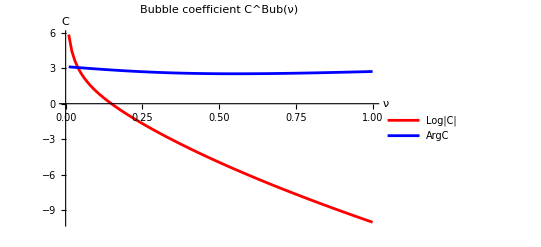

```mathematica
(* =====第四步：计算并绘制 C^Bub(ν)=====*)
(*生成数据表格：{ν,Re,Im,Abs}*)
bubblePlotData=Table[{ν,Log[N[Abs[bubbleCoefficient[ν]]]],N[Arg[bubbleCoefficient[ν]]]},{ν,0.01,1,0.01}];

(*打印表格（前 20 行示例）*)
TableForm[bubblePlotData[[1;;20]],TableHeadings->{None,{"ν","Log|C|","ArgC"}}]

(*绘制三条曲线在同一图上*)
ListPlot[{bubblePlotData[[All,{1,2}]],bubblePlotData[[All,{1,3}]]},PlotLegends->{"Log|C|","ArgC"},AxesLabel->{"ν","C"},PlotLabel->"Bubble coefficient C^Bub(ν)",Joined->True,PlotStyle->{Red,Blue}]
```

```mathematica
FullSimplify[bubbleILL[x]]
```

-((2^(-4-4 ⅈ x) (ⅈ+2 x)^2 (-3+2 x (-2 ⅈ+x)) Gamma[-3/2-2 ⅈ x] Gamma[1+2 ⅈ x] Sinh[π x]^2)/(π x^2 (-1+x (-3 ⅈ+2 x))))

```mathematica
FullSimplify[(I)^(-2 I x+2)*(4+2 I x)*Gamma[2+2 I x]/(-2 I x)- (-I)^(-2 I x+2)*(4+2 I x)*Gamma[2+2 I x]/(-2 I x)]
```

(2 (-2 ⅈ+x) Gamma[2+2 ⅈ x] Sinh[π x])/x

## Triangle diagram

### Angular loop seeds

The Triangle calculation keeps its original internal names (f0 and J0 through J3) so that the derivation remains easy to recognize.

```mathematica
(*基础种子 f0(a,b)*)f0[a_,b_]:=Gamma[a+b-3/2] Gamma[3/2-a] Gamma[3/2-b]/(Gamma[3-a-b] Gamma[a] Gamma[b]);

(*显式定义 J0,J1,J2,J3，均以 f0 线性组合表达*)
J0[m_,n_,x_]:=f0[x-m/2,x+n/2];

J1[m_,n_,x_]:=1/2*(f0[x-m/2+1/2,x+n/2-1]
-f0[x-m/2-1/2,x+n/2]
-f0[x-m/2+1/2,x+n/2]);

J2[m_,n_,x_]:=1/4*(f0[x-m/2+1,x+n/2-2]-2 f0[x-m/2,x+n/2-1]-2 f0[x-m/2+1,x+n/2-1]+f0[x-m/2-1,x+n/2]+2 f0[x-m/2,x+n/2]+f0[x-m/2+1,x+n/2]);

(*J3 直接使用附录 C 公式 (174) 的闭合形式*)
J3[m_,n_,x_]:=1/8*(f0[x-m/2+3/2,x+n/2-3]-3 f0[x-m/2+3/2,x+n/2-2]-3 f0[x-m/2+1/2,x+n/2-2]+3 f0[x-m/2+3/2,x+n/2-1]+6 f0[x-m/2+1/2,x+n/2-1]+3 f0[x-m/2-1/2,x+n/2-1]-f0[x-m/2+3/2,x+n/2]-3 f0[x-m/2+1/2,x+n/2]-3 f0[x-m/2-1/2,x+n/2]-f0[x-m/2-3/2,x+n/2]);

J4[m_,n_,x_]:=1/16*(f0[x-m/2+2,x+n/2-4]-4 f0[x-m/2+2,x+n/2-3]-4 f0[x-m/2+1,x+n/2-3]+6 f0[x-m/2+2,x+n/2-2]+12 f0[x-m/2+1,x+n/2-2]+6 f0[x-m/2,x+n/2-2]-4 f0[x-m/2+2,x+n/2-1]-12 f0[x-m/2+1,x+n/2-1]-12 f0[x-m/2,x+n/2-1]-4 f0[x-m/2-1,x+n/2-1]+f0[x-m/2+2,x+n/2]+4 f0[x-m/2+1,x+n/2]+6 f0[x-m/2,x+n/2]+4 f0[x-m/2-1,x+n/2]+f0[x-m/2-2,x+n/2]);
```

### Polarization-resolved loop factors

IL and IP collect the longitudinal and transverse polarization channels, respectively; all original channel-level variable names are retained.

```mathematica
(*定义纵向外部极化 (λ=L) 的九个角系数，记作 I[λ,σ1,σ2]*)(*符号：L 表示纵向，P 表示+，M 表示-（即横向）*)ClearAll[ILLL,ILLP,ILLM,ILPL,ILML,ILPP,ILMM,ILPM,ILMP,IL];

(*以下每个函数均接受 ν (实数) 和 θ1 (弧度)*)
ILLL[nu_,theta1_]:=Module[{s1=Sin[theta1],c1=Cos[theta1],x=-I nu},((-1/2+I nu)^4/(nu^2+1/4)^2)*((s1^2/2)*(J0[2,2,x]+J1[1,2,x]-J2[2,2,x]-J3[1,2,x])+c1^2*(J2[2,2,x]+J3[1,2,x]+J1[1,2,x]+J2[0,2,x]))]

ILLP[nu_,theta1_]:=Module[{s1=Sin[theta1],c1=Cos[theta1],x=-I nu},((-1/2+I nu)^2/(nu^2+1/4))*(-(s1^2/4)*(J1[1,2,x]-J3[1,2,x])+(c1^2/2)*(J1[1,2,x]+J0[0,2,x]-J3[1,2,x]-J2[0,2,x]))]

ILLM[nu_,theta1_]:=ILLP[nu,theta1]  (*相等*)

ILPL[nu_,theta1_]:=Module[{s1=Sin[theta1],c1=Cos[theta1],x=-I nu},((-1/2+I nu)^2/(nu^2+1/4))*((s1^2/4)*(J1[1,2,x]+J0[0,2,x]-J3[1,2,x]-J2[0,2,x])-(c1^2/2)*(J1[1,2,x]-J3[1,2,x]))]

ILML[nu_,theta1_]:=ILPL[nu,theta1]  (*相等*)

ILPP[nu_,theta1_]:=Module[{s1=Sin[theta1],c1=Cos[theta1],x=-I nu},(s1^2/8)*(J2[1,1,x]+J2[2,2,x]+J3[1,2,x]+J1[0,1,x]+J1[1,2,x]+J2[0,2,x]+J0[0,0,x]+J0[1,1,x]+J1[0,1,x])+(c1^2/4)*(J0[1,1,x]-J2[1,1,x]+J0[2,2,x]-J2[2,2,x]+J1[1,2,x]-J3[1,2,x])]

ILMM[nu_,theta1_]:=ILPP[nu,theta1]  (*相等*)

ILPM[nu_,theta1_]:=Module[{s1=Sin[theta1],c1=Cos[theta1],x=-I nu},(s1^2/8)*(J2[2,2,x]+J3[1,2,x]-J2[1,1,x]+J1[1,2,x]+J2[0,2,x]-J1[0,1,x]-J0[1,1,x]-J1[0,1,x]+J0[0,0,x])+(c1^2/4)*(J0[2,2,x]-J2[2,2,x]+J1[1,2,x]-J3[1,2,x]-J0[1,1,x]+J2[1,1,x])]

ILMP[ν_,θ1_]:=ILPM[ν,θ1];  (*-+与+-相等*)

(*定义总和\mathcal{L}^L，即九个 I 的简单加和（对应公式 (97) 的无符号和）*)
IL[ν_,θ1_]:=ILLL[ν,θ1]+ILLP[ν,θ1]+ILLM[ν,θ1]+ILPL[ν,θ1]+ILML[ν,θ1]+ILPP[ν,θ1]+ILMM[ν,θ1]+ILPM[ν,θ1]+ILMP[ν,θ1];

(*等价地，利用对称性可写作：Lsum[ν_,θ1_]:=ILLL[ν,θ1]+2 ILLP[ν,θ1]+2 ILPL[ν,θ1]+2 ILPP[ν,θ1]+2 ILPM[ν,θ1];*)
```

```mathematica
FullSimplify[ILPM[x,t]+ILMP[x,t]+ILPP[x,t]+ILMM[x,t]]
```

-(ⅈ 2^(-7-4 ⅈ x) (9+2 (5 ⅈ-4 x) x+(3-2 ⅈ x+8 x^2) Cos[2 t]) Gamma[-3/2-2 ⅈ x] Gamma[2+2 ⅈ x] Sinh[π x]^2)/(π x^2 (-ⅈ+x))

```mathematica
FullSimplify[Simplify[ILLP[x,t]+ILLM[x,t]]]
```

(2^(-5-4 ⅈ x) (1-2 ⅈ x) (3+Cos[2 t]) Gamma[-1/2-2 ⅈ x] Gamma[2 ⅈ x] Sinh[π x]^2)/(π x (-ⅈ+x))

```mathematica
FullSimplify[Simplify[ILPL[x,t]+ILML[x,t]]]
```

(2^(-5-4 ⅈ x) (1-2 ⅈ x) (3+Cos[2 t]) Gamma[-1/2-2 ⅈ x] Gamma[2 ⅈ x] Sinh[π x]^2)/(π x (-ⅈ+x))

```mathematica
FullSimplify[ILLL[x,t]]
```

-(2^(-7-4 ⅈ x) (ⅈ+2 x)^2 (-9+2 x (-7 ⅈ+4 x)+(-3+2 x (-5 ⅈ+4 x)) Cos[2 t]) Gamma[-3/2-2 ⅈ x] Gamma[1+2 ⅈ x] Sinh[π x]^2)/(π x^2 (-ⅈ+x) (-ⅈ+2 x))

```mathematica
FullSimplify[ILPM[x,t]+ILMP[x,t]+ILPP[x,t]+ILMM[x,t]+ILLP[x,t]+ILLM[x,t]+ILPL[x,t]+ILML[x,t]+ILLL[x,t]]
```

(2^(-4-4 ⅈ x) (3 ⅈ-2 x)^2 Gamma[-3/2-2 ⅈ x] Gamma[3+2 ⅈ x] Sinh[π x]^2)/(π (1+(3 ⅈ-2 x) x)^2)

```mathematica
FullSimplify[Simplify[IL[x,t]]]
```

(2^(-4-4 ⅈ x) (3 ⅈ-2 x)^2 Gamma[-3/2-2 ⅈ x] Gamma[3+2 ⅈ x] Sinh[π x]^2)/(π (1+(3 ⅈ-2 x) x)^2)

```mathematica
data=Table[{t,Log[N[Abs[IL[1,t]]]],N[Arg[IL[1,t]]]},{t,0.01,Pi,0.1}];

(*打印表格（前 20 行示例）*)
TableForm[data[[1;;20]],TableHeadings->{None,{"\theta","Log|IL|","Arg(IL)"}}]
```

heta | Log|IL| | Arg(IL)
0.01 | -2.65585 | -1.87847
0.11 | -2.65585 | -1.87847
0.21 | -2.65585 | -1.87847
0.31 | -2.65585 | -1.87847
0.41 | -2.65585 | -1.87847
0.51 | -2.65585 | -1.87847
0.61 | -2.65585 | -1.87847
0.71 | -2.65585 | -1.87847
0.81 | -2.65585 | -1.87847
0.91 | -2.65585 | -1.87847
1.01 | -2.65585 | -1.87847
1.11 | -2.65585 | -1.87847
1.21 | -2.65585 | -1.87847
1.31 | -2.65585 | -1.87847
1.41 | -2.65585 | -1.87847
1.51 | -2.65585 | -1.87847
1.61 | -2.65585 | -1.87847
1.71 | -2.65585 | -1.87847
1.81 | -2.65585 | -1.87847
1.91 | -2.65585 | -1.87847

```mathematica
(*定义横向外部极化 λ=+的角系数组合*)ClearAll[IPLL,IPLPsum,IPPPsum,IP,IM];
(*计算因子*)
IPLL[nu_,theta1_]:=Module[{s1=Sin[theta1],c1=Cos[theta1],x=-I nu},((-1/2+I nu)^4/(nu^2+1/4)^2)*(((1+c1^2)/4)*(J0[2,2,x]-J2[2,2,x]+J1[1,2,x]-J3[1,2,x])+(s1^2/2)*(J2[2,2,x]+J1[1,2,x]+J3[1,2,x]+J2[0,2,x]))]

IPLPsum[ν_,θ1_]:=Module[{s1=Sin[θ1],x=-I ν},((-1/2+I ν)^2/(ν^2+1/4))*((2+s1^2)/4*(J0[0,2,x]-J2[0,2,x]))];

IPPPsum[ν_,θ1_]:=Module[{s1=Sin[θ1],c1=Cos[θ1],x=-I ν},(1+c1^2)/4*(J2[2,2,x]+J1[1,2,x]+J3[1,2,x]+J2[0,2,x]+J0[0,0,x])+s1^2/2*(J0[2,2,x]-J2[2,2,x]+J1[1,2,x]-J3[1,2,x])];

(*总和 I+ =IPLL+IPLPsum+IPPPsum*)
IP[ν_,θ1_]:=IPLL[ν,θ1]+IPLPsum[ν,θ1]+IPPPsum[ν,θ1];

(*由对称性 I- =I+*)
IM[ν_,θ1_]:=IP[ν,θ1];
```

```mathematica
FullSimplify[Simplify[IP[x,t]]]
```

(2^(-4-4 ⅈ x) (3 ⅈ-2 x)^2 Gamma[-3/2-2 ⅈ x] Gamma[3+2 ⅈ x] Sinh[π x]^2)/(π (1+(3 ⅈ-2 x) x)^2)

```mathematica
data=Table[{t,Log[N[Abs[IP[1,t]]]],N[Arg[IP[1,t]]]},{t,0.01,Pi,0.1}];
(*打印表格（前 20 行示例）*)
TableForm[data[[1;;20]],TableHeadings->{None,{"\theta","Log|IP|","Arg(IP)"}}]
```

heta | Log|IP| | Arg(IP)
0.01 | -2.65585 | -1.87847
0.11 | -2.65585 | -1.87847
0.21 | -2.65585 | -1.87847
0.31 | -2.65585 | -1.87847
0.41 | -2.65585 | -1.87847
0.51 | -2.65585 | -1.87847
0.61 | -2.65585 | -1.87847
0.71 | -2.65585 | -1.87847
0.81 | -2.65585 | -1.87847
0.91 | -2.65585 | -1.87847
1.01 | -2.65585 | -1.87847
1.11 | -2.65585 | -1.87847
1.21 | -2.65585 | -1.87847
1.31 | -2.65585 | -1.87847
1.41 | -2.65585 | -1.87847
1.51 | -2.65585 | -1.87847
1.61 | -2.65585 | -1.87847
1.71 | -2.65585 | -1.87847
1.81 | -2.65585 | -1.87847
1.91 | -2.65585 | -1.87847

### Time-integral factor

P1 is kept as the internal name for the first time-integral coefficient.

```mathematica
Clear[P1];
(*P1:公式 (53)*)
P1[ν_]:=(2+I ν)/(2 I ν)*I*Sinh[π ν]*Gamma[2+2 I ν];
```

### Closed-form branch seeds

Mpp, Mmm, Mpm, and Mmp are the four Schwinger-Keldysh branch seeds. Their definitions and signs are unchanged.

```mathematica
(*定义四个辅助种子 MPP,MMM,MPM,MMP*)ClearAll[Mpp,Mmm,Mpm,Mmp,P2PM];
(* =========================================================*)
(*四个独立种子函数，均接受 p1,p2,ν*)
(* =========================================================*)

(*1) MPP:a=+,b=+(同号，取上面符号)*)
Mpp[p1_,p2_,ν_]:=Module[{p12=p1+p2},(*第一项*)(+I)*Exp[-I π p12/2]*Exp[-π ν]/2^(5+p12)*Gamma[5/2+p1-I ν] Gamma[5/2+p1+I ν]*Gamma[5/2+p2-I ν] Gamma[5/2+p2+I ν]/(Gamma[3+p1] Gamma[3+p2])-(*第二项*)Exp[-I π p12/2]/2^(5+p12)*Gamma[5+p12]*Gamma[5/2+p1+I ν] Gamma[5/2+p2+I ν]*HypergeometricPFQRegularized[{5+p12,1/2+I ν,1},{7/2+p1+I ν,7/2+p2+I ν},1]];

(*2) MMM:a=-,b=-(同号，取下面符号)*)
Mmm[p1_,p2_,ν_]:=Module[{p12=p1+p2},(*第一项*)(-I)*Exp[+I π p12/2]*Exp[-π ν]/2^(5+p12)*Gamma[5/2+p1+I ν] Gamma[5/2+p1-I ν]*Gamma[5/2+p2+I ν] Gamma[5/2+p2-I ν]/(Gamma[3+p1] Gamma[3+p2])-(*第二项*)Exp[+I π p12/2]/2^(5+p12)*Gamma[5+p12]*Gamma[5/2+p1-I ν] Gamma[5/2+p2-I ν]*HypergeometricPFQRegularized[{5+p12,1/2-I ν,1},{7/2+p1-I ν,7/2+p2-I ν},1]];

(*3) MPM:a=+,b=-(异号，取上符号 e^{-iπ(p1-p2)/2})*)
Mpm[p1_,p2_,ν_]:=Exp[-I π (p1-p2)/2]/2^(5+p1+p2)*Gamma[5/2+p1-I ν] Gamma[5/2+p1+I ν]*Gamma[5/2+p2-I ν] Gamma[5/2+p2+I ν]/(Gamma[3+p1] Gamma[3+p2]);

(*4) MMP:a=-,b=+(异号，取下符号 e^{+iπ(p1-p2)/2})*)
Mmp[p1_,p2_,ν_]:=Exp[+I π (p1-p2)/2]/2^(5+p1+p2)*Gamma[5/2+p1-I ν] Gamma[5/2+p1+I ν]*Gamma[5/2+p2-I ν] Gamma[5/2+p2+I ν]/(Gamma[3+p1] Gamma[3+p2]);
```

### Finite-regulator P2 construction (cross-check)

P2PM[nu, regulator] and P2L[nu, reg] retain the original regulated construction for comparison only. The primary Triangle coefficient below uses the explicit analytic P2 functions without a regulator argument.

```mathematica
(* =========================================================*)
P2PM[ν_,regulator_]:=2^(2 I ν)*((*a=+,b=+*)(Mpp[-5/2+regulator+I ν,-5/2+regulator+I ν,ν]+I*(+1)*Mpp[-3/2+I ν+regulator,-5/2+regulator+I ν,ν]+I*(+1)*Mpp[-5/2+regulator+I ν,-3/2+I ν+regulator,ν]-(+1*+1)*Mpp[-3/2+I ν+regulator,-3/2+I ν+regulator,ν])+(*a=-,b=-*)(Mmm[-5/2+regulator+I ν,-5/2+regulator+I ν,ν]+I*(-1)*Mmm[-3/2+I ν+regulator,-5/2+regulator+I ν,ν]+I*(-1)*Mmm[-5/2+regulator+I ν,-3/2+I ν+regulator,ν]-(-1*-1)*Mmm[-3/2+I ν+regulator,-3/2+I ν+regulator,ν])+(*a=+,b=-*)(Mpm[-5/2+regulator+I ν,-5/2+regulator+I ν,ν]+I*(+1)*Mpm[-3/2+I ν+regulator,-5/2+regulator+I ν,ν]+I*(-1)*Mpm[-5/2+regulator+I ν,-3/2+I ν+regulator,ν]-(+1*-1)*Mpm[-3/2+I ν+regulator,-3/2+I ν+regulator,ν])+(*a=-,b=+*)(Mmp[-5/2+regulator+I ν,-5/2+regulator+I ν,ν]+I*(-1)*Mmp[-3/2+I ν+regulator,-5/2+regulator+I ν,ν]+I*(+1)*Mmp[-5/2+regulator+I ν,-3/2+I ν+regulator,ν]-(-1*+1)*Mmp[-3/2+I ν+regulator,-3/2+I ν+regulator,ν]));
```

```mathematica
N[P2PM[0.6,0.00001]]
```

0.496557+1.2023 ⅈ

```mathematica
(*辅助函数：根据 a,b 的符号选择对应的 M 函数*)Mab[a_,b_,p1_,p2_,nu_]:=Switch[{a,b},{+1,+1},Mpp[p1,p2,nu],{-1,-1},Mmm[p1,p2,nu],{+1,-1},Mpm[p1,p2,nu],{-1,+1},Mmp[p1,p2,nu]];
(*定义 Part 2 of P_d^{(2),L}(tn)*)
Part2P2L[d_,nu_,reg_]:=Module[{p0=-5/2+I d nu+reg,prefactor=2^(2 I d nu)/(nu^2+1/4),sum},sum=Sum[With[{ia=I*a,ib=I*b,ab=a*b},(1/2+I d nu)^2*(Mab[a,b,p0,p0,nu]+ia*Mab[a,b,p0+1,p0,nu]+ib*Mab[a,b,p0,p0+1,nu]-ab*Mab[a,b,p0+1,p0+1,nu])+(1/2+I d nu)*(Mab[a,b,p0+2,p0,nu]+ib*Mab[a,b,p0+2,p0+1,nu]+Mab[a,b,p0,p0+2,nu]+ia*Mab[a,b,p0+1,p0+2,nu])+Mab[a,b,p0+2,p0+2,nu]],{a,{1,-1}},{b,{1,-1}}];
prefactor*sum];
P2L[nu_,reg_]:=P1[nu]/(nu^2+1/4)+Part2P2L[1,nu,reg]
```

### Analytic extraction from regulated P2

The imported finite-part routine expands P2L and P2PM, extracts the regulator-zero Laurent finite coefficient, and defines P2LReg0 and P2PMReg0. The following Simplify cells display those exact analytic results.

```mathematica
Get["D:\\ChatGPT-Codex\\Projects\\Unprojected\\2026-09-01\\x\\outputs\\P2_reg0_analytic.wl"]
```

```mathematica
Simplify[P2LReg0[nu]]
```

1/12 ((3 Gamma[1+2 ⅈ nu]^2)/((1+4 nu^2) Gamma[3/2+ⅈ nu]^2)-(3 ⅇ^(-2 nu π) Gamma[1+2 ⅈ nu]^2)/((1+4 nu^2) Gamma[3/2+ⅈ nu]^2)+(12 ⅈ nu Gamma[1+2 ⅈ nu]^2)/((1+4 nu^2) Gamma[3/2+ⅈ nu]^2)-(12 ⅈ ⅇ^(-2 nu π) nu Gamma[1+2 ⅈ nu]^2)/((1+4 nu^2) Gamma[3/2+ⅈ nu]^2)-(12 nu^2 Gamma[1+2 ⅈ nu]^2)/((1+4 nu^2) Gamma[3/2+ⅈ nu]^2)+(12 ⅇ^(-2 nu π) nu^2 Gamma[1+2 ⅈ nu]^2)/((1+4 nu^2) Gamma[3/2+ⅈ nu]^2)-(6 Gamma[1+2 ⅈ nu] Gamma[2+2 ⅈ nu])/((1+4 nu^2) Gamma[3/2+ⅈ nu] Gamma[5/2+ⅈ nu])+(6 ⅇ^(-2 nu π) Gamma[1+2 ⅈ nu] Gamma[2+2 ⅈ nu])/((1+4 nu^2) Gamma[3/2+ⅈ nu] Gamma[5/2+ⅈ nu])-(12 ⅈ nu Gamma[1+2 ⅈ nu] Gamma[2+2 ⅈ nu])/((1+4 nu^2) Gamma[3/2+ⅈ nu] Gamma[5/2+ⅈ nu])+(12 ⅈ ⅇ^(-2 nu π) nu Gamma[1+2 ⅈ nu] Gamma[2+2 ⅈ nu])/((1+4 nu^2) Gamma[3/2+ⅈ nu] Gamma[5/2+ⅈ nu])+(3 Gamma[2+2 ⅈ nu]^2)/((1+4 nu^2) Gamma[5/2+ⅈ nu]^2)-(3 ⅇ^(-2 nu π) Gamma[2+2 ⅈ nu]^2)/((1+4 nu^2) Gamma[5/2+ⅈ nu]^2)+(6 ⅇ^(-nu π) Gamma[4+2 ⅈ nu] (-2-5 ⅈ nu+2 nu^2-HypergeometricPFQ[{-3/2-ⅈ nu,2+2 ⅈ nu},{1},1]))/((3+8 ⅈ nu-4 nu^2)^2 (ⅈ+nu+2 ⅈ nu^2))+(24 ⅇ^(-nu π) nu^2 Gamma[2+2 ⅈ nu] (-1+HypergeometricPFQ[{-1/2-ⅈ nu,1+2 ⅈ nu},{1},1]))/((-1+2 ⅈ nu) (-ⅈ+2 nu)^3)+(6 ⅇ^(-nu π) Gamma[2+2 ⅈ nu] (-1+HypergeometricPFQ[{-1/2-ⅈ nu,1+2 ⅈ nu},{1},1]))/((1+2 ⅈ nu)^3 (ⅈ+2 nu))-(24 ⅇ^(-nu π) nu Gamma[2+2 ⅈ nu] (-1+HypergeometricPFQ[{-1/2-ⅈ nu,1+2 ⅈ nu},{1},1]))/((-ⅈ+2 nu)^3 (ⅈ+2 nu))+(6 ⅇ^(-nu π) Gamma[3+2 ⅈ nu] (-1+HypergeometricPFQ[{-1/2-ⅈ nu,2+2 ⅈ nu},{2},1]))/((ⅈ-2 nu)^2 (ⅈ+nu+2 ⅈ nu^2))+(12 ⅇ^(-nu π) nu Gamma[3+2 ⅈ nu] (-1+HypergeometricPFQ[{-1/2-ⅈ nu,2+2 ⅈ nu},{2},1]))/((ⅈ-2 nu)^2 (1-ⅈ nu+2 nu^2))-(3 ⅈ ⅇ^(nu π) Gamma[1+2 ⅈ nu]^2 HypergeometricPFQRegularized[{1,1/2+ⅈ nu},{2+2 ⅈ nu},1])/(1+4 nu^2)+(12 ⅇ^(nu π) nu Gamma[1+2 ⅈ nu]^2 HypergeometricPFQRegularized[{1,1/2+ⅈ nu},{2+2 ⅈ nu},1])/(1+4 nu^2)+(12 ⅈ ⅇ^(nu π) nu^2 Gamma[1+2 ⅈ nu]^2 HypergeometricPFQRegularized[{1,1/2+ⅈ nu},{2+2 ⅈ nu},1])/(1+4 nu^2)+(6 ⅈ ⅇ^(nu π) Gamma[1+2 ⅈ nu] Gamma[2+2 ⅈ nu] HypergeometricPFQRegularized[{1,1/2+ⅈ nu},{2+2 ⅈ nu},1])/(1+4 nu^2)-(12 ⅇ^(nu π) nu Gamma[1+2 ⅈ nu] Gamma[2+2 ⅈ nu] HypergeometricPFQRegularized[{1,1/2+ⅈ nu},{2+2 ⅈ nu},1])/(1+4 nu^2)-(12 ⅈ ⅇ^(nu π) Gamma[1+2 ⅈ nu] Gamma[2 ⅈ nu] HypergeometricPFQRegularized[{1,1/2+ⅈ nu},{2+2 ⅈ nu},1])/(1+4 nu^2)+(48 ⅇ^(nu π) nu Gamma[1+2 ⅈ nu] Gamma[2 ⅈ nu] HypergeometricPFQRegularized[{1,1/2+ⅈ nu},{2+2 ⅈ nu},1])/(1+4 nu^2)+(48 ⅈ ⅇ^(nu π) nu^2 Gamma[1+2 ⅈ nu] Gamma[2 ⅈ nu] HypergeometricPFQRegularized[{1,1/2+ⅈ nu},{2+2 ⅈ nu},1])/(1+4 nu^2)+(6 ⅈ ⅇ^(nu π) Gamma[2+2 ⅈ nu]^2 Gamma[2 ⅈ nu] HypergeometricPFQRegularized[{2+2 ⅈ nu,1/2+ⅈ nu,1},{1+2 ⅈ nu,3+2 ⅈ nu},1])/(1+4 nu^2)-(12 ⅇ^(nu π) nu Gamma[2+2 ⅈ nu]^2 Gamma[2 ⅈ nu] HypergeometricPFQRegularized[{2+2 ⅈ nu,1/2+ⅈ nu,1},{1+2 ⅈ nu,3+2 ⅈ nu},1])/(1+4 nu^2)+(6 ⅈ ⅇ^(nu π) Gamma[2+2 ⅈ nu]^2 Gamma[2 ⅈ nu] HypergeometricPFQRegularized[{2+2 ⅈ nu,1/2+ⅈ nu,1},{3+2 ⅈ nu,1+2 ⅈ nu},1])/(1+4 nu^2)-(12 ⅇ^(nu π) nu Gamma[2+2 ⅈ nu]^2 Gamma[2 ⅈ nu] HypergeometricPFQRegularized[{2+2 ⅈ nu,1/2+ⅈ nu,1},{3+2 ⅈ nu,1+2 ⅈ nu},1])/(1+4 nu^2)-(3 ⅈ ⅇ^(nu π) Gamma[2+2 ⅈ nu]^2 Gamma[4+2 ⅈ nu] HypergeometricPFQRegularized[{4+2 ⅈ nu,1/2+ⅈ nu,1},{3+2 ⅈ nu,3+2 ⅈ nu},1])/(1+4 nu^2)-(12 ⅈ ⅇ^(nu π) Gamma[2 ⅈ nu]^3 HypergeometricPFQRegularized[{2 ⅈ nu,1/2+ⅈ nu,1},{1+2 ⅈ nu,1+2 ⅈ nu},1])/(1+4 nu^2)+(48 ⅇ^(nu π) nu Gamma[2 ⅈ nu]^3 HypergeometricPFQRegularized[{2 ⅈ nu,1/2+ⅈ nu,1},{1+2 ⅈ nu,1+2 ⅈ nu},1])/(1+4 nu^2)+(48 ⅈ ⅇ^(nu π) nu^2 Gamma[2 ⅈ nu]^3 HypergeometricPFQRegularized[{2 ⅈ nu,1/2+ⅈ nu,1},{1+2 ⅈ nu,1+2 ⅈ nu},1])/(1+4 nu^2)-(24 Gamma[1+2 ⅈ nu] Gamma[2 ⅈ nu] (2 EulerGamma+Log[4]+PolyGamma[0,1/2+ⅈ nu]+PolyGamma[0,3/2+ⅈ nu]-PolyGamma[0,1+2 ⅈ nu]-PolyGamma[0,2 ⅈ nu]))/((1+4 nu^2) Gamma[1/2+ⅈ nu] Gamma[3/2+ⅈ nu])-(96 ⅈ nu Gamma[1+2 ⅈ nu] Gamma[2 ⅈ nu] (2 EulerGamma+Log[4]+PolyGamma[0,1/2+ⅈ nu]+PolyGamma[0,3/2+ⅈ nu]-PolyGamma[0,1+2 ⅈ nu]-PolyGamma[0,2 ⅈ nu]))/((1+4 nu^2) Gamma[1/2+ⅈ nu] Gamma[3/2+ⅈ nu])+(96 nu^2 Gamma[1+2 ⅈ nu] Gamma[2 ⅈ nu] (2 EulerGamma+Log[4]+PolyGamma[0,1/2+ⅈ nu]+PolyGamma[0,3/2+ⅈ nu]-PolyGamma[0,1+2 ⅈ nu]-PolyGamma[0,2 ⅈ nu]))/((1+4 nu^2) Gamma[1/2+ⅈ nu] Gamma[3/2+ⅈ nu])+(12 ⅇ^(-2 nu π) Gamma[1+2 ⅈ nu] Gamma[2 ⅈ nu] (2 EulerGamma-ⅈ π+Log[4]+PolyGamma[0,1/2+ⅈ nu]+PolyGamma[0,3/2+ⅈ nu]-PolyGamma[0,1+2 ⅈ nu]-PolyGamma[0,2 ⅈ nu]))/((1+4 nu^2) Gamma[1/2+ⅈ nu] Gamma[3/2+ⅈ nu])+(48 ⅈ ⅇ^(-2 nu π) nu Gamma[1+2 ⅈ nu] Gamma[2 ⅈ nu] (2 EulerGamma-ⅈ π+Log[4]+PolyGamma[0,1/2+ⅈ nu]+PolyGamma[0,3/2+ⅈ nu]-PolyGamma[0,1+2 ⅈ nu]-PolyGamma[0,2 ⅈ nu]))/((1+4 nu^2) Gamma[1/2+ⅈ nu] Gamma[3/2+ⅈ nu])-(48 ⅇ^(-2 nu π) nu^2 Gamma[1+2 ⅈ nu] Gamma[2 ⅈ nu] (2 EulerGamma-ⅈ π+Log[4]+PolyGamma[0,1/2+ⅈ nu]+PolyGamma[0,3/2+ⅈ nu]-PolyGamma[0,1+2 ⅈ nu]-PolyGamma[0,2 ⅈ nu]))/((1+4 nu^2) Gamma[1/2+ⅈ nu] Gamma[3/2+ⅈ nu])+(12 Gamma[1+2 ⅈ nu] Gamma[2 ⅈ nu] (2 EulerGamma+ⅈ π+Log[4]+PolyGamma[0,1/2+ⅈ nu]+PolyGamma[0,3/2+ⅈ nu]-PolyGamma[0,1+2 ⅈ nu]-PolyGamma[0,2 ⅈ nu]))/((1+4 nu^2) Gamma[1/2+ⅈ nu] Gamma[3/2+ⅈ nu])+(48 ⅈ nu Gamma[1+2 ⅈ nu] Gamma[2 ⅈ nu] (2 EulerGamma+ⅈ π+Log[4]+PolyGamma[0,1/2+ⅈ nu]+PolyGamma[0,3/2+ⅈ nu]-PolyGamma[0,1+2 ⅈ nu]-PolyGamma[0,2 ⅈ nu]))/((1+4 nu^2) Gamma[1/2+ⅈ nu] Gamma[3/2+ⅈ nu])-(48 nu^2 Gamma[1+2 ⅈ nu] Gamma[2 ⅈ nu] (2 EulerGamma+ⅈ π+Log[4]+PolyGamma[0,1/2+ⅈ nu]+PolyGamma[0,3/2+ⅈ nu]-PolyGamma[0,1+2 ⅈ nu]-PolyGamma[0,2 ⅈ nu]))/((1+4 nu^2) Gamma[1/2+ⅈ nu] Gamma[3/2+ⅈ nu])+(24 Gamma[2+2 ⅈ nu] Gamma[2 ⅈ nu] (-1+2 EulerGamma+Log[4]+PolyGamma[0,1/2+ⅈ nu]+PolyGamma[0,5/2+ⅈ nu]-PolyGamma[0,2+2 ⅈ nu]-PolyGamma[0,2 ⅈ nu]))/((1+4 nu^2) Gamma[1/2+ⅈ nu] Gamma[5/2+ⅈ nu])+(48 ⅈ nu Gamma[2+2 ⅈ nu] Gamma[2 ⅈ nu] (-1+2 EulerGamma+Log[4]+PolyGamma[0,1/2+ⅈ nu]+PolyGamma[0,5/2+ⅈ nu]-PolyGamma[0,2+2 ⅈ nu]-PolyGamma[0,2 ⅈ nu]))/((1+4 nu^2) Gamma[1/2+ⅈ nu] Gamma[5/2+ⅈ nu])-(12 ⅇ^(-2 nu π) Gamma[2+2 ⅈ nu] Gamma[2 ⅈ nu] (-1+2 EulerGamma-ⅈ π+Log[4]+PolyGamma[0,1/2+ⅈ nu]+PolyGamma[0,5/2+ⅈ nu]-PolyGamma[0,2+2 ⅈ nu]-PolyGamma[0,2 ⅈ nu]))/((1+4 nu^2) Gamma[1/2+ⅈ nu] Gamma[5/2+ⅈ nu])-(24 ⅈ ⅇ^(-2 nu π) nu Gamma[2+2 ⅈ nu] Gamma[2 ⅈ nu] (-1+2 EulerGamma-ⅈ π+Log[4]+PolyGamma[0,1/2+ⅈ nu]+PolyGamma[0,5/2+ⅈ nu]-PolyGamma[0,2+2 ⅈ nu]-PolyGamma[0,2 ⅈ nu]))/((1+4 nu^2) Gamma[1/2+ⅈ nu] Gamma[5/2+ⅈ nu])-(12 Gamma[2+2 ⅈ nu] Gamma[2 ⅈ nu] (-1+2 EulerGamma+ⅈ π+Log[4]+PolyGamma[0,1/2+ⅈ nu]+PolyGamma[0,5/2+ⅈ nu]-PolyGamma[0,2+2 ⅈ nu]-PolyGamma[0,2 ⅈ nu]))/((1+4 nu^2) Gamma[1/2+ⅈ nu] Gamma[5/2+ⅈ nu])-(24 ⅈ nu Gamma[2+2 ⅈ nu] Gamma[2 ⅈ nu] (-1+2 EulerGamma+ⅈ π+Log[4]+PolyGamma[0,1/2+ⅈ nu]+PolyGamma[0,5/2+ⅈ nu]-PolyGamma[0,2+2 ⅈ nu]-PolyGamma[0,2 ⅈ nu]))/((1+4 nu^2) Gamma[1/2+ⅈ nu] Gamma[5/2+ⅈ nu])-1/((1+4 nu^2) Gamma[1/2+ⅈ nu]^2)4 ⅇ^(-2 nu π) Gamma[2 ⅈ nu]^2 (6 EulerGamma^2-6 ⅈ EulerGamma π-π^2+12 EulerGamma Log[2]-6 ⅈ π Log[2]+6 Log[2]^2+6 PolyGamma[0,1/2+ⅈ nu]^2+6 PolyGamma[0,1/2+ⅈ nu] (2 EulerGamma-ⅈ π+Log[4]-2 PolyGamma[0,2 ⅈ nu])-6 (2 EulerGamma-ⅈ π+Log[4]) PolyGamma[0,2 ⅈ nu]+6 PolyGamma[0,2 ⅈ nu]^2-3 PolyGamma[1,1/2+ⅈ nu]+3 PolyGamma[1,2 ⅈ nu])-1/((1+4 nu^2) Gamma[1/2+ⅈ nu]^2)16 ⅈ ⅇ^(-2 nu π) nu Gamma[2 ⅈ nu]^2 (6 EulerGamma^2-6 ⅈ EulerGamma π-π^2+6 Log[2]^2+6 EulerGamma Log[4]-3 ⅈ π Log[4]+6 PolyGamma[0,1/2+ⅈ nu]^2+6 PolyGamma[0,1/2+ⅈ nu] (2 EulerGamma-ⅈ π+Log[4]-2 PolyGamma[0,2 ⅈ nu])-6 (2 EulerGamma-ⅈ π+Log[4]) PolyGamma[0,2 ⅈ nu]+6 PolyGamma[0,2 ⅈ nu]^2-3 PolyGamma[1,1/2+ⅈ nu]+3 PolyGamma[1,2 ⅈ nu])+1/((1+4 nu^2) Gamma[1/2+ⅈ nu]^2)16 ⅇ^(-2 nu π) nu^2 Gamma[2 ⅈ nu]^2 (6 EulerGamma^2-6 ⅈ EulerGamma π-π^2+6 Log[2]^2+6 EulerGamma Log[4]-3 ⅈ π Log[4]+6 PolyGamma[0,1/2+ⅈ nu]^2+6 PolyGamma[0,1/2+ⅈ nu] (2 EulerGamma-ⅈ π+Log[4]-2 PolyGamma[0,2 ⅈ nu])-6 (2 EulerGamma-ⅈ π+Log[4]) PolyGamma[0,2 ⅈ nu]+6 PolyGamma[0,2 ⅈ nu]^2-3 PolyGamma[1,1/2+ⅈ nu]+3 PolyGamma[1,2 ⅈ nu])-1/((1+4 nu^2) Gamma[1/2+ⅈ nu]^2)4 Gamma[2 ⅈ nu]^2 (6 EulerGamma^2+6 ⅈ EulerGamma π-π^2+12 EulerGamma Log[2]+6 ⅈ π Log[2]+6 Log[2]^2+6 PolyGamma[0,1/2+ⅈ nu]^2+6 PolyGamma[0,1/2+ⅈ nu] (2 EulerGamma+ⅈ π+Log[4]-2 PolyGamma[0,2 ⅈ nu])-6 (2 EulerGamma+ⅈ π+Log[4]) PolyGamma[0,2 ⅈ nu]+6 PolyGamma[0,2 ⅈ nu]^2-3 PolyGamma[1,1/2+ⅈ nu]+3 PolyGamma[1,2 ⅈ nu])-1/((1+4 nu^2) Gamma[1/2+ⅈ nu]^2)16 ⅈ nu Gamma[2 ⅈ nu]^2 (6 EulerGamma^2+6 ⅈ EulerGamma π-π^2+6 Log[2]^2+6 EulerGamma Log[4]+3 ⅈ π Log[4]+6 PolyGamma[0,1/2+ⅈ nu]^2+6 PolyGamma[0,1/2+ⅈ nu] (2 EulerGamma+ⅈ π+Log[4]-2 PolyGamma[0,2 ⅈ nu])-6 (2 EulerGamma+ⅈ π+Log[4]) PolyGamma[0,2 ⅈ nu]+6 PolyGamma[0,2 ⅈ nu]^2-3 PolyGamma[1,1/2+ⅈ nu]+3 PolyGamma[1,2 ⅈ nu])+1/((1+4 nu^2) Gamma[1/2+ⅈ nu]^2)16 nu^2 Gamma[2 ⅈ nu]^2 (6 EulerGamma^2+6 ⅈ EulerGamma π-π^2+6 Log[2]^2+6 EulerGamma Log[4]+3 ⅈ π Log[4]+6 PolyGamma[0,1/2+ⅈ nu]^2+6 PolyGamma[0,1/2+ⅈ nu] (2 EulerGamma+ⅈ π+Log[4]-2 PolyGamma[0,2 ⅈ nu])-6 (2 EulerGamma+ⅈ π+Log[4]) PolyGamma[0,2 ⅈ nu]+6 PolyGamma[0,2 ⅈ nu]^2-3 PolyGamma[1,1/2+ⅈ nu]+3 PolyGamma[1,2 ⅈ nu])+1/((1+4 nu^2) Gamma[1/2+ⅈ nu]^2)4 Gamma[2 ⅈ nu]^2 (12 EulerGamma^2+π^2+24 EulerGamma Log[2]+12 Log[2]^2+12 PolyGamma[0,1/2+ⅈ nu]^2+24 PolyGamma[0,1/2+ⅈ nu] (EulerGamma+Log[2]-PolyGamma[0,2 ⅈ nu])-24 (EulerGamma+Log[2]) PolyGamma[0,2 ⅈ nu]+12 PolyGamma[0,2 ⅈ nu]^2-6 PolyGamma[1,1/2+ⅈ nu]+6 PolyGamma[1,2 ⅈ nu])+1/((1+4 nu^2) Gamma[1/2+ⅈ nu]^2)16 ⅈ nu Gamma[2 ⅈ nu]^2 (12 EulerGamma^2+π^2+24 EulerGamma Log[2]+12 Log[2]^2+12 PolyGamma[0,1/2+ⅈ nu]^2+24 PolyGamma[0,1/2+ⅈ nu] (EulerGamma+Log[2]-PolyGamma[0,2 ⅈ nu])-24 (EulerGamma+Log[2]) PolyGamma[0,2 ⅈ nu]+12 PolyGamma[0,2 ⅈ nu]^2-6 PolyGamma[1,1/2+ⅈ nu]+6 PolyGamma[1,2 ⅈ nu])-1/((1+4 nu^2) Gamma[1/2+ⅈ nu]^2)16 nu^2 Gamma[2 ⅈ nu]^2 (12 EulerGamma^2+π^2+24 EulerGamma Log[2]+12 Log[2]^2+12 PolyGamma[0,1/2+ⅈ nu]^2+24 PolyGamma[0,1/2+ⅈ nu] (EulerGamma+Log[2]-PolyGamma[0,2 ⅈ nu])-24 (EulerGamma+Log[2]) PolyGamma[0,2 ⅈ nu]+12 PolyGamma[0,2 ⅈ nu]^2-6 PolyGamma[1,1/2+ⅈ nu]+6 PolyGamma[1,2 ⅈ nu])+(6 ⅈ Gamma[2+2 ⅈ nu] Sinh[nu π])/(1/4+nu^2)+(48 Gamma[2+2 ⅈ nu] Sinh[nu π])/(nu+4 nu^3)-1/(1+4 nu^2)6 ⅈ ⅇ^(-nu π) Gamma[1+2 ⅈ nu] (HypergeometricPFQ[{1/2-ⅈ nu,1+2 ⅈ nu},{2},1] (2 EulerGamma-ⅈ π+Log[4]-2 PolyGamma[0,1+2 ⅈ nu])-HypergeometricPFQRegularized^({0,0,0},{0,1},0)[{1+2 ⅈ nu,1/2-ⅈ nu,1},{1,2},1]-HypergeometricPFQRegularized^({0,0,0},{1,0},0)[{1+2 ⅈ nu,1/2-ⅈ nu,1},{1,2},1]-2 HypergeometricPFQRegularized^({1,0,0},{0,0},0)[{1+2 ⅈ nu,1/2-ⅈ nu,1},{1,2},1])+1/(1+4 nu^2)24 ⅇ^(-nu π) nu Gamma[1+2 ⅈ nu] (HypergeometricPFQ[{1/2-ⅈ nu,1+2 ⅈ nu},{2},1] (2 EulerGamma-ⅈ π+Log[4]-2 PolyGamma[0,1+2 ⅈ nu])-HypergeometricPFQRegularized^({0,0,0},{0,1},0)[{1+2 ⅈ nu,1/2-ⅈ nu,1},{1,2},1]-HypergeometricPFQRegularized^({0,0,0},{1,0},0)[{1+2 ⅈ nu,1/2-ⅈ nu,1},{1,2},1]-2 HypergeometricPFQRegularized^({1,0,0},{0,0},0)[{1+2 ⅈ nu,1/2-ⅈ nu,1},{1,2},1])+1/(1+4 nu^2)24 ⅈ ⅇ^(-nu π) nu^2 Gamma[1+2 ⅈ nu] (HypergeometricPFQ[{1/2-ⅈ nu,1+2 ⅈ nu},{2},1] (2 EulerGamma-ⅈ π+Log[4]-2 PolyGamma[0,1+2 ⅈ nu])-HypergeometricPFQRegularized^({0,0,0},{0,1},0)[{1+2 ⅈ nu,1/2-ⅈ nu,1},{1,2},1]-HypergeometricPFQRegularized^({0,0,0},{1,0},0)[{1+2 ⅈ nu,1/2-ⅈ nu,1},{1,2},1]-2 HypergeometricPFQRegularized^({1,0,0},{0,0},0)[{1+2 ⅈ nu,1/2-ⅈ nu,1},{1,2},1])-1/(1+4 nu^2)6 ⅈ ⅇ^(-nu π) Gamma[1+2 ⅈ nu] (HypergeometricPFQ[{1/2-ⅈ nu,1+2 ⅈ nu},{2},1] (2 EulerGamma-ⅈ π+Log[4]-2 PolyGamma[0,1+2 ⅈ nu])-HypergeometricPFQRegularized^({0,0,0},{0,1},0)[{1+2 ⅈ nu,1/2-ⅈ nu,1},{2,1},1]-HypergeometricPFQRegularized^({0,0,0},{1,0},0)[{1+2 ⅈ nu,1/2-ⅈ nu,1},{2,1},1]-2 HypergeometricPFQRegularized^({1,0,0},{0,0},0)[{1+2 ⅈ nu,1/2-ⅈ nu,1},{2,1},1])+1/(1+4 nu^2)24 ⅇ^(-nu π) nu Gamma[1+2 ⅈ nu] (HypergeometricPFQ[{1/2-ⅈ nu,1+2 ⅈ nu},{2},1] (2 EulerGamma-ⅈ π+Log[4]-2 PolyGamma[0,1+2 ⅈ nu])-HypergeometricPFQRegularized^({0,0,0},{0,1},0)[{1+2 ⅈ nu,1/2-ⅈ nu,1},{2,1},1]-HypergeometricPFQRegularized^({0,0,0},{1,0},0)[{1+2 ⅈ nu,1/2-ⅈ nu,1},{2,1},1]-2 HypergeometricPFQRegularized^({1,0,0},{0,0},0)[{1+2 ⅈ nu,1/2-ⅈ nu,1},{2,1},1])+1/(1+4 nu^2)24 ⅈ ⅇ^(-nu π) nu^2 Gamma[1+2 ⅈ nu] (HypergeometricPFQ[{1/2-ⅈ nu,1+2 ⅈ nu},{2},1] (2 EulerGamma-ⅈ π+Log[4]-2 PolyGamma[0,1+2 ⅈ nu])-HypergeometricPFQRegularized^({0,0,0},{0,1},0)[{1+2 ⅈ nu,1/2-ⅈ nu,1},{2,1},1]-HypergeometricPFQRegularized^({0,0,0},{1,0},0)[{1+2 ⅈ nu,1/2-ⅈ nu,1},{2,1},1]-2 HypergeometricPFQRegularized^({1,0,0},{0,0},0)[{1+2 ⅈ nu,1/2-ⅈ nu,1},{2,1},1])+1/(1+4 nu^2)3 ⅈ ⅇ^(-nu π) Gamma[2+2 ⅈ nu] (HypergeometricPFQ[{1/2-ⅈ nu,2+2 ⅈ nu},{3},1] (-1+2 EulerGamma-ⅈ π+Log[4]-2 PolyGamma[0,2+2 ⅈ nu])-2 (HypergeometricPFQRegularized^({0,0,0},{0,1},0)[{2+2 ⅈ nu,1/2-ⅈ nu,1},{1,3},1]+HypergeometricPFQRegularized^({0,0,0},{1,0},0)[{2+2 ⅈ nu,1/2-ⅈ nu,1},{1,3},1]+2 HypergeometricPFQRegularized^({1,0,0},{0,0},0)[{2+2 ⅈ nu,1/2-ⅈ nu,1},{1,3},1]))-1/(1+4 nu^2)6 ⅇ^(-nu π) nu Gamma[2+2 ⅈ nu] (HypergeometricPFQ[{1/2-ⅈ nu,2+2 ⅈ nu},{3},1] (-1+2 EulerGamma-ⅈ π+Log[4]-2 PolyGamma[0,2+2 ⅈ nu])-2 (HypergeometricPFQRegularized^({0,0,0},{0,1},0)[{2+2 ⅈ nu,1/2-ⅈ nu,1},{1,3},1]+HypergeometricPFQRegularized^({0,0,0},{1,0},0)[{2+2 ⅈ nu,1/2-ⅈ nu,1},{1,3},1]+2 HypergeometricPFQRegularized^({1,0,0},{0,0},0)[{2+2 ⅈ nu,1/2-ⅈ nu,1},{1,3},1]))+1/(1+4 nu^2)3 ⅈ ⅇ^(-nu π) Gamma[2+2 ⅈ nu] (HypergeometricPFQ[{1/2-ⅈ nu,2+2 ⅈ nu},{3},1] (-1+2 EulerGamma-ⅈ π+Log[4]-2 PolyGamma[0,2+2 ⅈ nu])-2 (HypergeometricPFQRegularized^({0,0,0},{0,1},0)[{2+2 ⅈ nu,1/2-ⅈ nu,1},{3,1},1]+HypergeometricPFQRegularized^({0,0,0},{1,0},0)[{2+2 ⅈ nu,1/2-ⅈ nu,1},{3,1},1]+2 HypergeometricPFQRegularized^({1,0,0},{0,0},0)[{2+2 ⅈ nu,1/2-ⅈ nu,1},{3,1},1]))-1/(1+4 nu^2)6 ⅇ^(-nu π) nu Gamma[2+2 ⅈ nu] (HypergeometricPFQ[{1/2-ⅈ nu,2+2 ⅈ nu},{3},1] (-1+2 EulerGamma-ⅈ π+Log[4]-2 PolyGamma[0,2+2 ⅈ nu])-2 (HypergeometricPFQRegularized^({0,0,0},{0,1},0)[{2+2 ⅈ nu,1/2-ⅈ nu,1},{3,1},1]+HypergeometricPFQRegularized^({0,0,0},{1,0},0)[{2+2 ⅈ nu,1/2-ⅈ nu,1},{3,1},1]+2 HypergeometricPFQRegularized^({1,0,0},{0,0},0)[{2+2 ⅈ nu,1/2-ⅈ nu,1},{3,1},1]))+1/(1+4 nu^2)2 ⅈ ⅇ^(-nu π) Gamma[2 ⅈ nu] (2 HypergeometricPFQ[{1/2-ⅈ nu,2 ⅈ nu},{1},1] (6 EulerGamma^2-6 ⅈ EulerGamma π-π^2+12 EulerGamma Log[2]-6 ⅈ π Log[2]+6 Log[2]^2-6 (2 EulerGamma-ⅈ π+Log[4]) PolyGamma[0,2 ⅈ nu]+6 PolyGamma[0,2 ⅈ nu]^2+6 PolyGamma[1,2 ⅈ nu])-3 ((4 EulerGamma-2 ⅈ π+Log[16]-4 PolyGamma[0,2 ⅈ nu]) HypergeometricPFQRegularized^({0,0,0},{0,1},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-HypergeometricPFQRegularized^({0,0,0},{0,2},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]+4 EulerGamma HypergeometricPFQRegularized^({0,0,0},{1,0},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-2 ⅈ π HypergeometricPFQRegularized^({0,0,0},{1,0},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]+Log[16] HypergeometricPFQRegularized^({0,0,0},{1,0},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-4 PolyGamma[0,2 ⅈ nu] HypergeometricPFQRegularized^({0,0,0},{1,0},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-2 HypergeometricPFQRegularized^({0,0,0},{1,1},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-HypergeometricPFQRegularized^({0,0,0},{2,0},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]+8 EulerGamma HypergeometricPFQRegularized^({1,0,0},{0,0},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-4 ⅈ π HypergeometricPFQRegularized^({1,0,0},{0,0},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]+8 Log[2] HypergeometricPFQRegularized^({1,0,0},{0,0},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-8 PolyGamma[0,2 ⅈ nu] HypergeometricPFQRegularized^({1,0,0},{0,0},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-4 HypergeometricPFQRegularized^({1,0,0},{0,1},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-4 HypergeometricPFQRegularized^({1,0,0},{1,0},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-4 HypergeometricPFQRegularized^({2,0,0},{0,0},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]))-1/(1+4 nu^2)8 ⅇ^(-nu π) nu Gamma[2 ⅈ nu] (2 HypergeometricPFQ[{1/2-ⅈ nu,2 ⅈ nu},{1},1] (6 EulerGamma^2-6 ⅈ EulerGamma π-π^2+6 Log[2]^2+6 EulerGamma Log[4]-3 ⅈ π Log[4]-6 (2 EulerGamma-ⅈ π+Log[4]) PolyGamma[0,2 ⅈ nu]+6 PolyGamma[0,2 ⅈ nu]^2+6 PolyGamma[1,2 ⅈ nu])-3 (2 (2 EulerGamma-ⅈ π+Log[4]-2 PolyGamma[0,2 ⅈ nu]) HypergeometricPFQRegularized^({0,0,0},{0,1},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-HypergeometricPFQRegularized^({0,0,0},{0,2},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]+4 EulerGamma HypergeometricPFQRegularized^({0,0,0},{1,0},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-2 ⅈ π HypergeometricPFQRegularized^({0,0,0},{1,0},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]+Log[16] HypergeometricPFQRegularized^({0,0,0},{1,0},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-4 PolyGamma[0,2 ⅈ nu] HypergeometricPFQRegularized^({0,0,0},{1,0},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-2 HypergeometricPFQRegularized^({0,0,0},{1,1},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-HypergeometricPFQRegularized^({0,0,0},{2,0},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]+8 EulerGamma HypergeometricPFQRegularized^({1,0,0},{0,0},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-4 ⅈ π HypergeometricPFQRegularized^({1,0,0},{0,0},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]+4 Log[4] HypergeometricPFQRegularized^({1,0,0},{0,0},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-8 PolyGamma[0,2 ⅈ nu] HypergeometricPFQRegularized^({1,0,0},{0,0},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-4 HypergeometricPFQRegularized^({1,0,0},{0,1},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-4 HypergeometricPFQRegularized^({1,0,0},{1,0},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-4 HypergeometricPFQRegularized^({2,0,0},{0,0},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]))+1/(1+4 nu^2)8 ⅇ^(-nu π) nu^2 Gamma[2 ⅈ nu] (-2 ⅈ HypergeometricPFQ[{1/2-ⅈ nu,2 ⅈ nu},{1},1] (6 EulerGamma^2-6 ⅈ EulerGamma π-π^2+6 Log[2]^2+6 EulerGamma Log[4]-3 ⅈ π Log[4]-6 (2 EulerGamma-ⅈ π+Log[4]) PolyGamma[0,2 ⅈ nu]+6 PolyGamma[0,2 ⅈ nu]^2+6 PolyGamma[1,2 ⅈ nu])+3 ⅈ (2 (2 EulerGamma-ⅈ π+Log[4]-2 PolyGamma[0,2 ⅈ nu]) HypergeometricPFQRegularized^({0,0,0},{0,1},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-HypergeometricPFQRegularized^({0,0,0},{0,2},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]+4 EulerGamma HypergeometricPFQRegularized^({0,0,0},{1,0},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-2 ⅈ π HypergeometricPFQRegularized^({0,0,0},{1,0},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]+Log[16] HypergeometricPFQRegularized^({0,0,0},{1,0},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-4 PolyGamma[0,2 ⅈ nu] HypergeometricPFQRegularized^({0,0,0},{1,0},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-2 HypergeometricPFQRegularized^({0,0,0},{1,1},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-HypergeometricPFQRegularized^({0,0,0},{2,0},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]+8 EulerGamma HypergeometricPFQRegularized^({1,0,0},{0,0},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-4 ⅈ π HypergeometricPFQRegularized^({1,0,0},{0,0},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]+4 Log[4] HypergeometricPFQRegularized^({1,0,0},{0,0},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-8 PolyGamma[0,2 ⅈ nu] HypergeometricPFQRegularized^({1,0,0},{0,0},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-4 HypergeometricPFQRegularized^({1,0,0},{0,1},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-4 HypergeometricPFQRegularized^({1,0,0},{1,0},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-4 HypergeometricPFQRegularized^({2,0,0},{0,0},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1])))

```mathematica
Simplify[P2PMReg0[nu]]
```

1/12 ((3 Gamma[1+2 ⅈ nu]^2)/Gamma[3/2+ⅈ nu]^2-(3 ⅇ^(-2 nu π) Gamma[1+2 ⅈ nu]^2)/Gamma[3/2+ⅈ nu]^2+(6 ⅈ ⅇ^(-nu π) Gamma[2+2 ⅈ nu] (-1+HypergeometricPFQ[{-1/2-ⅈ nu,1+2 ⅈ nu},{1},1]))/(ⅈ-2 nu)^2-3 ⅈ ⅇ^(nu π) Gamma[1+2 ⅈ nu]^2 HypergeometricPFQRegularized[{1,1/2+ⅈ nu},{2+2 ⅈ nu},1]-12 ⅈ ⅇ^(nu π) Gamma[1+2 ⅈ nu] Gamma[2 ⅈ nu] HypergeometricPFQRegularized[{1,1/2+ⅈ nu},{2+2 ⅈ nu},1]-12 ⅈ ⅇ^(nu π) Gamma[2 ⅈ nu]^3 HypergeometricPFQRegularized[{2 ⅈ nu,1/2+ⅈ nu,1},{1+2 ⅈ nu,1+2 ⅈ nu},1]-(24 Gamma[1+2 ⅈ nu] Gamma[2 ⅈ nu] (2 EulerGamma+Log[4]+PolyGamma[0,1/2+ⅈ nu]+PolyGamma[0,3/2+ⅈ nu]-PolyGamma[0,1+2 ⅈ nu]-PolyGamma[0,2 ⅈ nu]))/(Gamma[1/2+ⅈ nu] Gamma[3/2+ⅈ nu])+1/(Gamma[1/2+ⅈ nu] Gamma[3/2+ⅈ nu])12 ⅇ^(-2 nu π) Gamma[1+2 ⅈ nu] Gamma[2 ⅈ nu] (2 EulerGamma-ⅈ π+Log[4]+PolyGamma[0,1/2+ⅈ nu]+PolyGamma[0,3/2+ⅈ nu]-PolyGamma[0,1+2 ⅈ nu]-PolyGamma[0,2 ⅈ nu])+1/(Gamma[1/2+ⅈ nu] Gamma[3/2+ⅈ nu])12 Gamma[1+2 ⅈ nu] Gamma[2 ⅈ nu] (2 EulerGamma+ⅈ π+Log[4]+PolyGamma[0,1/2+ⅈ nu]+PolyGamma[0,3/2+ⅈ nu]-PolyGamma[0,1+2 ⅈ nu]-PolyGamma[0,2 ⅈ nu])-1/Gamma[1/2+ⅈ nu]^2 4 ⅇ^(-2 nu π) Gamma[2 ⅈ nu]^2 (6 EulerGamma^2-6 ⅈ EulerGamma π-π^2+6 Log[2]^2+6 EulerGamma Log[4]-3 ⅈ π Log[4]+6 PolyGamma[0,1/2+ⅈ nu]^2+6 PolyGamma[0,1/2+ⅈ nu] (2 EulerGamma-ⅈ π+Log[4]-2 PolyGamma[0,2 ⅈ nu])-6 (2 EulerGamma-ⅈ π+Log[4]) PolyGamma[0,2 ⅈ nu]+6 PolyGamma[0,2 ⅈ nu]^2-3 PolyGamma[1,1/2+ⅈ nu]+3 PolyGamma[1,2 ⅈ nu])-1/Gamma[1/2+ⅈ nu]^2 4 Gamma[2 ⅈ nu]^2 (6 EulerGamma^2+6 ⅈ EulerGamma π-π^2+6 Log[2]^2+6 EulerGamma Log[4]+3 ⅈ π Log[4]+6 PolyGamma[0,1/2+ⅈ nu]^2+6 PolyGamma[0,1/2+ⅈ nu] (2 EulerGamma+ⅈ π+Log[4]-2 PolyGamma[0,2 ⅈ nu])-6 (2 EulerGamma+ⅈ π+Log[4]) PolyGamma[0,2 ⅈ nu]+6 PolyGamma[0,2 ⅈ nu]^2-3 PolyGamma[1,1/2+ⅈ nu]+3 PolyGamma[1,2 ⅈ nu])+1/Gamma[1/2+ⅈ nu]^2 4 Gamma[2 ⅈ nu]^2 (12 EulerGamma^2+π^2+24 EulerGamma Log[2]+12 Log[2]^2+12 PolyGamma[0,1/2+ⅈ nu]^2+24 PolyGamma[0,1/2+ⅈ nu] (EulerGamma+Log[2]-PolyGamma[0,2 ⅈ nu])-24 (EulerGamma+Log[2]) PolyGamma[0,2 ⅈ nu]+12 PolyGamma[0,2 ⅈ nu]^2-6 PolyGamma[1,1/2+ⅈ nu]+6 PolyGamma[1,2 ⅈ nu])-6 ⅈ ⅇ^(-nu π) Gamma[1+2 ⅈ nu] (HypergeometricPFQ[{1/2-ⅈ nu,1+2 ⅈ nu},{2},1] (2 EulerGamma-ⅈ π+Log[4]-2 PolyGamma[0,1+2 ⅈ nu])-HypergeometricPFQRegularized^({0,0,0},{0,1},0)[{1+2 ⅈ nu,1/2-ⅈ nu,1},{1,2},1]-HypergeometricPFQRegularized^({0,0,0},{1,0},0)[{1+2 ⅈ nu,1/2-ⅈ nu,1},{1,2},1]-2 HypergeometricPFQRegularized^({1,0,0},{0,0},0)[{1+2 ⅈ nu,1/2-ⅈ nu,1},{1,2},1])-6 ⅈ ⅇ^(-nu π) Gamma[1+2 ⅈ nu] (HypergeometricPFQ[{1/2-ⅈ nu,1+2 ⅈ nu},{2},1] (2 EulerGamma-ⅈ π+Log[4]-2 PolyGamma[0,1+2 ⅈ nu])-HypergeometricPFQRegularized^({0,0,0},{0,1},0)[{1+2 ⅈ nu,1/2-ⅈ nu,1},{2,1},1]-HypergeometricPFQRegularized^({0,0,0},{1,0},0)[{1+2 ⅈ nu,1/2-ⅈ nu,1},{2,1},1]-2 HypergeometricPFQRegularized^({1,0,0},{0,0},0)[{1+2 ⅈ nu,1/2-ⅈ nu,1},{2,1},1])+2 ⅈ ⅇ^(-nu π) Gamma[2 ⅈ nu] (2 HypergeometricPFQ[{1/2-ⅈ nu,2 ⅈ nu},{1},1] (6 EulerGamma^2-6 ⅈ EulerGamma π-π^2+6 Log[2]^2+6 EulerGamma Log[4]-3 ⅈ π Log[4]-6 (2 EulerGamma-ⅈ π+Log[4]) PolyGamma[0,2 ⅈ nu]+6 PolyGamma[0,2 ⅈ nu]^2+6 PolyGamma[1,2 ⅈ nu])-3 (2 (2 EulerGamma-ⅈ π+Log[4]-2 PolyGamma[0,2 ⅈ nu]) HypergeometricPFQRegularized^({0,0,0},{0,1},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-HypergeometricPFQRegularized^({0,0,0},{0,2},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]+4 EulerGamma HypergeometricPFQRegularized^({0,0,0},{1,0},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-2 ⅈ π HypergeometricPFQRegularized^({0,0,0},{1,0},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]+Log[16] HypergeometricPFQRegularized^({0,0,0},{1,0},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-4 PolyGamma[0,2 ⅈ nu] HypergeometricPFQRegularized^({0,0,0},{1,0},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-2 HypergeometricPFQRegularized^({0,0,0},{1,1},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-HypergeometricPFQRegularized^({0,0,0},{2,0},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]+8 EulerGamma HypergeometricPFQRegularized^({1,0,0},{0,0},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-4 ⅈ π HypergeometricPFQRegularized^({1,0,0},{0,0},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]+4 Log[4] HypergeometricPFQRegularized^({1,0,0},{0,0},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-8 PolyGamma[0,2 ⅈ nu] HypergeometricPFQRegularized^({1,0,0},{0,0},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-4 HypergeometricPFQRegularized^({1,0,0},{0,1},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-4 HypergeometricPFQRegularized^({1,0,0},{1,0},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-4 HypergeometricPFQRegularized^({2,0,0},{0,0},0)[{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1])))

### Exact analytic P2 coefficients

P2LSimp and P2PMSimp are the explicit regulator-free closed forms used in the primary Triangle result. The finite-regulator definitions above are retained only for cross-checks.

```mathematica
P2LSimp[nu_]:=1/12 ((3 Gamma[1+2 ⅈ nu]^2)/((1+4 nu^2) Gamma[3/2+ⅈ nu]^2)-(3 ⅇ^(-2 nu π) Gamma[1+2 ⅈ nu]^2)/((1+4 nu^2) Gamma[3/2+ⅈ nu]^2)+(12 ⅈ nu Gamma[1+2 ⅈ nu]^2)/((1+4 nu^2) Gamma[3/2+ⅈ nu]^2)-(12 ⅈ ⅇ^(-2 nu π) nu Gamma[1+2 ⅈ nu]^2)/((1+4 nu^2) Gamma[3/2+ⅈ nu]^2)-(12 nu^2 Gamma[1+2 ⅈ nu]^2)/((1+4 nu^2) Gamma[3/2+ⅈ nu]^2)+(12 ⅇ^(-2 nu π) nu^2 Gamma[1+2 ⅈ nu]^2)/((1+4 nu^2) Gamma[3/2+ⅈ nu]^2)-(6 Gamma[1+2 ⅈ nu] Gamma[2+2 ⅈ nu])/((1+4 nu^2) Gamma[3/2+ⅈ nu] Gamma[5/2+ⅈ nu])+(6 ⅇ^(-2 nu π) Gamma[1+2 ⅈ nu] Gamma[2+2 ⅈ nu])/((1+4 nu^2) Gamma[3/2+ⅈ nu] Gamma[5/2+ⅈ nu])-(12 ⅈ nu Gamma[1+2 ⅈ nu] Gamma[2+2 ⅈ nu])/((1+4 nu^2) Gamma[3/2+ⅈ nu] Gamma[5/2+ⅈ nu])+(12 ⅈ ⅇ^(-2 nu π) nu Gamma[1+2 ⅈ nu] Gamma[2+2 ⅈ nu])/((1+4 nu^2) Gamma[3/2+ⅈ nu] Gamma[5/2+ⅈ nu])+(3 Gamma[2+2 ⅈ nu]^2)/((1+4 nu^2) Gamma[5/2+ⅈ nu]^2)-(3 ⅇ^(-2 nu π) Gamma[2+2 ⅈ nu]^2)/((1+4 nu^2) Gamma[5/2+ⅈ nu]^2)+(6 ⅇ^(-nu π) Gamma[4+2 ⅈ nu] (-2-5 ⅈ nu+2 nu^2-HypergeometricPFQ[{-3/2-ⅈ nu,2+2 ⅈ nu},{1},1]))/((3+8 ⅈ nu-4 nu^2)^2 (ⅈ+nu+2 ⅈ nu^2))+(24 ⅇ^(-nu π) nu^2 Gamma[2+2 ⅈ nu] (-1+HypergeometricPFQ[{-1/2-ⅈ nu,1+2 ⅈ nu},{1},1]))/((-1+2 ⅈ nu) (-ⅈ+2 nu)^3)+(6 ⅇ^(-nu π) Gamma[2+2 ⅈ nu] (-1+HypergeometricPFQ[{-1/2-ⅈ nu,1+2 ⅈ nu},{1},1]))/((1+2 ⅈ nu)^3 (ⅈ+2 nu))-(24 ⅇ^(-nu π) nu Gamma[2+2 ⅈ nu] (-1+HypergeometricPFQ[{-1/2-ⅈ nu,1+2 ⅈ nu},{1},1]))/((-ⅈ+2 nu)^3 (ⅈ+2 nu))+(6 ⅇ^(-nu π) Gamma[3+2 ⅈ nu] (-1+HypergeometricPFQ[{-1/2-ⅈ nu,2+2 ⅈ nu},{2},1]))/((ⅈ-2 nu)^2 (ⅈ+nu+2 ⅈ nu^2))+(12 ⅇ^(-nu π) nu Gamma[3+2 ⅈ nu] (-1+HypergeometricPFQ[{-1/2-ⅈ nu,2+2 ⅈ nu},{2},1]))/((ⅈ-2 nu)^2 (1-ⅈ nu+2 nu^2))-(3 ⅈ ⅇ^(nu π) Gamma[1+2 ⅈ nu]^2 HypergeometricPFQRegularized[{1,1/2+ⅈ nu},{2+2 ⅈ nu},1])/(1+4 nu^2)+(12 ⅇ^(nu π) nu Gamma[1+2 ⅈ nu]^2 HypergeometricPFQRegularized[{1,1/2+ⅈ nu},{2+2 ⅈ nu},1])/(1+4 nu^2)+(12 ⅈ ⅇ^(nu π) nu^2 Gamma[1+2 ⅈ nu]^2 HypergeometricPFQRegularized[{1,1/2+ⅈ nu},{2+2 ⅈ nu},1])/(1+4 nu^2)+(6 ⅈ ⅇ^(nu π) Gamma[1+2 ⅈ nu] Gamma[2+2 ⅈ nu] HypergeometricPFQRegularized[{1,1/2+ⅈ nu},{2+2 ⅈ nu},1])/(1+4 nu^2)-(12 ⅇ^(nu π) nu Gamma[1+2 ⅈ nu] Gamma[2+2 ⅈ nu] HypergeometricPFQRegularized[{1,1/2+ⅈ nu},{2+2 ⅈ nu},1])/(1+4 nu^2)-(12 ⅈ ⅇ^(nu π) Gamma[1+2 ⅈ nu] Gamma[2 ⅈ nu] HypergeometricPFQRegularized[{1,1/2+ⅈ nu},{2+2 ⅈ nu},1])/(1+4 nu^2)+(48 ⅇ^(nu π) nu Gamma[1+2 ⅈ nu] Gamma[2 ⅈ nu] HypergeometricPFQRegularized[{1,1/2+ⅈ nu},{2+2 ⅈ nu},1])/(1+4 nu^2)+(48 ⅈ ⅇ^(nu π) nu^2 Gamma[1+2 ⅈ nu] Gamma[2 ⅈ nu] HypergeometricPFQRegularized[{1,1/2+ⅈ nu},{2+2 ⅈ nu},1])/(1+4 nu^2)+(6 ⅈ ⅇ^(nu π) Gamma[2+2 ⅈ nu]^2 Gamma[2 ⅈ nu] HypergeometricPFQRegularized[{2+2 ⅈ nu,1/2+ⅈ nu,1},{1+2 ⅈ nu,3+2 ⅈ nu},1])/(1+4 nu^2)-(12 ⅇ^(nu π) nu Gamma[2+2 ⅈ nu]^2 Gamma[2 ⅈ nu] HypergeometricPFQRegularized[{2+2 ⅈ nu,1/2+ⅈ nu,1},{1+2 ⅈ nu,3+2 ⅈ nu},1])/(1+4 nu^2)+(6 ⅈ ⅇ^(nu π) Gamma[2+2 ⅈ nu]^2 Gamma[2 ⅈ nu] HypergeometricPFQRegularized[{2+2 ⅈ nu,1/2+ⅈ nu,1},{3+2 ⅈ nu,1+2 ⅈ nu},1])/(1+4 nu^2)-(12 ⅇ^(nu π) nu Gamma[2+2 ⅈ nu]^2 Gamma[2 ⅈ nu] HypergeometricPFQRegularized[{2+2 ⅈ nu,1/2+ⅈ nu,1},{3+2 ⅈ nu,1+2 ⅈ nu},1])/(1+4 nu^2)-(3 ⅈ ⅇ^(nu π) Gamma[2+2 ⅈ nu]^2 Gamma[4+2 ⅈ nu] HypergeometricPFQRegularized[{4+2 ⅈ nu,1/2+ⅈ nu,1},{3+2 ⅈ nu,3+2 ⅈ nu},1])/(1+4 nu^2)-(12 ⅈ ⅇ^(nu π) Gamma[2 ⅈ nu]^3 HypergeometricPFQRegularized[{2 ⅈ nu,1/2+ⅈ nu,1},{1+2 ⅈ nu,1+2 ⅈ nu},1])/(1+4 nu^2)+(48 ⅇ^(nu π) nu Gamma[2 ⅈ nu]^3 HypergeometricPFQRegularized[{2 ⅈ nu,1/2+ⅈ nu,1},{1+2 ⅈ nu,1+2 ⅈ nu},1])/(1+4 nu^2)+(48 ⅈ ⅇ^(nu π) nu^2 Gamma[2 ⅈ nu]^3 HypergeometricPFQRegularized[{2 ⅈ nu,1/2+ⅈ nu,1},{1+2 ⅈ nu,1+2 ⅈ nu},1])/(1+4 nu^2)-(24 Gamma[1+2 ⅈ nu] Gamma[2 ⅈ nu] (2 EulerGamma+Log[4]+PolyGamma[0,1/2+ⅈ nu]+PolyGamma[0,3/2+ⅈ nu]-PolyGamma[0,1+2 ⅈ nu]-PolyGamma[0,2 ⅈ nu]))/((1+4 nu^2) Gamma[1/2+ⅈ nu] Gamma[3/2+ⅈ nu])-(96 ⅈ nu Gamma[1+2 ⅈ nu] Gamma[2 ⅈ nu] (2 EulerGamma+Log[4]+PolyGamma[0,1/2+ⅈ nu]+PolyGamma[0,3/2+ⅈ nu]-PolyGamma[0,1+2 ⅈ nu]-PolyGamma[0,2 ⅈ nu]))/((1+4 nu^2) Gamma[1/2+ⅈ nu] Gamma[3/2+ⅈ nu])+(96 nu^2 Gamma[1+2 ⅈ nu] Gamma[2 ⅈ nu] (2 EulerGamma+Log[4]+PolyGamma[0,1/2+ⅈ nu]+PolyGamma[0,3/2+ⅈ nu]-PolyGamma[0,1+2 ⅈ nu]-PolyGamma[0,2 ⅈ nu]))/((1+4 nu^2) Gamma[1/2+ⅈ nu] Gamma[3/2+ⅈ nu])+(12 ⅇ^(-2 nu π) Gamma[1+2 ⅈ nu] Gamma[2 ⅈ nu] (2 EulerGamma-ⅈ π+Log[4]+PolyGamma[0,1/2+ⅈ nu]+PolyGamma[0,3/2+ⅈ nu]-PolyGamma[0,1+2 ⅈ nu]-PolyGamma[0,2 ⅈ nu]))/((1+4 nu^2) Gamma[1/2+ⅈ nu] Gamma[3/2+ⅈ nu])+(48 ⅈ ⅇ^(-2 nu π) nu Gamma[1+2 ⅈ nu] Gamma[2 ⅈ nu] (2 EulerGamma-ⅈ π+Log[4]+PolyGamma[0,1/2+ⅈ nu]+PolyGamma[0,3/2+ⅈ nu]-PolyGamma[0,1+2 ⅈ nu]-PolyGamma[0,2 ⅈ nu]))/((1+4 nu^2) Gamma[1/2+ⅈ nu] Gamma[3/2+ⅈ nu])-(48 ⅇ^(-2 nu π) nu^2 Gamma[1+2 ⅈ nu] Gamma[2 ⅈ nu] (2 EulerGamma-ⅈ π+Log[4]+PolyGamma[0,1/2+ⅈ nu]+PolyGamma[0,3/2+ⅈ nu]-PolyGamma[0,1+2 ⅈ nu]-PolyGamma[0,2 ⅈ nu]))/((1+4 nu^2) Gamma[1/2+ⅈ nu] Gamma[3/2+ⅈ nu])+(12 Gamma[1+2 ⅈ nu] Gamma[2 ⅈ nu] (2 EulerGamma+ⅈ π+Log[4]+PolyGamma[0,1/2+ⅈ nu]+PolyGamma[0,3/2+ⅈ nu]-PolyGamma[0,1+2 ⅈ nu]-PolyGamma[0,2 ⅈ nu]))/((1+4 nu^2) Gamma[1/2+ⅈ nu] Gamma[3/2+ⅈ nu])+(48 ⅈ nu Gamma[1+2 ⅈ nu] Gamma[2 ⅈ nu] (2 EulerGamma+ⅈ π+Log[4]+PolyGamma[0,1/2+ⅈ nu]+PolyGamma[0,3/2+ⅈ nu]-PolyGamma[0,1+2 ⅈ nu]-PolyGamma[0,2 ⅈ nu]))/((1+4 nu^2) Gamma[1/2+ⅈ nu] Gamma[3/2+ⅈ nu])-(48 nu^2 Gamma[1+2 ⅈ nu] Gamma[2 ⅈ nu] (2 EulerGamma+ⅈ π+Log[4]+PolyGamma[0,1/2+ⅈ nu]+PolyGamma[0,3/2+ⅈ nu]-PolyGamma[0,1+2 ⅈ nu]-PolyGamma[0,2 ⅈ nu]))/((1+4 nu^2) Gamma[1/2+ⅈ nu] Gamma[3/2+ⅈ nu])+(24 Gamma[2+2 ⅈ nu] Gamma[2 ⅈ nu] (-1+2 EulerGamma+Log[4]+PolyGamma[0,1/2+ⅈ nu]+PolyGamma[0,5/2+ⅈ nu]-PolyGamma[0,2+2 ⅈ nu]-PolyGamma[0,2 ⅈ nu]))/((1+4 nu^2) Gamma[1/2+ⅈ nu] Gamma[5/2+ⅈ nu])+(48 ⅈ nu Gamma[2+2 ⅈ nu] Gamma[2 ⅈ nu] (-1+2 EulerGamma+Log[4]+PolyGamma[0,1/2+ⅈ nu]+PolyGamma[0,5/2+ⅈ nu]-PolyGamma[0,2+2 ⅈ nu]-PolyGamma[0,2 ⅈ nu]))/((1+4 nu^2) Gamma[1/2+ⅈ nu] Gamma[5/2+ⅈ nu])-(12 ⅇ^(-2 nu π) Gamma[2+2 ⅈ nu] Gamma[2 ⅈ nu] (-1+2 EulerGamma-ⅈ π+Log[4]+PolyGamma[0,1/2+ⅈ nu]+PolyGamma[0,5/2+ⅈ nu]-PolyGamma[0,2+2 ⅈ nu]-PolyGamma[0,2 ⅈ nu]))/((1+4 nu^2) Gamma[1/2+ⅈ nu] Gamma[5/2+ⅈ nu])-(24 ⅈ ⅇ^(-2 nu π) nu Gamma[2+2 ⅈ nu] Gamma[2 ⅈ nu] (-1+2 EulerGamma-ⅈ π+Log[4]+PolyGamma[0,1/2+ⅈ nu]+PolyGamma[0,5/2+ⅈ nu]-PolyGamma[0,2+2 ⅈ nu]-PolyGamma[0,2 ⅈ nu]))/((1+4 nu^2) Gamma[1/2+ⅈ nu] Gamma[5/2+ⅈ nu])-(12 Gamma[2+2 ⅈ nu] Gamma[2 ⅈ nu] (-1+2 EulerGamma+ⅈ π+Log[4]+PolyGamma[0,1/2+ⅈ nu]+PolyGamma[0,5/2+ⅈ nu]-PolyGamma[0,2+2 ⅈ nu]-PolyGamma[0,2 ⅈ nu]))/((1+4 nu^2) Gamma[1/2+ⅈ nu] Gamma[5/2+ⅈ nu])-(24 ⅈ nu Gamma[2+2 ⅈ nu] Gamma[2 ⅈ nu] (-1+2 EulerGamma+ⅈ π+Log[4]+PolyGamma[0,1/2+ⅈ nu]+PolyGamma[0,5/2+ⅈ nu]-PolyGamma[0,2+2 ⅈ nu]-PolyGamma[0,2 ⅈ nu]))/((1+4 nu^2) Gamma[1/2+ⅈ nu] Gamma[5/2+ⅈ nu])-1/((1+4 nu^2) Gamma[1/2+ⅈ nu]^2)4 ⅇ^(-2 nu π) Gamma[2 ⅈ nu]^2 (6 EulerGamma^2-6 ⅈ EulerGamma π-π^2+12 EulerGamma Log[2]-6 ⅈ π Log[2]+6 Log[2]^2+6 PolyGamma[0,1/2+ⅈ nu]^2+6 PolyGamma[0,1/2+ⅈ nu] (2 EulerGamma-ⅈ π+Log[4]-2 PolyGamma[0,2 ⅈ nu])-6 (2 EulerGamma-ⅈ π+Log[4]) PolyGamma[0,2 ⅈ nu]+6 PolyGamma[0,2 ⅈ nu]^2-3 PolyGamma[1,1/2+ⅈ nu]+3 PolyGamma[1,2 ⅈ nu])-1/((1+4 nu^2) Gamma[1/2+ⅈ nu]^2)16 ⅈ ⅇ^(-2 nu π) nu Gamma[2 ⅈ nu]^2 (6 EulerGamma^2-6 ⅈ EulerGamma π-π^2+6 Log[2]^2+6 EulerGamma Log[4]-3 ⅈ π Log[4]+6 PolyGamma[0,1/2+ⅈ nu]^2+6 PolyGamma[0,1/2+ⅈ nu] (2 EulerGamma-ⅈ π+Log[4]-2 PolyGamma[0,2 ⅈ nu])-6 (2 EulerGamma-ⅈ π+Log[4]) PolyGamma[0,2 ⅈ nu]+6 PolyGamma[0,2 ⅈ nu]^2-3 PolyGamma[1,1/2+ⅈ nu]+3 PolyGamma[1,2 ⅈ nu])+1/((1+4 nu^2) Gamma[1/2+ⅈ nu]^2)16 ⅇ^(-2 nu π) nu^2 Gamma[2 ⅈ nu]^2 (6 EulerGamma^2-6 ⅈ EulerGamma π-π^2+6 Log[2]^2+6 EulerGamma Log[4]-3 ⅈ π Log[4]+6 PolyGamma[0,1/2+ⅈ nu]^2+6 PolyGamma[0,1/2+ⅈ nu] (2 EulerGamma-ⅈ π+Log[4]-2 PolyGamma[0,2 ⅈ nu])-6 (2 EulerGamma-ⅈ π+Log[4]) PolyGamma[0,2 ⅈ nu]+6 PolyGamma[0,2 ⅈ nu]^2-3 PolyGamma[1,1/2+ⅈ nu]+3 PolyGamma[1,2 ⅈ nu])-1/((1+4 nu^2) Gamma[1/2+ⅈ nu]^2)4 Gamma[2 ⅈ nu]^2 (6 EulerGamma^2+6 ⅈ EulerGamma π-π^2+12 EulerGamma Log[2]+6 ⅈ π Log[2]+6 Log[2]^2+6 PolyGamma[0,1/2+ⅈ nu]^2+6 PolyGamma[0,1/2+ⅈ nu] (2 EulerGamma+ⅈ π+Log[4]-2 PolyGamma[0,2 ⅈ nu])-6 (2 EulerGamma+ⅈ π+Log[4]) PolyGamma[0,2 ⅈ nu]+6 PolyGamma[0,2 ⅈ nu]^2-3 PolyGamma[1,1/2+ⅈ nu]+3 PolyGamma[1,2 ⅈ nu])-1/((1+4 nu^2) Gamma[1/2+ⅈ nu]^2)16 ⅈ nu Gamma[2 ⅈ nu]^2 (6 EulerGamma^2+6 ⅈ EulerGamma π-π^2+6 Log[2]^2+6 EulerGamma Log[4]+3 ⅈ π Log[4]+6 PolyGamma[0,1/2+ⅈ nu]^2+6 PolyGamma[0,1/2+ⅈ nu] (2 EulerGamma+ⅈ π+Log[4]-2 PolyGamma[0,2 ⅈ nu])-6 (2 EulerGamma+ⅈ π+Log[4]) PolyGamma[0,2 ⅈ nu]+6 PolyGamma[0,2 ⅈ nu]^2-3 PolyGamma[1,1/2+ⅈ nu]+3 PolyGamma[1,2 ⅈ nu])+1/((1+4 nu^2) Gamma[1/2+ⅈ nu]^2)16 nu^2 Gamma[2 ⅈ nu]^2 (6 EulerGamma^2+6 ⅈ EulerGamma π-π^2+6 Log[2]^2+6 EulerGamma Log[4]+3 ⅈ π Log[4]+6 PolyGamma[0,1/2+ⅈ nu]^2+6 PolyGamma[0,1/2+ⅈ nu] (2 EulerGamma+ⅈ π+Log[4]-2 PolyGamma[0,2 ⅈ nu])-6 (2 EulerGamma+ⅈ π+Log[4]) PolyGamma[0,2 ⅈ nu]+6 PolyGamma[0,2 ⅈ nu]^2-3 PolyGamma[1,1/2+ⅈ nu]+3 PolyGamma[1,2 ⅈ nu])+1/((1+4 nu^2) Gamma[1/2+ⅈ nu]^2)4 Gamma[2 ⅈ nu]^2 (12 EulerGamma^2+π^2+24 EulerGamma Log[2]+12 Log[2]^2+12 PolyGamma[0,1/2+ⅈ nu]^2+24 PolyGamma[0,1/2+ⅈ nu] (EulerGamma+Log[2]-PolyGamma[0,2 ⅈ nu])-24 (EulerGamma+Log[2]) PolyGamma[0,2 ⅈ nu]+12 PolyGamma[0,2 ⅈ nu]^2-6 PolyGamma[1,1/2+ⅈ nu]+6 PolyGamma[1,2 ⅈ nu])+1/((1+4 nu^2) Gamma[1/2+ⅈ nu]^2)16 ⅈ nu Gamma[2 ⅈ nu]^2 (12 EulerGamma^2+π^2+24 EulerGamma Log[2]+12 Log[2]^2+12 PolyGamma[0,1/2+ⅈ nu]^2+24 PolyGamma[0,1/2+ⅈ nu] (EulerGamma+Log[2]-PolyGamma[0,2 ⅈ nu])-24 (EulerGamma+Log[2]) PolyGamma[0,2 ⅈ nu]+12 PolyGamma[0,2 ⅈ nu]^2-6 PolyGamma[1,1/2+ⅈ nu]+6 PolyGamma[1,2 ⅈ nu])-1/((1+4 nu^2) Gamma[1/2+ⅈ nu]^2)16 nu^2 Gamma[2 ⅈ nu]^2 (12 EulerGamma^2+π^2+24 EulerGamma Log[2]+12 Log[2]^2+12 PolyGamma[0,1/2+ⅈ nu]^2+24 PolyGamma[0,1/2+ⅈ nu] (EulerGamma+Log[2]-PolyGamma[0,2 ⅈ nu])-24 (EulerGamma+Log[2]) PolyGamma[0,2 ⅈ nu]+12 PolyGamma[0,2 ⅈ nu]^2-6 PolyGamma[1,1/2+ⅈ nu]+6 PolyGamma[1,2 ⅈ nu])+(6 ⅈ Gamma[2+2 ⅈ nu] Sinh[nu π])/(1/4+nu^2)+(48 Gamma[2+2 ⅈ nu] Sinh[nu π])/(nu+4 nu^3)-1/(1+4 nu^2)6 ⅈ ⅇ^(-nu π) Gamma[1+2 ⅈ nu] (HypergeometricPFQ[{1/2-ⅈ nu,1+2 ⅈ nu},{2},1] (2 EulerGamma-ⅈ π+Log[4]-2 PolyGamma[0,1+2 ⅈ nu])-Derivative[{0,0,0},{0,1},0][HypergeometricPFQRegularized][{1+2 ⅈ nu,1/2-ⅈ nu,1},{1,2},1]-Derivative[{0,0,0},{1,0},0][HypergeometricPFQRegularized][{1+2 ⅈ nu,1/2-ⅈ nu,1},{1,2},1]-2 Derivative[{1,0,0},{0,0},0][HypergeometricPFQRegularized][{1+2 ⅈ nu,1/2-ⅈ nu,1},{1,2},1])+1/(1+4 nu^2)24 ⅇ^(-nu π) nu Gamma[1+2 ⅈ nu] (HypergeometricPFQ[{1/2-ⅈ nu,1+2 ⅈ nu},{2},1] (2 EulerGamma-ⅈ π+Log[4]-2 PolyGamma[0,1+2 ⅈ nu])-Derivative[{0,0,0},{0,1},0][HypergeometricPFQRegularized][{1+2 ⅈ nu,1/2-ⅈ nu,1},{1,2},1]-Derivative[{0,0,0},{1,0},0][HypergeometricPFQRegularized][{1+2 ⅈ nu,1/2-ⅈ nu,1},{1,2},1]-2 Derivative[{1,0,0},{0,0},0][HypergeometricPFQRegularized][{1+2 ⅈ nu,1/2-ⅈ nu,1},{1,2},1])+1/(1+4 nu^2)24 ⅈ ⅇ^(-nu π) nu^2 Gamma[1+2 ⅈ nu] (HypergeometricPFQ[{1/2-ⅈ nu,1+2 ⅈ nu},{2},1] (2 EulerGamma-ⅈ π+Log[4]-2 PolyGamma[0,1+2 ⅈ nu])-Derivative[{0,0,0},{0,1},0][HypergeometricPFQRegularized][{1+2 ⅈ nu,1/2-ⅈ nu,1},{1,2},1]-Derivative[{0,0,0},{1,0},0][HypergeometricPFQRegularized][{1+2 ⅈ nu,1/2-ⅈ nu,1},{1,2},1]-2 Derivative[{1,0,0},{0,0},0][HypergeometricPFQRegularized][{1+2 ⅈ nu,1/2-ⅈ nu,1},{1,2},1])-1/(1+4 nu^2)6 ⅈ ⅇ^(-nu π) Gamma[1+2 ⅈ nu] (HypergeometricPFQ[{1/2-ⅈ nu,1+2 ⅈ nu},{2},1] (2 EulerGamma-ⅈ π+Log[4]-2 PolyGamma[0,1+2 ⅈ nu])-Derivative[{0,0,0},{0,1},0][HypergeometricPFQRegularized][{1+2 ⅈ nu,1/2-ⅈ nu,1},{2,1},1]-Derivative[{0,0,0},{1,0},0][HypergeometricPFQRegularized][{1+2 ⅈ nu,1/2-ⅈ nu,1},{2,1},1]-2 Derivative[{1,0,0},{0,0},0][HypergeometricPFQRegularized][{1+2 ⅈ nu,1/2-ⅈ nu,1},{2,1},1])+1/(1+4 nu^2)24 ⅇ^(-nu π) nu Gamma[1+2 ⅈ nu] (HypergeometricPFQ[{1/2-ⅈ nu,1+2 ⅈ nu},{2},1] (2 EulerGamma-ⅈ π+Log[4]-2 PolyGamma[0,1+2 ⅈ nu])-Derivative[{0,0,0},{0,1},0][HypergeometricPFQRegularized][{1+2 ⅈ nu,1/2-ⅈ nu,1},{2,1},1]-Derivative[{0,0,0},{1,0},0][HypergeometricPFQRegularized][{1+2 ⅈ nu,1/2-ⅈ nu,1},{2,1},1]-2 Derivative[{1,0,0},{0,0},0][HypergeometricPFQRegularized][{1+2 ⅈ nu,1/2-ⅈ nu,1},{2,1},1])+1/(1+4 nu^2)24 ⅈ ⅇ^(-nu π) nu^2 Gamma[1+2 ⅈ nu] (HypergeometricPFQ[{1/2-ⅈ nu,1+2 ⅈ nu},{2},1] (2 EulerGamma-ⅈ π+Log[4]-2 PolyGamma[0,1+2 ⅈ nu])-Derivative[{0,0,0},{0,1},0][HypergeometricPFQRegularized][{1+2 ⅈ nu,1/2-ⅈ nu,1},{2,1},1]-Derivative[{0,0,0},{1,0},0][HypergeometricPFQRegularized][{1+2 ⅈ nu,1/2-ⅈ nu,1},{2,1},1]-2 Derivative[{1,0,0},{0,0},0][HypergeometricPFQRegularized][{1+2 ⅈ nu,1/2-ⅈ nu,1},{2,1},1])+1/(1+4 nu^2)3 ⅈ ⅇ^(-nu π) Gamma[2+2 ⅈ nu] (HypergeometricPFQ[{1/2-ⅈ nu,2+2 ⅈ nu},{3},1] (-1+2 EulerGamma-ⅈ π+Log[4]-2 PolyGamma[0,2+2 ⅈ nu])-2 (Derivative[{0,0,0},{0,1},0][HypergeometricPFQRegularized][{2+2 ⅈ nu,1/2-ⅈ nu,1},{1,3},1]+Derivative[{0,0,0},{1,0},0][HypergeometricPFQRegularized][{2+2 ⅈ nu,1/2-ⅈ nu,1},{1,3},1]+2 Derivative[{1,0,0},{0,0},0][HypergeometricPFQRegularized][{2+2 ⅈ nu,1/2-ⅈ nu,1},{1,3},1]))-1/(1+4 nu^2)6 ⅇ^(-nu π) nu Gamma[2+2 ⅈ nu] (HypergeometricPFQ[{1/2-ⅈ nu,2+2 ⅈ nu},{3},1] (-1+2 EulerGamma-ⅈ π+Log[4]-2 PolyGamma[0,2+2 ⅈ nu])-2 (Derivative[{0,0,0},{0,1},0][HypergeometricPFQRegularized][{2+2 ⅈ nu,1/2-ⅈ nu,1},{1,3},1]+Derivative[{0,0,0},{1,0},0][HypergeometricPFQRegularized][{2+2 ⅈ nu,1/2-ⅈ nu,1},{1,3},1]+2 Derivative[{1,0,0},{0,0},0][HypergeometricPFQRegularized][{2+2 ⅈ nu,1/2-ⅈ nu,1},{1,3},1]))+1/(1+4 nu^2)3 ⅈ ⅇ^(-nu π) Gamma[2+2 ⅈ nu] (HypergeometricPFQ[{1/2-ⅈ nu,2+2 ⅈ nu},{3},1] (-1+2 EulerGamma-ⅈ π+Log[4]-2 PolyGamma[0,2+2 ⅈ nu])-2 (Derivative[{0,0,0},{0,1},0][HypergeometricPFQRegularized][{2+2 ⅈ nu,1/2-ⅈ nu,1},{3,1},1]+Derivative[{0,0,0},{1,0},0][HypergeometricPFQRegularized][{2+2 ⅈ nu,1/2-ⅈ nu,1},{3,1},1]+2 Derivative[{1,0,0},{0,0},0][HypergeometricPFQRegularized][{2+2 ⅈ nu,1/2-ⅈ nu,1},{3,1},1]))-1/(1+4 nu^2)6 ⅇ^(-nu π) nu Gamma[2+2 ⅈ nu] (HypergeometricPFQ[{1/2-ⅈ nu,2+2 ⅈ nu},{3},1] (-1+2 EulerGamma-ⅈ π+Log[4]-2 PolyGamma[0,2+2 ⅈ nu])-2 (Derivative[{0,0,0},{0,1},0][HypergeometricPFQRegularized][{2+2 ⅈ nu,1/2-ⅈ nu,1},{3,1},1]+Derivative[{0,0,0},{1,0},0][HypergeometricPFQRegularized][{2+2 ⅈ nu,1/2-ⅈ nu,1},{3,1},1]+2 Derivative[{1,0,0},{0,0},0][HypergeometricPFQRegularized][{2+2 ⅈ nu,1/2-ⅈ nu,1},{3,1},1]))+1/(1+4 nu^2)2 ⅈ ⅇ^(-nu π) Gamma[2 ⅈ nu] (2 HypergeometricPFQ[{1/2-ⅈ nu,2 ⅈ nu},{1},1] (6 EulerGamma^2-6 ⅈ EulerGamma π-π^2+12 EulerGamma Log[2]-6 ⅈ π Log[2]+6 Log[2]^2-6 (2 EulerGamma-ⅈ π+Log[4]) PolyGamma[0,2 ⅈ nu]+6 PolyGamma[0,2 ⅈ nu]^2+6 PolyGamma[1,2 ⅈ nu])-3 ((4 EulerGamma-2 ⅈ π+Log[16]-4 PolyGamma[0,2 ⅈ nu]) Derivative[{0,0,0},{0,1},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-Derivative[{0,0,0},{0,2},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]+4 EulerGamma Derivative[{0,0,0},{1,0},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-2 ⅈ π Derivative[{0,0,0},{1,0},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]+Log[16] Derivative[{0,0,0},{1,0},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-4 PolyGamma[0,2 ⅈ nu] Derivative[{0,0,0},{1,0},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-2 Derivative[{0,0,0},{1,1},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-Derivative[{0,0,0},{2,0},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]+8 EulerGamma Derivative[{1,0,0},{0,0},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-4 ⅈ π Derivative[{1,0,0},{0,0},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]+8 Log[2] Derivative[{1,0,0},{0,0},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-8 PolyGamma[0,2 ⅈ nu] Derivative[{1,0,0},{0,0},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-4 Derivative[{1,0,0},{0,1},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-4 Derivative[{1,0,0},{1,0},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-4 Derivative[{2,0,0},{0,0},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]))-1/(1+4 nu^2)8 ⅇ^(-nu π) nu Gamma[2 ⅈ nu] (2 HypergeometricPFQ[{1/2-ⅈ nu,2 ⅈ nu},{1},1] (6 EulerGamma^2-6 ⅈ EulerGamma π-π^2+6 Log[2]^2+6 EulerGamma Log[4]-3 ⅈ π Log[4]-6 (2 EulerGamma-ⅈ π+Log[4]) PolyGamma[0,2 ⅈ nu]+6 PolyGamma[0,2 ⅈ nu]^2+6 PolyGamma[1,2 ⅈ nu])-3 (2 (2 EulerGamma-ⅈ π+Log[4]-2 PolyGamma[0,2 ⅈ nu]) Derivative[{0,0,0},{0,1},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-Derivative[{0,0,0},{0,2},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]+4 EulerGamma Derivative[{0,0,0},{1,0},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-2 ⅈ π Derivative[{0,0,0},{1,0},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]+Log[16] Derivative[{0,0,0},{1,0},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-4 PolyGamma[0,2 ⅈ nu] Derivative[{0,0,0},{1,0},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-2 Derivative[{0,0,0},{1,1},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-Derivative[{0,0,0},{2,0},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]+8 EulerGamma Derivative[{1,0,0},{0,0},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-4 ⅈ π Derivative[{1,0,0},{0,0},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]+4 Log[4] Derivative[{1,0,0},{0,0},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-8 PolyGamma[0,2 ⅈ nu] Derivative[{1,0,0},{0,0},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-4 Derivative[{1,0,0},{0,1},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-4 Derivative[{1,0,0},{1,0},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-4 Derivative[{2,0,0},{0,0},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]))+1/(1+4 nu^2)8 ⅇ^(-nu π) nu^2 Gamma[2 ⅈ nu] (-2 ⅈ HypergeometricPFQ[{1/2-ⅈ nu,2 ⅈ nu},{1},1] (6 EulerGamma^2-6 ⅈ EulerGamma π-π^2+6 Log[2]^2+6 EulerGamma Log[4]-3 ⅈ π Log[4]-6 (2 EulerGamma-ⅈ π+Log[4]) PolyGamma[0,2 ⅈ nu]+6 PolyGamma[0,2 ⅈ nu]^2+6 PolyGamma[1,2 ⅈ nu])+3 ⅈ (2 (2 EulerGamma-ⅈ π+Log[4]-2 PolyGamma[0,2 ⅈ nu]) Derivative[{0,0,0},{0,1},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-Derivative[{0,0,0},{0,2},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]+4 EulerGamma Derivative[{0,0,0},{1,0},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-2 ⅈ π Derivative[{0,0,0},{1,0},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]+Log[16] Derivative[{0,0,0},{1,0},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-4 PolyGamma[0,2 ⅈ nu] Derivative[{0,0,0},{1,0},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-2 Derivative[{0,0,0},{1,1},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-Derivative[{0,0,0},{2,0},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]+8 EulerGamma Derivative[{1,0,0},{0,0},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-4 ⅈ π Derivative[{1,0,0},{0,0},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]+4 Log[4] Derivative[{1,0,0},{0,0},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-8 PolyGamma[0,2 ⅈ nu] Derivative[{1,0,0},{0,0},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-4 Derivative[{1,0,0},{0,1},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-4 Derivative[{1,0,0},{1,0},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-4 Derivative[{2,0,0},{0,0},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1])))
```

```mathematica
P2PMSimp[nu_]:=1/12 ((3 Gamma[1+2 ⅈ nu]^2)/Gamma[3/2+ⅈ nu]^2-(3 ⅇ^(-2 nu π) Gamma[1+2 ⅈ nu]^2)/Gamma[3/2+ⅈ nu]^2+(6 ⅈ ⅇ^(-nu π) Gamma[2+2 ⅈ nu] (-1+HypergeometricPFQ[{-1/2-ⅈ nu,1+2 ⅈ nu},{1},1]))/(ⅈ-2 nu)^2-3 ⅈ ⅇ^(nu π) Gamma[1+2 ⅈ nu]^2 HypergeometricPFQRegularized[{1,1/2+ⅈ nu},{2+2 ⅈ nu},1]-12 ⅈ ⅇ^(nu π) Gamma[1+2 ⅈ nu] Gamma[2 ⅈ nu] HypergeometricPFQRegularized[{1,1/2+ⅈ nu},{2+2 ⅈ nu},1]-12 ⅈ ⅇ^(nu π) Gamma[2 ⅈ nu]^3 HypergeometricPFQRegularized[{2 ⅈ nu,1/2+ⅈ nu,1},{1+2 ⅈ nu,1+2 ⅈ nu},1]-(24 Gamma[1+2 ⅈ nu] Gamma[2 ⅈ nu] (2 EulerGamma+Log[4]+PolyGamma[0,1/2+ⅈ nu]+PolyGamma[0,3/2+ⅈ nu]-PolyGamma[0,1+2 ⅈ nu]-PolyGamma[0,2 ⅈ nu]))/(Gamma[1/2+ⅈ nu] Gamma[3/2+ⅈ nu])+1/(Gamma[1/2+ⅈ nu] Gamma[3/2+ⅈ nu])12 ⅇ^(-2 nu π) Gamma[1+2 ⅈ nu] Gamma[2 ⅈ nu] (2 EulerGamma-ⅈ π+Log[4]+PolyGamma[0,1/2+ⅈ nu]+PolyGamma[0,3/2+ⅈ nu]-PolyGamma[0,1+2 ⅈ nu]-PolyGamma[0,2 ⅈ nu])+1/(Gamma[1/2+ⅈ nu] Gamma[3/2+ⅈ nu])12 Gamma[1+2 ⅈ nu] Gamma[2 ⅈ nu] (2 EulerGamma+ⅈ π+Log[4]+PolyGamma[0,1/2+ⅈ nu]+PolyGamma[0,3/2+ⅈ nu]-PolyGamma[0,1+2 ⅈ nu]-PolyGamma[0,2 ⅈ nu])-1/Gamma[1/2+ⅈ nu]^2 4 ⅇ^(-2 nu π) Gamma[2 ⅈ nu]^2 (6 EulerGamma^2-6 ⅈ EulerGamma π-π^2+6 Log[2]^2+6 EulerGamma Log[4]-3 ⅈ π Log[4]+6 PolyGamma[0,1/2+ⅈ nu]^2+6 PolyGamma[0,1/2+ⅈ nu] (2 EulerGamma-ⅈ π+Log[4]-2 PolyGamma[0,2 ⅈ nu])-6 (2 EulerGamma-ⅈ π+Log[4]) PolyGamma[0,2 ⅈ nu]+6 PolyGamma[0,2 ⅈ nu]^2-3 PolyGamma[1,1/2+ⅈ nu]+3 PolyGamma[1,2 ⅈ nu])-1/Gamma[1/2+ⅈ nu]^2 4 Gamma[2 ⅈ nu]^2 (6 EulerGamma^2+6 ⅈ EulerGamma π-π^2+6 Log[2]^2+6 EulerGamma Log[4]+3 ⅈ π Log[4]+6 PolyGamma[0,1/2+ⅈ nu]^2+6 PolyGamma[0,1/2+ⅈ nu] (2 EulerGamma+ⅈ π+Log[4]-2 PolyGamma[0,2 ⅈ nu])-6 (2 EulerGamma+ⅈ π+Log[4]) PolyGamma[0,2 ⅈ nu]+6 PolyGamma[0,2 ⅈ nu]^2-3 PolyGamma[1,1/2+ⅈ nu]+3 PolyGamma[1,2 ⅈ nu])+1/Gamma[1/2+ⅈ nu]^2 4 Gamma[2 ⅈ nu]^2 (12 EulerGamma^2+π^2+24 EulerGamma Log[2]+12 Log[2]^2+12 PolyGamma[0,1/2+ⅈ nu]^2+24 PolyGamma[0,1/2+ⅈ nu] (EulerGamma+Log[2]-PolyGamma[0,2 ⅈ nu])-24 (EulerGamma+Log[2]) PolyGamma[0,2 ⅈ nu]+12 PolyGamma[0,2 ⅈ nu]^2-6 PolyGamma[1,1/2+ⅈ nu]+6 PolyGamma[1,2 ⅈ nu])-6 ⅈ ⅇ^(-nu π) Gamma[1+2 ⅈ nu] (HypergeometricPFQ[{1/2-ⅈ nu,1+2 ⅈ nu},{2},1] (2 EulerGamma-ⅈ π+Log[4]-2 PolyGamma[0,1+2 ⅈ nu])-Derivative[{0,0,0},{0,1},0][HypergeometricPFQRegularized][{1+2 ⅈ nu,1/2-ⅈ nu,1},{1,2},1]-Derivative[{0,0,0},{1,0},0][HypergeometricPFQRegularized][{1+2 ⅈ nu,1/2-ⅈ nu,1},{1,2},1]-2 Derivative[{1,0,0},{0,0},0][HypergeometricPFQRegularized][{1+2 ⅈ nu,1/2-ⅈ nu,1},{1,2},1])-6 ⅈ ⅇ^(-nu π) Gamma[1+2 ⅈ nu] (HypergeometricPFQ[{1/2-ⅈ nu,1+2 ⅈ nu},{2},1] (2 EulerGamma-ⅈ π+Log[4]-2 PolyGamma[0,1+2 ⅈ nu])-Derivative[{0,0,0},{0,1},0][HypergeometricPFQRegularized][{1+2 ⅈ nu,1/2-ⅈ nu,1},{2,1},1]-Derivative[{0,0,0},{1,0},0][HypergeometricPFQRegularized][{1+2 ⅈ nu,1/2-ⅈ nu,1},{2,1},1]-2 Derivative[{1,0,0},{0,0},0][HypergeometricPFQRegularized][{1+2 ⅈ nu,1/2-ⅈ nu,1},{2,1},1])+2 ⅈ ⅇ^(-nu π) Gamma[2 ⅈ nu] (2 HypergeometricPFQ[{1/2-ⅈ nu,2 ⅈ nu},{1},1] (6 EulerGamma^2-6 ⅈ EulerGamma π-π^2+6 Log[2]^2+6 EulerGamma Log[4]-3 ⅈ π Log[4]-6 (2 EulerGamma-ⅈ π+Log[4]) PolyGamma[0,2 ⅈ nu]+6 PolyGamma[0,2 ⅈ nu]^2+6 PolyGamma[1,2 ⅈ nu])-3 (2 (2 EulerGamma-ⅈ π+Log[4]-2 PolyGamma[0,2 ⅈ nu]) Derivative[{0,0,0},{0,1},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-Derivative[{0,0,0},{0,2},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]+4 EulerGamma Derivative[{0,0,0},{1,0},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-2 ⅈ π Derivative[{0,0,0},{1,0},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]+Log[16] Derivative[{0,0,0},{1,0},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-4 PolyGamma[0,2 ⅈ nu] Derivative[{0,0,0},{1,0},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-2 Derivative[{0,0,0},{1,1},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-Derivative[{0,0,0},{2,0},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]+8 EulerGamma Derivative[{1,0,0},{0,0},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-4 ⅈ π Derivative[{1,0,0},{0,0},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]+4 Log[4] Derivative[{1,0,0},{0,0},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-8 PolyGamma[0,2 ⅈ nu] Derivative[{1,0,0},{0,0},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-4 Derivative[{1,0,0},{0,1},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-4 Derivative[{1,0,0},{1,0},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1]-4 Derivative[{2,0,0},{0,0},0][HypergeometricPFQRegularized][{2 ⅈ nu,1/2-ⅈ nu,1},{1,1},1])))
```

### Analytic versus finite-regulator P2 checks

These saved evaluations compare the explicit analytic P2LSimp and P2PMSimp functions with the finite-regulator forms. They are checks, not inputs to CTriSimp or CBoxSimp.

```mathematica
N[P2LSimp[6/10]]
```

3.4977+6.83745 ⅈ

```mathematica
N[P2L[6/10,1/100000]]
```

3.49768+6.83743 ⅈ

```mathematica
N[P2PMSimp[6/10]]
```

0.496553+1.20229 ⅈ

```mathematica
N[P2PM[6/10,1/100000]]
```

0.496555+1.2023 ⅈ

### Triangle coefficient with regulated P2 (cross-check)

```mathematica
CTri[n_,reg_,t_]:=(Gamma[-I n]^4/(4 π)^(7/2))*(P1[n]*P2L[n,reg]*IL[n,t]+2*P1[n]*P2PM[n,reg]*IP[n,t])
```

ν | Log|C| | ArgC
0.01 | 6.66817 | 3.12621
0.02 | 5.27397 | 3.11079
0.03 | 4.44977 | 3.09549
0.04 | 3.85563 | 3.08024
0.05 | 3.38537 | 3.0651
0.06 | 2.99204 | 3.05013
0.07 | 2.65004 | 3.03532
0.08 | 2.34457 | 3.02067
0.09 | 2.06626 | 3.00626
0.1 | 1.80847 | 2.99208
0.11 | 1.56689 | 2.97817
0.12 | 1.33796 | 2.96453
0.13 | 1.11952 | 2.95121
0.14 | 0.909588 | 2.9382
0.15 | 0.706798 | 2.92553
0.16 | 0.509969 | 2.91321
0.17 | 0.318275 | 2.90126
0.18 | 0.131029 | 2.8897
0.19 | -0.0523988 | 2.87851
0.2 | -0.232315 | 2.86775

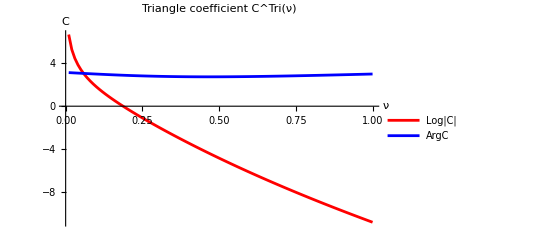

```mathematica
(*生成数据表格：{ν,Re,Im,Abs}*)
data=Table[{ν,Log[N[Abs[CTri[ν,10^(-5),0]]]],N[Arg[CTri[ν,10^(-5),0]]]},{ν,0.01,1,0.01}];

(*打印表格（前 20 行示例）*)
TableForm[data[[1;;20]],TableHeadings->{None,{"ν","Log|C|","ArgC"}}]

(*绘制三条曲线在同一图上*)
ListPlot[{data[[All,{1,2}]],data[[All,{1,3}]]},PlotLegends->{"Log|C|","ArgC"},AxesLabel->{"ν","C"},PlotLabel->"Triangle coefficient C^Tri(ν)",Joined->True,PlotStyle->{Red,Blue}]
```

### Triangle coefficient with analytic P2 (primary)

CTriSimp uses P2LSimp and P2PMSimp directly and therefore has no regulator argument. This is the primary Triangle result.

```mathematica
CTriSimp[n_,t_]:=(Gamma[-I n]^4/(4 π)^(7/2))*(P1[n]*P2LSimp[n]*IL[n,t]+2*P1[n]*P2PMSimp[n]*IP[n,t])
```

### Numerical inspection of the analytic result

ν | Log|C| | ArgC
1/100 | 6.66847 | 3.12618
1/50 | 5.27407 | 3.1108
3/100 | 4.44969 | 3.09548
1/25 | 3.85562 | 3.08024
1/20 | 3.38549 | 3.06511
3/50 | 2.99199 | 3.05012
7/100 | 2.65001 | 3.0353
2/25 | 2.34461 | 3.02067
9/100 | 2.06626 | 3.00625
1/10 | 1.80852 | 2.99208
11/100 | 1.56687 | 2.97816
3/25 | 1.33803 | 2.96453
13/100 | 1.11956 | 2.9512
7/50 | 0.909629 | 2.93819
3/20 | 0.706806 | 2.92552
4/25 | 0.509987 | 2.9132
17/100 | 0.318296 | 2.90126
9/50 | 0.131035 | 2.88969
19/100 | -0.0523581 | 2.87851
1/5 | -0.23234 | 2.86773

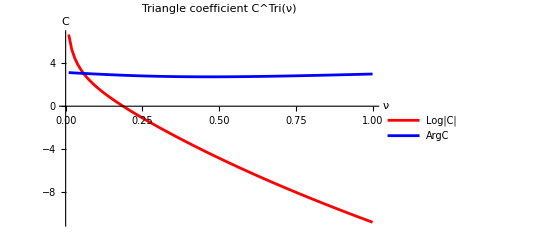

```mathematica
(*生成数据表格：{ν,Re,Im,Abs}*)
data=Table[{ν,Log[N[Abs[CTriSimp[ν,0]]]],N[Arg[CTriSimp[ν,0]]]},{ν,1/100,1,1/100}];

(*打印表格（前 20 行示例）*)
TableForm[data[[1;;20]],TableHeadings->{None,{"ν","Log|C|","ArgC"}}]

(*绘制三条曲线在同一图上*)
ListPlot[{data[[All,{1,2}]],data[[All,{1,3}]]},PlotLegends->{"Log|C|","ArgC"},AxesLabel->{"ν","C"},PlotLabel->"Triangle coefficient C^Tri(ν)",Joined->True,PlotStyle->{Red,Blue}]
```

## Box diagram

### Longitudinal seed check

SL is the original reduced longitudinal expression used as a consistency check before assembling the full Box angular factors.

```mathematica
(*可靠性检验*)
SL[nu_,theta1_]:=Module[{s1=Sin[theta1],c1=Cos[theta1],x=-I nu,beta},beta=((-1/2+I nu)^2)/(nu^2+1/4);
(*按表达式逐项相加*)(s1^2/2)*J0[0,0,x]+(beta c1^2+beta s1^2/2)*J0[0,2,x]+(beta^2 c1^2-beta c1^2-(beta s1^2)/2+s1^2/2)*J2[0,2,x]+(beta^2 c1^2+(beta^2 s1^2)/2+c1^2+s1^2/2)*J1[1,2,x]+(beta^2 c1^2-(beta^2 s1^2)/2-c1^2+s1^2/2)*J3[1,2,x]+((beta^2 s1^2)/2+c1^2)*J0[2,2,x]+(beta^2 c1^2-(beta^2 s1^2)/2-c1^2+s1^2/2)*J2[2,2,x]]
```

```mathematica
FullSimplify[SL[x,t]]
```

(2^(-4-4 ⅈ x) (3 ⅈ-2 x)^2 Gamma[-3/2-2 ⅈ x] Gamma[3+2 ⅈ x] Sinh[π x]^2)/(π (1+(3 ⅈ-2 x) x)^2)

### Longitudinal-longitudinal channel

SLL keeps the original coefficient-level construction in terms of the shared J0 through J3 seeds.

```mathematica
SLL[nu_,theta1_,theta3_,phi3_]:=Module[{s1=Sin[theta1],c1=Cos[theta1],s3=Sin[theta3],c3=Cos[theta3],sp=Sin[phi3],cp=Cos[phi3],x=-I nu,beta,A,B,C1,D1,E1,F,G,H,I9},(*由 nu 计算 beta*)beta=((-1/2+I nu)^2)/(nu^2+1/4);
(*系数 A (J0(0,0))*)A=(beta cp^2 s1^2 s3^2)/8-(beta s1^2 s3^2 sp^2)/8+(c1 c3 cp s1 s3)/2+(3 cp^2 s1^2 s3^2)/8+(s1^2 s3^2 sp^2)/8;
(*系数 B (J2(0,0))*)B=(beta c1 c3 cp s1 s3)/2-(beta cp^2 s1^2 s3^2)/8+(beta s1^2 s3^2 sp^2)/8-(c1 c3 cp s1 s3)/2+(cp^2 s1^2 s3^2)/8-(s1^2 s3^2 sp^2)/8;
(*系数 C (J0(0,2))*)C1=(beta^2 c1 c3 cp s1 s3)/2+beta c1^2 c3^2+(beta c1 c3 cp s1 s3)/2+(3 beta cp^2 s1^2 s3^2)/8+(beta s1^2 s3^2 sp^2)/8+(c1 c3 cp s1 s3)/2+(cp^2 s1^2 s3^2)/8-(s1^2 s3^2 sp^2)/8;
(*系数 D (J2(0,2))*)D1=beta^2 c1^2 c3^2-(beta^2 c1 c3 cp s1 s3)/2-beta c1^2 c3^2+beta c1 c3 cp s1 s3-(3 beta cp^2 s1^2 s3^2)/8-(beta s1^2 s3^2 sp^2)/8-(c1 c3 cp s1 s3)/2+(3 cp^2 s1^2 s3^2)/8+(s1^2 s3^2 sp^2)/8;
(*系数 E (J1(1,2))*)E1=(beta^2 c1^2 cp^2 s3^2)/2+(beta^2 c1^2 s3^2 sp^2)/2+2 beta^2 c1 c3 cp s1 s3+(beta^2 c3^2 s1^2)/2+2 beta c1^2 c3^2-beta c1^2 cp^2 s3^2-beta c1^2 s3^2 sp^2-beta c1 c3 cp s1 s3-beta c3^2 s1^2+(3 beta cp^2 s1^2 s3^2)/4+(beta s1^2 s3^2 sp^2)/4+(c1^2 cp^2 s3^2)/2+(c1^2 s3^2 sp^2)/2+2 c1 c3 cp s1 s3+(c3^2 s1^2)/2+(cp^2 s1^2 s3^2)/4-(s1^2 s3^2 sp^2)/4;
(*系数 F (J3(1,2))*)F=2 beta^2 c1^2 c3^2-(beta^2 c1^2 cp^2 s3^2)/2-(beta^2 c1^2 s3^2 sp^2)/2-2 beta^2 c1 c3 cp s1 s3-(beta^2 c3^2 s1^2)/2-2 beta c1^2 c3^2+beta c1^2 cp^2 s3^2+beta c1^2 s3^2 sp^2+4 beta c1 c3 cp s1 s3+beta c3^2 s1^2-(3 beta cp^2 s1^2 s3^2)/4-(beta s1^2 s3^2 sp^2)/4-(c1^2 cp^2 s3^2)/2-(c1^2 s3^2 sp^2)/2-2 c1 c3 cp s1 s3-(c3^2 s1^2)/2+(3 cp^2 s1^2 s3^2)/4+(s1^2 s3^2 sp^2)/4;
(*系数 G (J0(2,2))*)G=(3 beta^2 cp^2 s1^2 s3^2)/8+(beta^2 s1^2 s3^2 sp^2)/8+beta c1 c3 cp s1 s3+(beta cp^2 s1^2 s3^2)/8-(beta s1^2 s3^2 sp^2)/8+c1^2 c3^2+(c1 c3 cp s1 s3)/2;
(*系数 H (J2(2,2))*)H=(beta^2 c1^2 cp^2 s3^2)/2+(beta^2 c1^2 s3^2 sp^2)/2+2 beta^2 c1 c3 cp s1 s3+(beta^2 c3^2 s1^2)/2-(3 beta^2 cp^2 s1^2 s3^2)/4-(beta^2 s1^2 s3^2 sp^2)/4+2 beta c1^2 c3^2-beta c1^2 cp^2 s3^2-beta c1^2 s3^2 sp^2-(7 beta c1 c3 cp s1 s3)/2-beta c3^2 s1^2+(5 beta cp^2 s1^2 s3^2)/8+(3 beta s1^2 s3^2 sp^2)/8-2 c1^2 c3^2+(c1^2 cp^2 s3^2)/2+(c1^2 s3^2 sp^2)/2+(3 c1 c3 cp s1 s3)/2+(c3^2 s1^2)/2+(cp^2 s1^2 s3^2)/8-(s1^2 s3^2 sp^2)/8;
(*系数 I (J4(2,2))*)I9=beta^2 c1^2 c3^2-(beta^2 c1^2 cp^2 s3^2)/2-(beta^2 c1^2 s3^2 sp^2)/2-2 beta^2 c1 c3 cp s1 s3-(beta^2 c3^2 s1^2)/2+(3 beta^2 cp^2 s1^2 s3^2)/8+(beta^2 s1^2 s3^2 sp^2)/8-2 beta c1^2 c3^2+beta c1^2 cp^2 s3^2+beta c1^2 s3^2 sp^2+4 beta c1 c3 cp s1 s3+beta c3^2 s1^2-(3 beta cp^2 s1^2 s3^2)/4-(beta s1^2 s3^2 sp^2)/4+c1^2 c3^2-(c1^2 cp^2 s3^2)/2-(c1^2 s3^2 sp^2)/2-2 c1 c3 cp s1 s3-(c3^2 s1^2)/2+(3 cp^2 s1^2 s3^2)/8+(s1^2 s3^2 sp^2)/8;
(*返回 S(LL)*)A*J0[0,0,x]+B*J2[0,0,x]+C1*J0[0,2,x]+D1*J2[0,2,x]+E1*J1[1,2,x]+F*J3[1,2,x]+G*J0[2,2,x]+H*J2[2,2,x]+I9*J4[2,2,x]]
```

```mathematica
Simplify[SLL[x,t1,0,0]]
```

((3 x^2 (1+3 Cos[2 t1]) Gamma[1-ⅈ x]^2 Gamma[5/2+ⅈ x]^2 Gamma[-7/2-2 ⅈ x])/Gamma[-1-ⅈ x]^2+(x^2 (1+3 Cos[2 t1]) Gamma[1-ⅈ x] Gamma[1/2+ⅈ x] Gamma[9/2+ⅈ x] Gamma[-7/2-2 ⅈ x])/Gamma[-3-ⅈ x]+1/2 Gamma[5+2 ⅈ x] ((x^2 (3+Cos[2 t1]) Gamma[1/2+ⅈ x]^2 Gamma[1/2-2 ⅈ x])/Gamma[1+2 ⅈ x]-(4 Cos[t1]^2 Gamma[1-ⅈ x]^2 Gamma[3/2+ⅈ x]^2 Gamma[-3/2-2 ⅈ x])/(Gamma[3+2 ⅈ x] Gamma[-ⅈ x]^2)-(4 x (-ⅈ+3 x+(-ⅈ+x) Cos[2 t1]) Gamma[1-ⅈ x] Gamma[1/2+ⅈ x] Gamma[3/2+ⅈ x] Gamma[-1/2-2 ⅈ x])/(Gamma[2+2 ⅈ x] Gamma[-ⅈ x]))-(4 x^2 (1+3 Cos[2 t1]) Gamma[1-ⅈ x]^2 Gamma[3/2+ⅈ x] Gamma[7/2+ⅈ x] Gamma[-7/2-2 ⅈ x])/(Gamma[-2-ⅈ x] Gamma[-ⅈ x])+(2 x Gamma[1-ⅈ x] Gamma[5/2+ⅈ x] Gamma[5+2 ⅈ x] ((-ⅈ+x+(-ⅈ+3 x) Cos[2 t1]) Gamma[1-ⅈ x] Gamma[3/2+ⅈ x] Gamma[-5/2-2 ⅈ x] Gamma[3+2 ⅈ x]+4 (-ⅈ+x) Cos[t1]^2 Gamma[1/2+ⅈ x] Gamma[-3/2-2 ⅈ x] Gamma[4+2 ⅈ x] Gamma[-ⅈ x]))/(Gamma[-1-ⅈ x] Gamma[3+2 ⅈ x] Gamma[4+2 ⅈ x] Gamma[-ⅈ x])+(4 x Gamma[1-ⅈ x] Gamma[1/2+ⅈ x] Gamma[7/2+ⅈ x] Gamma[-5/2-2 ⅈ x] Gamma[5+2 ⅈ x] ((ⅈ-2 x) Cos[t1]^2+x Sin[t1]^2))/(Gamma[-2-ⅈ x] Gamma[4+2 ⅈ x]))/(2 (ⅈ-2 x)^2 Gamma[1-ⅈ x]^2 Gamma[5+2 ⅈ x])

```mathematica
FullSimplify[Simplify[SLL[x,t1,0,0]]]
```

(2^(-4-4 ⅈ x) (3+2 ⅈ x) (-4+x (-5 ⅈ+2 x)+x (-ⅈ+2 x) Cos[2 t1]) Gamma[-3/2-2 ⅈ x] Gamma[2+2 ⅈ x] Sinh[π x]^2)/(π (ⅈ-2 x)^2 (-ⅈ+x) (-2 ⅈ+x))

```mathematica
FullSimplify[Simplify[SLL[x,0,t2,0]]]
```

(2^(-4-4 ⅈ x) (3+2 ⅈ x) (-4+x (-5 ⅈ+2 x)+x (-ⅈ+2 x) Cos[2 t2]) Gamma[-3/2-2 ⅈ x] Gamma[2+2 ⅈ x] Sinh[π x]^2)/(π (ⅈ-2 x)^2 (-ⅈ+x) (-2 ⅈ+x))

```mathematica
FullSimplify[Simplify[SLL[x,t1,t2,0]]]
```

1/(π (ⅈ-2 x)^2 (-1-ⅈ x) (-2 ⅈ+x))4^(-3-2 ⅈ x) (-3 ⅈ+2 x) Gamma[-3/2-2 ⅈ x] Gamma[2+2 ⅈ x] (-19+8 x (-3 ⅈ+x)+(3+4 ⅈ x) Cos[2 t1]+8 x (-ⅈ+x) Cos[2 (t1+t2)]+Cos[2 t2] (4 ⅈ x+6 Sin[t1]^2)) Sinh[π x]^2

```mathematica
FullSimplify[(1/(π (ⅈ-2 x)^2 (-1-ⅈ x) (-2 ⅈ+x))4^(-3-2 ⅈ x) (-3 ⅈ+2 x) Gamma[-3/2-2 ⅈ x] Gamma[2+2 ⅈ x] (-19+8 x (-3 ⅈ+x)+(3+4 ⅈ x) Cos[2 t1]+8 x (-ⅈ+x) Cos[2 (t1+t2)]+Cos[2 t2] (4 ⅈ x+6 Sin[t1]^2)) Sinh[π x]^2)/(1/(π (ⅈ-2 x)^2 (-1-ⅈ x) (-2 ⅈ+x))4^(-3-2 ⅈ x) (-3 ⅈ+2 x) Gamma[-3/2-2 ⅈ x] Gamma[2+2 ⅈ x] (-19+8 x (-3 ⅈ+x)+(3+4 ⅈ x) Cos[2 t2]+8 x (-ⅈ+x) Cos[2 (t2+t1)]+Cos[2 t1] (4 ⅈ x+6 Sin[t2]^2)) Sinh[π x]^2)]
```

1

```mathematica
FullSimplify[Simplify[SLL[x,t1,t2,Pi/2]]]
```

1/(π (-ⅈ+x) (-2 ⅈ+x) (-ⅈ+2 x))2^(-8-4 ⅈ x) (-3 ⅈ+2 x) (-5 ⅈ+4 x) (-7 ⅈ+4 x) (-13+2 x (-7 ⅈ+2 x)+(-3-6 ⅈ x+4 x^2) Cos[2 t2]+Cos[2 t1] (-3-6 ⅈ x+4 x^2+(3+2 ⅈ x+4 x^2) Cos[2 t2])) Gamma[-7/2-2 ⅈ x] Gamma[1+2 ⅈ x] Sinh[π x]^2

```mathematica
FullSimplify[(1/(π (-ⅈ+x) (-2 ⅈ+x) (-ⅈ+2 x))2^(-8-4 ⅈ x) (-3 ⅈ+2 x) (-5 ⅈ+4 x) (-7 ⅈ+4 x) (-13+2 x (-7 ⅈ+2 x)+(-3-6 ⅈ x+4 x^2) Cos[2 t2]+Cos[2 t1] (-3-6 ⅈ x+4 x^2+(3+2 ⅈ x+4 x^2) Cos[2 t2])) Gamma[-7/2-2 ⅈ x] Gamma[1+2 ⅈ x] Sinh[π x]^2)/(1/(π (-ⅈ+x) (-2 ⅈ+x) (-ⅈ+2 x))2^(-8-4 ⅈ x) (-3 ⅈ+2 x) (-5 ⅈ+4 x) (-7 ⅈ+4 x) (-13+2 x (-7 ⅈ+2 x)+(-3-6 ⅈ x+4 x^2) Cos[2 t1]+Cos[2 t2] (-3-6 ⅈ x+4 x^2+(3+2 ⅈ x+4 x^2) Cos[2 t1])) Gamma[-7/2-2 ⅈ x] Gamma[1+2 ⅈ x] Sinh[π x]^2)]
```

1

```mathematica
FullSimplify[Simplify[SLL[x,t1,t2,Pi/3]]]
```

1/(π (-ⅈ+2 x) (-2+x (-3 ⅈ+x)))2^(-9-4 ⅈ x) (-3 ⅈ+2 x) (-5 ⅈ+4 x) (-7 ⅈ+4 x) Gamma[-7/2-2 ⅈ x] Gamma[1+2 ⅈ x] (-29+x (-33 ⅈ+10 x)+(-3+x (-7 ⅈ+6 x)) Cos[2 t2]+Cos[2 t1] (-3+x (-7 ⅈ+6 x)+(3+x (-ⅈ+10 x)) Cos[2 t2])-8 x (-ⅈ+x) Sin[2 t1] Sin[2 t2]) Sinh[π x]^2

```mathematica
FullSimplify[(1/(π (-ⅈ+2 x) (-2+x (-3 ⅈ+x)))2^(-9-4 ⅈ x) (-3 ⅈ+2 x) (-5 ⅈ+4 x) (-7 ⅈ+4 x) Gamma[-7/2-2 ⅈ x] Gamma[1+2 ⅈ x] (-29+x (-33 ⅈ+10 x)+(-3+x (-7 ⅈ+6 x)) Cos[2 t2]+Cos[2 t1] (-3+x (-7 ⅈ+6 x)+(3+x (-ⅈ+10 x)) Cos[2 t2])-8 x (-ⅈ+x) Sin[2 t1] Sin[2 t2]) Sinh[π x]^2)/(1/(π (-ⅈ+2 x) (-2+x (-3 ⅈ+x)))2^(-9-4 ⅈ x) (-3 ⅈ+2 x) (-5 ⅈ+4 x) (-7 ⅈ+4 x) Gamma[-7/2-2 ⅈ x] Gamma[1+2 ⅈ x] (-29+x (-33 ⅈ+10 x)+(-3+x (-7 ⅈ+6 x)) Cos[2 t1]+Cos[2 t2] (-3+x (-7 ⅈ+6 x)+(3+x (-ⅈ+10 x)) Cos[2 t1])-8 x (-ⅈ+x) Sin[2 t2] Sin[2 t1]) Sinh[π x]^2)]
```

1

```mathematica
FullSimplify[Simplify[SLL[x,t1,t2,Pi]]]
```

1/(π (ⅈ-2 x)^2 (-ⅈ+x) (-2 ⅈ+x))2^(-6-4 ⅈ x) (3+2 ⅈ x) Gamma[-3/2-2 ⅈ x] Gamma[2+2 ⅈ x] (-19+8 x (-3 ⅈ+x)+(3+4 ⅈ x) Cos[2 t2]+Cos[2 t1] (3+4 ⅈ x+(-3+8 x (-ⅈ+x)) Cos[2 t2])+8 x (-ⅈ+x) Sin[2 t1] Sin[2 t2]) Sinh[π x]^2

```mathematica
Simplify[SLL[x,t1,t2,p]]
```

(1/(8 Gamma[-1-ⅈ x]^2)3 x^2 (8+4 Cos[2 p]-2 Cos[2 (p-t1)]+24 Cos[2 t1]-2 Cos[2 (p+t1)]-16 Cos[p+2 t1-2 t2]-2 Cos[2 (p-t2)]+Cos[2 (p-t1-t2)]+36 Cos[2 (t1-t2)]+Cos[2 (p+t1-t2)]+24 Cos[2 t2]-2 Cos[2 (p+t2)]+Cos[2 (p-t1+t2)]+36 Cos[2 (t1+t2)]+Cos[2 (p+t1+t2)]-16 Cos[p-2 t1+2 t2]+16 Cos[p-2 (t1+t2)]+16 Cos[p+2 (t1+t2)]) Gamma[1-ⅈ x]^2 Gamma[5/2+ⅈ x]^2 Gamma[-7/2-2 ⅈ x]-1/(2 Gamma[-2-ⅈ x] Gamma[-ⅈ x])x^2 (8+4 Cos[2 p]-2 Cos[2 (p-t1)]+24 Cos[2 t1]-2 Cos[2 (p+t1)]-16 Cos[p+2 t1-2 t2]-2 Cos[2 (p-t2)]+Cos[2 (p-t1-t2)]+36 Cos[2 (t1-t2)]+Cos[2 (p+t1-t2)]+24 Cos[2 t2]-2 Cos[2 (p+t2)]+Cos[2 (p-t1+t2)]+36 Cos[2 (t1+t2)]+Cos[2 (p+t1+t2)]-16 Cos[p-2 t1+2 t2]+16 Cos[p-2 (t1+t2)]+16 Cos[p+2 (t1+t2)]) Gamma[1-ⅈ x]^2 Gamma[3/2+ⅈ x] Gamma[7/2+ⅈ x] Gamma[-7/2-2 ⅈ x]-1/(Gamma[-2-ⅈ x] Gamma[4+2 ⅈ x])8 x Gamma[1-ⅈ x] Gamma[1/2+ⅈ x] Gamma[7/2+ⅈ x] Gamma[-5/2-2 ⅈ x] Gamma[5+2 ⅈ x] (Cos[t1]^2 (-ⅈ+x+(-ⅈ+3 x) Cos[2 t2])-(ⅈ+6 x) Cos[p] Cos[t1] Cos[t2] Sin[t1] Sin[t2]+Sin[t1]^2 (-2 x Cos[t2]^2+1/2 (ⅈ+2 x+ⅈ Cos[2 p]) Sin[t2]^2))+1/Gamma[-3-ⅈ x]2 x^2 Gamma[1-ⅈ x] Gamma[1/2+ⅈ x] Gamma[9/2+ⅈ x] Gamma[-7/2-2 ⅈ x] (Cos[t1]^2 (2+6 Cos[2 t2])-4 Cos[t2]^2 Sin[t1]^2+3 Cos[p]^2 Sin[t1]^2 Sin[t2]^2+Sin[p]^2 Sin[t1]^2 Sin[t2]^2-4 Cos[p] Sin[2 t1] Sin[2 t2])+1/(Gamma[-1-ⅈ x] Gamma[3+2 ⅈ x] Gamma[4+2 ⅈ x] Gamma[-ⅈ x])4 x Gamma[1-ⅈ x] Gamma[5/2+ⅈ x] Gamma[5+2 ⅈ x] (1/16 (-12 ⅈ+8 x+4 ⅈ Cos[2 p]-2 ⅈ Cos[2 (p-t1)]-20 ⅈ Cos[2 t1]+24 x Cos[2 t1]-2 ⅈ Cos[2 (p+t1)]-2 ⅈ Cos[p+2 t1-2 t2]-12 x Cos[p+2 t1-2 t2]-2 ⅈ Cos[2 (p-t2)]+ⅈ Cos[2 (p-t1-t2)]-6 ⅈ Cos[2 (t1-t2)]+36 x Cos[2 (t1-t2)]+ⅈ Cos[2 (p+t1-t2)]-20 ⅈ Cos[2 t2]+24 x Cos[2 t2]-2 ⅈ Cos[2 (p+t2)]+ⅈ Cos[2 (p-t1+t2)]-6 ⅈ Cos[2 (t1+t2)]+36 x Cos[2 (t1+t2)]+ⅈ Cos[2 (p+t1+t2)]-2 ⅈ Cos[p-2 t1+2 t2]-12 x Cos[p-2 t1+2 t2]+2 ⅈ Cos[p-2 (t1+t2)]+12 x Cos[p-2 (t1+t2)]+2 ⅈ Cos[p+2 (t1+t2)]+12 x Cos[p+2 (t1+t2)]) Gamma[1-ⅈ x] Gamma[3/2+ⅈ x] Gamma[-5/2-2 ⅈ x] Gamma[3+2 ⅈ x]+Gamma[1/2+ⅈ x] Gamma[-3/2-2 ⅈ x] Gamma[4+2 ⅈ x] Gamma[-ⅈ x] (8 (-ⅈ+x) Cos[t1]^2 Cos[t2]^2+(4 ⅈ+x) Cos[p]^2 Sin[t1]^2 Sin[t2]^2+3 x Sin[p]^2 Sin[t1]^2 Sin[t2]^2-ⅈ Cos[p] Sin[2 t1] Sin[2 t2]))+1/(4 Gamma[-ⅈ x]^2)Gamma[5+2 ⅈ x] (-1/Gamma[2+2 ⅈ x]x (-12 ⅈ+72 x+4 ⅈ Cos[2 p]-2 ⅈ Cos[2 (p-t1)]-20 ⅈ Cos[2 t1]+24 x Cos[2 t1]-2 ⅈ Cos[2 (p+t1)]-2 ⅈ Cos[p+2 t1-2 t2]+4 x Cos[p+2 t1-2 t2]-2 ⅈ Cos[2 (p-t2)]+ⅈ Cos[2 (p-t1-t2)]-6 ⅈ Cos[2 (t1-t2)]+4 x Cos[2 (t1-t2)]+ⅈ Cos[2 (p+t1-t2)]-20 ⅈ Cos[2 t2]+24 x Cos[2 t2]-2 ⅈ Cos[2 (p+t2)]+ⅈ Cos[2 (p-t1+t2)]-6 ⅈ Cos[2 (t1+t2)]+4 x Cos[2 (t1+t2)]+ⅈ Cos[2 (p+t1+t2)]-2 ⅈ Cos[p-2 t1+2 t2]+4 x Cos[p-2 t1+2 t2]+2 ⅈ Cos[p-2 (t1+t2)]-4 x Cos[p-2 (t1+t2)]+2 ⅈ Cos[p+2 (t1+t2)]-4 x Cos[p+2 (t1+t2)]) Gamma[1-ⅈ x] Gamma[1/2+ⅈ x] Gamma[3/2+ⅈ x] Gamma[-1/2-2 ⅈ x] Gamma[-ⅈ x]+(4 x^2 Gamma[1/2+ⅈ x]^2 Gamma[1/2-2 ⅈ x] Gamma[-ⅈ x]^2 (2 Cos[t1]^2 (3+Cos[2 t2])+Sin[t1]^2 (4 Cos[t2]^2+(2+Cos[2 p]) Sin[t2]^2)))/Gamma[1+2 ⅈ x]-1/Gamma[3+2 ⅈ x]16 Gamma[1-ⅈ x]^2 Gamma[3/2+ⅈ x]^2 Gamma[-3/2-2 ⅈ x] (2 Cos[t1]^2 Cos[t2]^2-(-2-4 ⅈ x+3 x^2) Cos[p]^2 Sin[t1]^2 Sin[t2]^2-x^2 Sin[p]^2 Sin[t1]^2 Sin[t2]^2+(1+ⅈ x) Cos[p] Sin[2 t1] Sin[2 t2])))/(8 (ⅈ-2 x)^2 Gamma[1-ⅈ x]^2 Gamma[5+2 ⅈ x])

```mathematica
FullSimplify[(1/(8 Gamma[-1-ⅈ x]^2)3 x^2 (8+4 Cos[2 p]-2 Cos[2 (p-t1)]+24 Cos[2 t1]-2 Cos[2 (p+t1)]-16 Cos[p+2 t1-2 t2]-2 Cos[2 (p-t2)]+Cos[2 (p-t1-t2)]+36 Cos[2 (t1-t2)]+Cos[2 (p+t1-t2)]+24 Cos[2 t2]-2 Cos[2 (p+t2)]+Cos[2 (p-t1+t2)]+36 Cos[2 (t1+t2)]+Cos[2 (p+t1+t2)]-16 Cos[p-2 t1+2 t2]+16 Cos[p-2 (t1+t2)]+16 Cos[p+2 (t1+t2)]) Gamma[1-ⅈ x]^2 Gamma[5/2+ⅈ x]^2 Gamma[-7/2-2 ⅈ x]-1/(2 Gamma[-2-ⅈ x] Gamma[-ⅈ x])x^2 (8+4 Cos[2 p]-2 Cos[2 (p-t1)]+24 Cos[2 t1]-2 Cos[2 (p+t1)]-16 Cos[p+2 t1-2 t2]-2 Cos[2 (p-t2)]+Cos[2 (p-t1-t2)]+36 Cos[2 (t1-t2)]+Cos[2 (p+t1-t2)]+24 Cos[2 t2]-2 Cos[2 (p+t2)]+Cos[2 (p-t1+t2)]+36 Cos[2 (t1+t2)]+Cos[2 (p+t1+t2)]-16 Cos[p-2 t1+2 t2]+16 Cos[p-2 (t1+t2)]+16 Cos[p+2 (t1+t2)]) Gamma[1-ⅈ x]^2 Gamma[3/2+ⅈ x] Gamma[7/2+ⅈ x] Gamma[-7/2-2 ⅈ x]-1/(Gamma[-2-ⅈ x] Gamma[4+2 ⅈ x])8 x Gamma[1-ⅈ x] Gamma[1/2+ⅈ x] Gamma[7/2+ⅈ x] Gamma[-5/2-2 ⅈ x] Gamma[5+2 ⅈ x] (Cos[t1]^2 (-ⅈ+x+(-ⅈ+3 x) Cos[2 t2])-(ⅈ+6 x) Cos[p] Cos[t1] Cos[t2] Sin[t1] Sin[t2]+Sin[t1]^2 (-2 x Cos[t2]^2+1/2 (ⅈ+2 x+ⅈ Cos[2 p]) Sin[t2]^2))+1/Gamma[-3-ⅈ x] 2 x^2 Gamma[1-ⅈ x] Gamma[1/2+ⅈ x] Gamma[9/2+ⅈ x] Gamma[-7/2-2 ⅈ x] (Cos[t1]^2 (2+6 Cos[2 t2])-4 Cos[t2]^2 Sin[t1]^2+3 Cos[p]^2 Sin[t1]^2 Sin[t2]^2+Sin[p]^2 Sin[t1]^2 Sin[t2]^2-4 Cos[p] Sin[2 t1] Sin[2 t2])+1/(Gamma[-1-ⅈ x] Gamma[3+2 ⅈ x] Gamma[4+2 ⅈ x] Gamma[-ⅈ x])4 x Gamma[1-ⅈ x] Gamma[5/2+ⅈ x] Gamma[5+2 ⅈ x] (1/16 (-12 ⅈ+8 x+4 ⅈ Cos[2 p]-2 ⅈ Cos[2 (p-t1)]-20 ⅈ Cos[2 t1]+24 x Cos[2 t1]-2 ⅈ Cos[2 (p+t1)]-2 ⅈ Cos[p+2 t1-2 t2]-12 x Cos[p+2 t1-2 t2]-2 ⅈ Cos[2 (p-t2)]+ⅈ Cos[2 (p-t1-t2)]-6 ⅈ Cos[2 (t1-t2)]+36 x Cos[2 (t1-t2)]+ⅈ Cos[2 (p+t1-t2)]-20 ⅈ Cos[2 t2]+24 x Cos[2 t2]-2 ⅈ Cos[2 (p+t2)]+ⅈ Cos[2 (p-t1+t2)]-6 ⅈ Cos[2 (t1+t2)]+36 x Cos[2 (t1+t2)]+ⅈ Cos[2 (p+t1+t2)]-2 ⅈ Cos[p-2 t1+2 t2]-12 x Cos[p-2 t1+2 t2]+2 ⅈ Cos[p-2 (t1+t2)]+12 x Cos[p-2 (t1+t2)]+2 ⅈ Cos[p+2 (t1+t2)]+12 x Cos[p+2 (t1+t2)]) Gamma[1-ⅈ x] Gamma[3/2+ⅈ x] Gamma[-5/2-2 ⅈ x] Gamma[3+2 ⅈ x]+Gamma[1/2+ⅈ x] Gamma[-3/2-2 ⅈ x] Gamma[4+2 ⅈ x] Gamma[-ⅈ x] (8 (-ⅈ+x) Cos[t1]^2 Cos[t2]^2+(4 ⅈ+x) Cos[p]^2 Sin[t1]^2 Sin[t2]^2+3 x Sin[p]^2 Sin[t1]^2 Sin[t2]^2-ⅈ Cos[p] Sin[2 t1] Sin[2 t2]))+1/(4 Gamma[-ⅈ x]^2)Gamma[5+2 ⅈ x] (-1/Gamma[2+2 ⅈ x]x (-12 ⅈ+72 x+4 ⅈ Cos[2 p]-2 ⅈ Cos[2 (p-t1)]-20 ⅈ Cos[2 t1]+24 x Cos[2 t1]-2 ⅈ Cos[2 (p+t1)]-2 ⅈ Cos[p+2 t1-2 t2]+4 x Cos[p+2 t1-2 t2]-2 ⅈ Cos[2 (p-t2)]+ⅈ Cos[2 (p-t1-t2)]-6 ⅈ Cos[2 (t1-t2)]+4 x Cos[2 (t1-t2)]+ⅈ Cos[2 (p+t1-t2)]-20 ⅈ Cos[2 t2]+24 x Cos[2 t2]-2 ⅈ Cos[2 (p+t2)]+ⅈ Cos[2 (p-t1+t2)]-6 ⅈ Cos[2 (t1+t2)]+4 x Cos[2 (t1+t2)]+ⅈ Cos[2 (p+t1+t2)]-2 ⅈ Cos[p-2 t1+2 t2]+4 x Cos[p-2 t1+2 t2]+2 ⅈ Cos[p-2 (t1+t2)]-4 x Cos[p-2 (t1+t2)]+2 ⅈ Cos[p+2 (t1+t2)]-4 x Cos[p+2 (t1+t2)]) Gamma[1-ⅈ x] Gamma[1/2+ⅈ x] Gamma[3/2+ⅈ x] Gamma[-1/2-2 ⅈ x] Gamma[-ⅈ x]+(4 x^2 Gamma[1/2+ⅈ x]^2 Gamma[1/2-2 ⅈ x] Gamma[-ⅈ x]^2 (2 Cos[t1]^2 (3+Cos[2 t2])+Sin[t1]^2 (4 Cos[t2]^2+(2+Cos[2 p]) Sin[t2]^2)))/Gamma[1+2 ⅈ x]-1/Gamma[3+2 ⅈ x] 16 Gamma[1-ⅈ x]^2 Gamma[3/2+ⅈ x]^2 Gamma[-3/2-2 ⅈ x] (2 Cos[t1]^2 Cos[t2]^2-(-2-4 ⅈ x+3 x^2) Cos[p]^2 Sin[t1]^2 Sin[t2]^2-x^2 Sin[p]^2 Sin[t1]^2 Sin[t2]^2+(1+ⅈ x) Cos[p] Sin[2 t1] Sin[2 t2])))/(8 (ⅈ-2 x)^2 Gamma[1-ⅈ x]^2 Gamma[5+2 ⅈ x])]
```

-1/(π (-ⅈ+x) (-2 ⅈ+x) (-ⅈ+2 x))4^(-3-2 ⅈ x) (-3 ⅈ+2 x) Gamma[-3/2-2 ⅈ x] Gamma[1+2 ⅈ x] (-16+x (-19 ⅈ+6 x)+x (-ⅈ+2 x) Cos[2 t2]+x (-ⅈ+2 x) Cos[2 t1] (1+3 Cos[2 t2])+4 (-3+x (-5 ⅈ+2 x)) Cos[2 p] Sin[t1]^2 Sin[t2]^2-8 x (-ⅈ+x) Cos[p] Sin[2 t1] Sin[2 t2]) Sinh[π x]^2

### Analytic longitudinal-longitudinal factor

SLLSimp is the explicit closed form used by the regulator-free Box coefficient.

```mathematica
SLLSimp[x_,t1_,t2_,p_]:=-1/(π (-ⅈ+x) (-2 ⅈ+x) (-ⅈ+2 x))4^(-3-2 ⅈ x) (-3 ⅈ+2 x) Gamma[-3/2-2 ⅈ x] Gamma[1+2 ⅈ x] (-16+x (-19 ⅈ+6 x)+x (-ⅈ+2 x) Cos[2 t2]+x (-ⅈ+2 x) Cos[2 t1] (1+3 Cos[2 t2])+4 (-3+x (-5 ⅈ+2 x)) Cos[2 p] Sin[t1]^2 Sin[t2]^2-8 x (-ⅈ+x) Cos[p] Sin[2 t1] Sin[2 t2]) Sinh[π x]^2
```

```mathematica
FullSimplify[(-1/(π (-ⅈ+x) (-2 ⅈ+x) (-ⅈ+2 x))4^(-3-2 ⅈ x) (-3 ⅈ+2 x) Gamma[-3/2-2 ⅈ x] Gamma[1+2 ⅈ x] (-16+x (-19 ⅈ+6 x)+x (-ⅈ+2 x) Cos[2 t2]+x (-ⅈ+2 x) Cos[2 t1] (1+3 Cos[2 t2])+4 (-3+x (-5 ⅈ+2 x)) Cos[2 p] Sin[t1]^2 Sin[t2]^2-8 x (-ⅈ+x) Cos[p] Sin[2 t1] Sin[2 t2]) Sinh[π x]^2)/(-1/(π (-ⅈ+x) (-2 ⅈ+x) (-ⅈ+2 x))4^(-3-2 ⅈ x) (-3 ⅈ+2 x) Gamma[-3/2-2 ⅈ x] Gamma[1+2 ⅈ x] (-16+x (-19 ⅈ+6 x)+x (-ⅈ+2 x) Cos[2 t1]+x (-ⅈ+2 x) Cos[2 t2] (1+3 Cos[2 t1])+4 (-3+x (-5 ⅈ+2 x)) Cos[2 p] Sin[t2]^2 Sin[t1]^2-8 x (-ⅈ+x) Cos[p] Sin[2 t2] Sin[2 t1]) Sinh[π x]^2)]
```

1

### Transverse-transverse channel

SHH is the transverse-transverse angular factor in its original seed representation.

```mathematica
SHH[nu_, theta1_, theta3_, phi3_] := Module[
  {s1 = Sin[theta1], c1 = Cos[theta1],
   s3 = Sin[theta3], c3 = Cos[theta3],
   sp = Sin[phi3], cp = Cos[phi3],
   x = -I nu, beta,
   coeff000, coeff200, coeff002, coeff202, 
   coeff112, coeff312, coeff022, coeff222, coeff422},

  beta = ((-1/2 + I nu)^2)/(nu^2 + 1/4);

  (* 系数 coeff000 对应 J0(0,0) *)
  coeff000 = 
    (beta cp^2 c1^2 c3^2)/8 - (beta c1^2 c3^2 sp^2)/8 - (beta cp^2 c1^2)/8 + (beta c1^2 sp^2)/8 - 
    (beta cp^2 c3^2)/8 + (beta c3^2 sp^2)/8 + (beta cp^2)/8 - (beta sp^2)/8 + 
    (3 cp^2 c1^2 c3^2)/8 + (c1^2 c3^2 sp^2)/8 + (cp^2 c1^2)/8 + (3 c1^2 sp^2)/8 + 
    (c1 c3 cp s1 s3)/2 + (cp^2 c3^2)/8 + (3 c3^2 sp^2)/8 + (3 cp^2)/8 + sp^2/8;

  (* 系数 coeff200 对应 J2(0,0) *)
  coeff200 = 
    -(beta cp^2 c1^2 c3^2)/8 + (beta c1^2 c3^2 sp^2)/8 + (beta cp^2 c1^2)/8 - (beta c1^2 sp^2)/8 + 
    (beta c1 c3 cp s1 s3)/2 + (beta cp^2 c3^2)/8 - (beta c3^2 sp^2)/8 - (beta cp^2)/8 + (beta sp^2)/8 + 
    (cp^2 c1^2 c3^2)/8 - (c1^2 c3^2 sp^2)/8 - (cp^2 c1^2)/8 + (c1^2 sp^2)/8 - 
    (c1 c3 cp s1 s3)/2 - (cp^2 c3^2)/8 + (c3^2 sp^2)/8 + cp^2/8 - sp^2/8;

  (* 系数 coeff0200 对应 J0(0,2) *)
  coeff002 = 
    (beta^2 c1 c3 cp s1 s3)/2 + (3 beta cp^2 c1^2 c3^2)/8 + (beta c1^2 c3^2 sp^2)/8 + 
    (beta cp^2 c1^2)/8 + (3 beta c1^2 sp^2)/8 + (beta c1 c3 cp s1 s3)/2 + 
    (beta cp^2 c3^2)/8 + (3 beta c3^2 sp^2)/8 + (3 beta cp^2)/8 + beta s1^2 s3^2 + (beta sp^2)/8 + 
    (cp^2 c1^2 c3^2)/8 - (c1^2 c3^2 sp^2)/8 - (cp^2 c1^2)/8 + (c1^2 sp^2)/8 + 
    (c1 c3 cp s1 s3)/2 - (cp^2 c3^2)/8 + (c3^2 sp^2)/8 + cp^2/8 - sp^2/8;

  (* 系数 coeff0202 对应 J2(0,2) *)
  coeff202 = 
    -(beta^2 c1 c3 cp s1 s3)/2 + beta^2 s1^2 s3^2 - 
    (3 beta cp^2 c1^2 c3^2)/8 - (beta c1^2 c3^2 sp^2)/8 - (beta cp^2 c1^2)/8 - 
    (3 beta c1^2 sp^2)/8 + beta c1 c3 cp s1 s3 - (beta cp^2 c3^2)/8 - 
    (3 beta c3^2 sp^2)/8 - (3 beta cp^2)/8 - beta s1^2 s3^2 - (beta sp^2)/8 + 
    (3 cp^2 c1^2 c3^2)/8 + (c1^2 c3^2 sp^2)/8 + (cp^2 c1^2)/8 + (3 c1^2 sp^2)/8 - 
    (c1 c3 cp s1 s3)/2 + (cp^2 c3^2)/8 + (3 c3^2 sp^2)/8 + (3 cp^2)/8 + sp^2/8;

  (* 系数 coeff1201 对应 J1(1,2) *)
  coeff112 = 
    (beta^2 c1^2 s3^2)/2 + 2 beta^2 c1 c3 cp s1 s3 + (beta^2 c3^2 cp^2 s1^2)/2 + 
    (beta^2 c3^2 s1^2 sp^2)/2 + (beta^2 cp^2 s1^2)/2 + (beta^2 s1^2 sp^2)/2 + (beta^2 s3^2)/2 + 
    (3 beta cp^2 c1^2 c3^2)/4 + (beta c1^2 c3^2 sp^2)/4 + (beta cp^2 c1^2)/4 - 
    beta c1^2 s3^2 + (3 beta c1^2 sp^2)/4 - beta c1 c3 cp s1 s3 - 
    beta c3^2 cp^2 s1^2 + (beta cp^2 c3^2)/4 - beta c3^2 s1^2 sp^2 + (3 beta c3^2 sp^2)/4 - 
    beta cp^2 s1^2 + (3 beta cp^2)/4 + 2 beta s1^2 s3^2 - beta s1^2 sp^2 - beta s3^2 + 
    (beta sp^2)/4 + (cp^2 c1^2 c3^2)/4 - (c1^2 c3^2 sp^2)/4 - (cp^2 c1^2)/4 + 
    (c1^2 s3^2)/2 + (c1^2 sp^2)/4 + 2 c1 c3 cp s1 s3 + (c3^2 cp^2 s1^2)/2 - 
    (cp^2 c3^2)/4 + (c3^2 s1^2 sp^2)/2 + (c3^2 sp^2)/4 + (cp^2 s1^2)/2 + cp^2/4 + 
    (s1^2 sp^2)/2 + s3^2/2 - sp^2/4;

  (* 系数 coeff1203 对应 J3(1,2) *)
  coeff312 = 
    -(beta^2 c1^2 s3^2)/2 - 2 beta^2 c1 c3 cp s1 s3 - (beta^2 c3^2 cp^2 s1^2)/2 - 
    (beta^2 c3^2 s1^2 sp^2)/2 - (beta^2 cp^2 s1^2)/2 + 2 beta^2 s1^2 s3^2 - 
    (beta^2 s1^2 sp^2)/2 - (beta^2 s3^2)/2 - 
    (3 beta cp^2 c1^2 c3^2)/4 - (beta c1^2 c3^2 sp^2)/4 - (beta cp^2 c1^2)/4 + 
    beta c1^2 s3^2 - (3 beta c1^2 sp^2)/4 + 4 beta c1 c3 cp s1 s3 + 
    beta c3^2 cp^2 s1^2 - (beta cp^2 c3^2)/4 + beta c3^2 s1^2 sp^2 - (3 beta c3^2 sp^2)/4 + 
    beta cp^2 s1^2 - (3 beta cp^2)/4 - 2 beta s1^2 s3^2 + beta s1^2 sp^2 + beta s3^2 - 
    (beta sp^2)/4 + (3 cp^2 c1^2 c3^2)/4 + (c1^2 c3^2 sp^2)/4 + (cp^2 c1^2)/4 - 
    (c1^2 s3^2)/2 + (3 c1^2 sp^2)/4 - 2 c1 c3 cp s1 s3 - (c3^2 cp^2 s1^2)/2 + 
    (cp^2 c3^2)/4 - (c3^2 s1^2 sp^2)/2 + (3 c3^2 sp^2)/4 - (cp^2 s1^2)/2 + (3 cp^2)/4 - 
    (s1^2 sp^2)/2 - s3^2/2 + sp^2/4;

  (* 系数 coeff2200 对应 J0(2,2) *)
  coeff022 = 
    (3 beta^2 cp^2 c1^2 c3^2)/8 + (beta^2 c1^2 c3^2 sp^2)/8 + (beta^2 cp^2 c1^2)/8 + 
    (3 beta^2 c1^2 sp^2)/8 + (beta^2 cp^2 c3^2)/8 + (3 beta^2 c3^2 sp^2)/8 + 
    (3 beta^2 cp^2)/8 + (beta^2 sp^2)/8 + (beta cp^2 c1^2 c3^2)/8 - 
    (beta c1^2 c3^2 sp^2)/8 - (beta cp^2 c1^2)/8 + (beta c1^2 sp^2)/8 + 
    beta c1 c3 cp s1 s3 - (beta cp^2 c3^2)/8 + (beta c3^2 sp^2)/8 + (beta cp^2)/8 - 
    (beta sp^2)/8 + (c1 c3 cp s1 s3)/2 + s1^2 s3^2;

  (* 系数 coeff2202 对应 J2(2,2) *)
  coeff222 = 
    -(3 beta^2 cp^2 c1^2 c3^2)/4 - (beta^2 c1^2 c3^2 sp^2)/4 - (beta^2 cp^2 c1^2)/4 + 
    (beta^2 c1^2 s3^2)/2 - (3 beta^2 c1^2 sp^2)/4 + 2 beta^2 c1 c3 cp s1 s3 + 
    (beta^2 c3^2 cp^2 s1^2)/2 - (beta^2 cp^2 c3^2)/4 + (beta^2 c3^2 s1^2 sp^2)/2 - 
    (3 beta^2 c3^2 sp^2)/4 + (beta^2 cp^2 s1^2)/2 - (3 beta^2 cp^2)/4 + 
    (beta^2 s1^2 sp^2)/2 + (beta^2 s3^2)/2 - (beta^2 sp^2)/4 + 
    (5 beta cp^2 c1^2 c3^2)/8 + (3 beta c1^2 c3^2 sp^2)/8 + (3 beta cp^2 c1^2)/8 - 
    beta c1^2 s3^2 + (5 beta c1^2 sp^2)/8 - (7 beta c1 c3 cp s1 s3)/2 - 
    beta c3^2 cp^2 s1^2 + (3 beta cp^2 c3^2)/8 - beta c3^2 s1^2 sp^2 + (5 beta c3^2 sp^2)/8 - 
    beta cp^2 s1^2 + (5 beta cp^2)/8 + 2 beta s1^2 s3^2 - beta s1^2 sp^2 - beta s3^2 + 
    (3 beta sp^2)/8 + (cp^2 c1^2 c3^2)/8 - (c1^2 c3^2 sp^2)/8 - (cp^2 c1^2)/8 + 
    (c1^2 s3^2)/2 + (c1^2 sp^2)/8 + (3 c1 c3 cp s1 s3)/2 + (c3^2 cp^2 s1^2)/2 - 
    (cp^2 c3^2)/8 + (c3^2 s1^2 sp^2)/2 + (c3^2 sp^2)/8 + (cp^2 s1^2)/2 + cp^2/8 - 
    2 s1^2 s3^2 + (s1^2 sp^2)/2 + s3^2/2 - sp^2/8;

  (* 系数 coeff2204 对应 J4(2,2) *)
  coeff422 = 
    (3 beta^2 cp^2 c1^2 c3^2)/8 + (beta^2 c1^2 c3^2 sp^2)/8 + (beta^2 cp^2 c1^2)/8 - 
    (beta^2 c1^2 s3^2)/2 + (3 beta^2 c1^2 sp^2)/8 - 2 beta^2 c1 c3 cp s1 s3 - 
    (beta^2 c3^2 cp^2 s1^2)/2 + (beta^2 cp^2 c3^2)/8 - (beta^2 c3^2 s1^2 sp^2)/2 + 
    (3 beta^2 c3^2 sp^2)/8 - (beta^2 cp^2 s1^2)/2 + (3 beta^2 cp^2)/8 + 
    beta^2 s1^2 s3^2 - (beta^2 s1^2 sp^2)/2 - (beta^2 s3^2)/2 + (beta^2 sp^2)/8 - 
    (3 beta cp^2 c1^2 c3^2)/4 - (beta c1^2 c3^2 sp^2)/4 - (beta cp^2 c1^2)/4 + 
    beta c1^2 s3^2 - (3 beta c1^2 sp^2)/4 + 4 beta c1 c3 cp s1 s3 + 
    beta c3^2 cp^2 s1^2 - (beta cp^2 c3^2)/4 + beta c3^2 s1^2 sp^2 - (3 beta c3^2 sp^2)/4 + 
    beta cp^2 s1^2 - (3 beta cp^2)/4 - 2 beta s1^2 s3^2 + beta s1^2 sp^2 + beta s3^2 - 
    (beta sp^2)/4 + (3 cp^2 c1^2 c3^2)/8 + (c1^2 c3^2 sp^2)/8 + (cp^2 c1^2)/8 - 
    (c1^2 s3^2)/2 + (3 c1^2 sp^2)/8 - 2 c1 c3 cp s1 s3 - (c3^2 cp^2 s1^2)/2 + 
    (cp^2 c3^2)/8 - (c3^2 s1^2 sp^2)/2 + (3 c3^2 sp^2)/8 - (cp^2 s1^2)/2 + (3 cp^2)/8 + 
    s1^2 s3^2 - (s1^2 sp^2)/2 - s3^2/2 + sp^2/8;

  (* 组合所有项 *)
  coeff000 * J0[0, 0, x] +
  coeff200 * J2[0, 0, x] +
  coeff002 * J0[0, 2, x] +
  coeff202 * J2[0, 2, x] +
  coeff112 * J1[1, 2, x] +
  coeff312 * J3[1, 2, x] +
  coeff022 * J0[2, 2, x] +
  coeff222 * J2[2, 2, x] +
  coeff422 * J4[2, 2, x]
]
```

```mathematica
Simplify[SHH[x,t1,t2,p]]
```

1/16 (-((x^2 (8+4 Cos[2 p]-2 Cos[2 (p-t1)]+24 Cos[2 t1]-2 Cos[2 (p+t1)]-16 Cos[p+2 t1-2 t2]-2 Cos[2 (p-t2)]+Cos[2 (p-t1-t2)]+36 Cos[2 (t1-t2)]+Cos[2 (p+t1-t2)]+24 Cos[2 t2]-2 Cos[2 (p+t2)]+Cos[2 (p-t1+t2)]+36 Cos[2 (t1+t2)]+Cos[2 (p+t1+t2)]-16 Cos[p-2 t1+2 t2]+16 Cos[p-2 (t1+t2)]+16 Cos[p+2 (t1+t2)]) (-2 Gamma[-2-ⅈ x] Gamma[-1-ⅈ x]^2 Gamma[1-ⅈ x] Gamma[1/2+ⅈ x] Gamma[9/2+ⅈ x] Gamma[-7/2-2 ⅈ x] Gamma[1+2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x]^2+Gamma[-3-ⅈ x] (8 Gamma[-1-ⅈ x]^2 Gamma[1-ⅈ x]^2 Gamma[3/2+ⅈ x] Gamma[7/2+ⅈ x] Gamma[-7/2-2 ⅈ x] Gamma[1+2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x]+Gamma[-2-ⅈ x] (-6 Gamma[1-ⅈ x]^2 Gamma[5/2+ⅈ x]^2 Gamma[-7/2-2 ⅈ x] Gamma[1+2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x]^2-12 Gamma[-1-ⅈ x] Gamma[1-ⅈ x] Gamma[1/2+ⅈ x] Gamma[5/2+ⅈ x] Gamma[-3/2-2 ⅈ x] Gamma[1+2 ⅈ x] Gamma[5+2 ⅈ x] Gamma[-ⅈ x]^2+Gamma[-1-ⅈ x]^2 Gamma[5+2 ⅈ x] (12 Gamma[1-ⅈ x]^2 Gamma[3/2+ⅈ x]^2 Gamma[-3/2-2 ⅈ x] Gamma[1+2 ⅈ x]-Gamma[1/2+ⅈ x]^2 Gamma[1/2-2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x]^2)))))/(8 (ⅈ-2 x)^2 Gamma[-3-ⅈ x] Gamma[-2-ⅈ x] Gamma[-1-ⅈ x]^2 Gamma[1-ⅈ x]^2 Gamma[1+2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[5+2 ⅈ x] Gamma[-ⅈ x]^2))+1/((-ⅈ+2 x) Gamma[3+2 ⅈ x] Gamma[-ⅈ x]^2)8 Gamma[3/2+ⅈ x]^2 Gamma[-3/2-2 ⅈ x] (Cos[p]^2 (-ⅈ+x+x Cos[t2]^2+Cos[t1]^2 (x+(-ⅈ+x) Cos[t2]^2))+(x+(-ⅈ+x) Cos[t2]^2+Cos[t1]^2 (-ⅈ+x+x Cos[t2]^2)) Sin[p]^2+(-ⅈ+2 x) Cos[p] Cos[t1] Cos[t2] Sin[t1] Sin[t2])+(2 x (Gamma[-1-ⅈ x] Gamma[1/2+ⅈ x] Gamma[7/2+ⅈ x] Gamma[-5/2-2 ⅈ x] Gamma[2+2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x]^2+Gamma[-2-ⅈ x] (Gamma[-1-ⅈ x] Gamma[3/2+ⅈ x] Gamma[4+2 ⅈ x] (2 Gamma[1-ⅈ x] Gamma[3/2+ⅈ x] Gamma[-3/2-2 ⅈ x] Gamma[2+2 ⅈ x]+Gamma[1/2+ⅈ x] Gamma[-1/2-2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x])-Gamma[5/2+ⅈ x] Gamma[2+2 ⅈ x] Gamma[-ⅈ x] (Gamma[1-ⅈ x] Gamma[3/2+ⅈ x] Gamma[-5/2-2 ⅈ x] Gamma[3+2 ⅈ x]+2 Gamma[1/2+ⅈ x] Gamma[-3/2-2 ⅈ x] Gamma[4+2 ⅈ x] Gamma[-ⅈ x]))) Sin[t1] Sin[t2] (-4 Cos[p] Cos[t1] Cos[t2]+Cos[p]^2 Sin[t1] Sin[t2]-Sin[p]^2 Sin[t1] Sin[t2]))/((-ⅈ+2 x) Gamma[-2-ⅈ x] Gamma[-1-ⅈ x] Gamma[1-ⅈ x] Gamma[2+2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[4+2 ⅈ x] Gamma[-ⅈ x]^2)-(8 (-Gamma[1/2+ⅈ x] Gamma[5/2+ⅈ x] Gamma[-3/2-2 ⅈ x] Gamma[2+2 ⅈ x] Gamma[-ⅈ x]^2+Gamma[-1-ⅈ x] Gamma[3/2+ⅈ x] (Gamma[1-ⅈ x] Gamma[3/2+ⅈ x] Gamma[-3/2-2 ⅈ x] Gamma[2+2 ⅈ x]-Gamma[1/2+ⅈ x] Gamma[-1/2-2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x])) ((x (-ⅈ-2 x+4 x Cos[2 t1])+(1+ⅈ x-2 x^2+4 x^2 Cos[2 t1]) Cos[t2]^2+(-ⅈ+2 x) Cos[t1]^2 (ⅈ+x+x Cos[t2]^2)) Sin[p]^2+1/2 Cos[p]^2 (2+2 ⅈ x+4 x^2+2 x (-ⅈ-2 x+4 x Cos[2 t1]) Cos[t2]^2+(-ⅈ+2 x) Cos[t1]^2 (ⅈ+3 x+(ⅈ+x) Cos[2 t2])-16 x^2 Sin[t1]^2)-(-3+20 x^2) Cos[p] Cos[t1] Cos[t2] Sin[t1] Sin[t2]-(-1+8 x^2+(1+8 x^2) Cos[2 t1]) Sin[t2]^2))/((ⅈ-2 x)^2 Gamma[-1-ⅈ x] Gamma[1-ⅈ x] Gamma[2+2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x]^2)+(8 Gamma[1/2+ⅈ x] Gamma[5/2+ⅈ x] Gamma[-3/2-2 ⅈ x] ((ⅈ+2 x) Cos[p]^2 (ⅈ+x+x Cos[t2]^2+Cos[t1]^2 (x+(ⅈ+x) Cos[t2]^2))+1/8 (ⅈ+2 x) (8 ⅈ+18 x+(4 ⅈ+6 x) Cos[2 t1]+x Cos[2 (t1-t2)]+4 ⅈ Cos[2 t2]+6 x Cos[2 t2]+x Cos[2 (t1+t2)]) Sin[p]^2-(3+4 ⅈ x+4 x^2) Cos[p] Cos[t1] Cos[t2] Sin[t1] Sin[t2]+2 (ⅈ-2 x)^2 Sin[t1]^2 Sin[t2]^2))/((ⅈ-2 x)^2 Gamma[-1-ⅈ x] Gamma[1-ⅈ x] Gamma[3+2 ⅈ x])-(8 Gamma[1/2+ⅈ x] Gamma[3/2+ⅈ x] Gamma[-1/2-2 ⅈ x] ((-ⅈ+2 x) Cos[p]^2 (ⅈ+x+x Cos[t2]^2+Cos[t1]^2 (x+(ⅈ+x) Cos[t2]^2))-(-3+4 x^2) Cos[p] Cos[t1] Cos[t2] Sin[t1] Sin[t2]+(-ⅈ+2 x) ((x+(ⅈ+x) Cos[t2]^2+Cos[t1]^2 (ⅈ+x+x Cos[t2]^2)) Sin[p]^2+2 (ⅈ+2 x) Sin[t1]^2 Sin[t2]^2)))/((ⅈ-2 x)^2 Gamma[1-ⅈ x] Gamma[2+2 ⅈ x] Gamma[-ⅈ x])-(x (-2 Gamma[1-ⅈ x] Gamma[1/2+ⅈ x] Gamma[5/2+ⅈ x] Gamma[-3/2-2 ⅈ x] Gamma[1+2 ⅈ x] Gamma[-ⅈ x]^2+Gamma[-1-ⅈ x] (2 Gamma[1-ⅈ x]^2 Gamma[3/2+ⅈ x]^2 Gamma[-3/2-2 ⅈ x] Gamma[1+2 ⅈ x]-Gamma[1/2+ⅈ x]^2 Gamma[1/2-2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x]^2)) ((-ⅈ+2 x) Cos[p]^2 (38+10 Cos[2 t1]+3 Cos[2 (t1-t2)]+10 Cos[2 t2]+3 Cos[2 (t1+t2)])+(-ⅈ+2 x) (34+14 Cos[2 t1]+Cos[2 (t1-t2)]+14 Cos[2 t2]+Cos[2 (t1+t2)]) Sin[p]^2+64 (ⅈ+2 x) Sin[t1]^2 Sin[t2]^2-32 x Cos[p] Sin[2 t1] Sin[2 t2]))/(4 (ⅈ-2 x)^2 Gamma[-1-ⅈ x] Gamma[1-ⅈ x]^2 Gamma[1+2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x]^2)+(x (-6 Gamma[1-ⅈ x] Gamma[1/2+ⅈ x] Gamma[5/2+ⅈ x] Gamma[-3/2-2 ⅈ x] Gamma[1+2 ⅈ x] Gamma[-ⅈ x]^2+Gamma[-1-ⅈ x] (6 Gamma[1-ⅈ x]^2 Gamma[3/2+ⅈ x]^2 Gamma[-3/2-2 ⅈ x] Gamma[1+2 ⅈ x]-Gamma[1/2+ⅈ x]^2 Gamma[1/2-2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x]^2)) (Cos[p]^2 (-6 ⅈ+4 x+8 x Cos[2 t1]+2 (-ⅈ-2 x+4 x Cos[2 t1]) Cos[t2]^2+(-ⅈ+2 x) Cos[t1]^2 (5+3 Cos[2 t2]))+(-2 ⅈ-4 x+8 x Cos[2 t1]+2 (-3 ⅈ+2 x+4 x Cos[2 t1]) Cos[t2]^2+(-ⅈ+2 x) Cos[t1]^2 (7+Cos[2 t2])) Sin[p]^2-8 (-ⅈ+x+(ⅈ+3 x) Cos[2 t1]) Sin[t2]^2-16 x Cos[p] Sin[2 t1] Sin[2 t2]))/((ⅈ-2 x)^2 Gamma[-1-ⅈ x] Gamma[1-ⅈ x]^2 Gamma[1+2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x]^2)+(2 x (-Gamma[-1-ⅈ x] Gamma[1/2+ⅈ x] Gamma[7/2+ⅈ x] Gamma[-5/2-2 ⅈ x] Gamma[2+2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x]^2+Gamma[-2-ⅈ x] (Gamma[-1-ⅈ x] Gamma[3/2+ⅈ x] Gamma[4+2 ⅈ x] (2 Gamma[1-ⅈ x] Gamma[3/2+ⅈ x] Gamma[-3/2-2 ⅈ x] Gamma[2+2 ⅈ x]-Gamma[1/2+ⅈ x] Gamma[-1/2-2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x])+Gamma[5/2+ⅈ x] Gamma[2+2 ⅈ x] Gamma[-ⅈ x] (Gamma[1-ⅈ x] Gamma[3/2+ⅈ x] Gamma[-5/2-2 ⅈ x] Gamma[3+2 ⅈ x]-2 Gamma[1/2+ⅈ x] Gamma[-3/2-2 ⅈ x] Gamma[4+2 ⅈ x] Gamma[-ⅈ x]))) (Cos[p]^2 (7 ⅈ+2 x+8 x Cos[2 t1]+(ⅈ-2 x+8 x Cos[2 t1]) Cos[t2]^2+Cos[t1]^2 (ⅈ+6 x+(7 ⅈ+10 x) Cos[t2]^2))+(ⅈ-2 x+8 x Cos[2 t1]+(7 ⅈ+2 x+8 x Cos[2 t1]) Cos[t2]^2+Cos[t1]^2 (7 ⅈ+10 x+(ⅈ+6 x) Cos[t2]^2)) Sin[p]^2-8 (ⅈ+x+(-ⅈ+3 x) Cos[2 t1]) Sin[t2]^2-(ⅈ+14 x) Cos[p] Sin[2 t1] Sin[2 t2]))/((ⅈ-2 x)^2 Gamma[-2-ⅈ x] Gamma[-1-ⅈ x] Gamma[1-ⅈ x] Gamma[2+2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[4+2 ⅈ x] Gamma[-ⅈ x]^2))

```mathematica
FullSimplify[1/16 (-((x^2 (8+4 Cos[2 p]-2 Cos[2 (p-t1)]+24 Cos[2 t1]-2 Cos[2 (p+t1)]-16 Cos[p+2 t1-2 t2]-2 Cos[2 (p-t2)]+Cos[2 (p-t1-t2)]+36 Cos[2 (t1-t2)]+Cos[2 (p+t1-t2)]+24 Cos[2 t2]-2 Cos[2 (p+t2)]+Cos[2 (p-t1+t2)]+36 Cos[2 (t1+t2)]+Cos[2 (p+t1+t2)]-16 Cos[p-2 t1+2 t2]+16 Cos[p-2 (t1+t2)]+16 Cos[p+2 (t1+t2)]) (-2 Gamma[-2-ⅈ x] Gamma[-1-ⅈ x]^2 Gamma[1-ⅈ x] Gamma[1/2+ⅈ x] Gamma[9/2+ⅈ x] Gamma[-7/2-2 ⅈ x] Gamma[1+2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x]^2+Gamma[-3-ⅈ x] (8 Gamma[-1-ⅈ x]^2 Gamma[1-ⅈ x]^2 Gamma[3/2+ⅈ x] Gamma[7/2+ⅈ x] Gamma[-7/2-2 ⅈ x] Gamma[1+2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x]+Gamma[-2-ⅈ x] (-6 Gamma[1-ⅈ x]^2 Gamma[5/2+ⅈ x]^2 Gamma[-7/2-2 ⅈ x] Gamma[1+2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x]^2-12 Gamma[-1-ⅈ x] Gamma[1-ⅈ x] Gamma[1/2+ⅈ x] Gamma[5/2+ⅈ x] Gamma[-3/2-2 ⅈ x] Gamma[1+2 ⅈ x] Gamma[5+2 ⅈ x] Gamma[-ⅈ x]^2+Gamma[-1-ⅈ x]^2 Gamma[5+2 ⅈ x] (12 Gamma[1-ⅈ x]^2 Gamma[3/2+ⅈ x]^2 Gamma[-3/2-2 ⅈ x] Gamma[1+2 ⅈ x]-Gamma[1/2+ⅈ x]^2 Gamma[1/2-2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x]^2)))))/(8 (ⅈ-2 x)^2 Gamma[-3-ⅈ x] Gamma[-2-ⅈ x] Gamma[-1-ⅈ x]^2 Gamma[1-ⅈ x]^2 Gamma[1+2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[5+2 ⅈ x] Gamma[-ⅈ x]^2))+1/((-ⅈ+2 x) Gamma[3+2 ⅈ x] Gamma[-ⅈ x]^2)8 Gamma[3/2+ⅈ x]^2 Gamma[-3/2-2 ⅈ x] (Cos[p]^2 (-ⅈ+x+x Cos[t2]^2+Cos[t1]^2 (x+(-ⅈ+x) Cos[t2]^2))+(x+(-ⅈ+x) Cos[t2]^2+Cos[t1]^2 (-ⅈ+x+x Cos[t2]^2)) Sin[p]^2+(-ⅈ+2 x) Cos[p] Cos[t1] Cos[t2] Sin[t1] Sin[t2])+(2 x (Gamma[-1-ⅈ x] Gamma[1/2+ⅈ x] Gamma[7/2+ⅈ x] Gamma[-5/2-2 ⅈ x] Gamma[2+2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x]^2+Gamma[-2-ⅈ x] (Gamma[-1-ⅈ x] Gamma[3/2+ⅈ x] Gamma[4+2 ⅈ x] (2 Gamma[1-ⅈ x] Gamma[3/2+ⅈ x] Gamma[-3/2-2 ⅈ x] Gamma[2+2 ⅈ x]+Gamma[1/2+ⅈ x] Gamma[-1/2-2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x])-Gamma[5/2+ⅈ x] Gamma[2+2 ⅈ x] Gamma[-ⅈ x] (Gamma[1-ⅈ x] Gamma[3/2+ⅈ x] Gamma[-5/2-2 ⅈ x] Gamma[3+2 ⅈ x]+2 Gamma[1/2+ⅈ x] Gamma[-3/2-2 ⅈ x] Gamma[4+2 ⅈ x] Gamma[-ⅈ x]))) Sin[t1] Sin[t2] (-4 Cos[p] Cos[t1] Cos[t2]+Cos[p]^2 Sin[t1] Sin[t2]-Sin[p]^2 Sin[t1] Sin[t2]))/((-ⅈ+2 x) Gamma[-2-ⅈ x] Gamma[-1-ⅈ x] Gamma[1-ⅈ x] Gamma[2+2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[4+2 ⅈ x] Gamma[-ⅈ x]^2)-(8 (-Gamma[1/2+ⅈ x] Gamma[5/2+ⅈ x] Gamma[-3/2-2 ⅈ x] Gamma[2+2 ⅈ x] Gamma[-ⅈ x]^2+Gamma[-1-ⅈ x] Gamma[3/2+ⅈ x] (Gamma[1-ⅈ x] Gamma[3/2+ⅈ x] Gamma[-3/2-2 ⅈ x] Gamma[2+2 ⅈ x]-Gamma[1/2+ⅈ x] Gamma[-1/2-2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x])) ((x (-ⅈ-2 x+4 x Cos[2 t1])+(1+ⅈ x-2 x^2+4 x^2 Cos[2 t1]) Cos[t2]^2+(-ⅈ+2 x) Cos[t1]^2 (ⅈ+x+x Cos[t2]^2)) Sin[p]^2+1/2 Cos[p]^2 (2+2 ⅈ x+4 x^2+2 x (-ⅈ-2 x+4 x Cos[2 t1]) Cos[t2]^2+(-ⅈ+2 x) Cos[t1]^2 (ⅈ+3 x+(ⅈ+x) Cos[2 t2])-16 x^2 Sin[t1]^2)-(-3+20 x^2) Cos[p] Cos[t1] Cos[t2] Sin[t1] Sin[t2]-(-1+8 x^2+(1+8 x^2) Cos[2 t1]) Sin[t2]^2))/((ⅈ-2 x)^2 Gamma[-1-ⅈ x] Gamma[1-ⅈ x] Gamma[2+2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x]^2)+(8 Gamma[1/2+ⅈ x] Gamma[5/2+ⅈ x] Gamma[-3/2-2 ⅈ x] ((ⅈ+2 x) Cos[p]^2 (ⅈ+x+x Cos[t2]^2+Cos[t1]^2 (x+(ⅈ+x) Cos[t2]^2))+1/8 (ⅈ+2 x) (8 ⅈ+18 x+(4 ⅈ+6 x) Cos[2 t1]+x Cos[2 (t1-t2)]+4 ⅈ Cos[2 t2]+6 x Cos[2 t2]+x Cos[2 (t1+t2)]) Sin[p]^2-(3+4 ⅈ x+4 x^2) Cos[p] Cos[t1] Cos[t2] Sin[t1] Sin[t2]+2 (ⅈ-2 x)^2 Sin[t1]^2 Sin[t2]^2))/((ⅈ-2 x)^2 Gamma[-1-ⅈ x] Gamma[1-ⅈ x] Gamma[3+2 ⅈ x])-(8 Gamma[1/2+ⅈ x] Gamma[3/2+ⅈ x] Gamma[-1/2-2 ⅈ x] ((-ⅈ+2 x) Cos[p]^2 (ⅈ+x+x Cos[t2]^2+Cos[t1]^2 (x+(ⅈ+x) Cos[t2]^2))-(-3+4 x^2) Cos[p] Cos[t1] Cos[t2] Sin[t1] Sin[t2]+(-ⅈ+2 x) ((x+(ⅈ+x) Cos[t2]^2+Cos[t1]^2 (ⅈ+x+x Cos[t2]^2)) Sin[p]^2+2 (ⅈ+2 x) Sin[t1]^2 Sin[t2]^2)))/((ⅈ-2 x)^2 Gamma[1-ⅈ x] Gamma[2+2 ⅈ x] Gamma[-ⅈ x])-(x (-2 Gamma[1-ⅈ x] Gamma[1/2+ⅈ x] Gamma[5/2+ⅈ x] Gamma[-3/2-2 ⅈ x] Gamma[1+2 ⅈ x] Gamma[-ⅈ x]^2+Gamma[-1-ⅈ x] (2 Gamma[1-ⅈ x]^2 Gamma[3/2+ⅈ x]^2 Gamma[-3/2-2 ⅈ x] Gamma[1+2 ⅈ x]-Gamma[1/2+ⅈ x]^2 Gamma[1/2-2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x]^2)) ((-ⅈ+2 x) Cos[p]^2 (38+10 Cos[2 t1]+3 Cos[2 (t1-t2)]+10 Cos[2 t2]+3 Cos[2 (t1+t2)])+(-ⅈ+2 x) (34+14 Cos[2 t1]+Cos[2 (t1-t2)]+14 Cos[2 t2]+Cos[2 (t1+t2)]) Sin[p]^2+64 (ⅈ+2 x) Sin[t1]^2 Sin[t2]^2-32 x Cos[p] Sin[2 t1] Sin[2 t2]))/(4 (ⅈ-2 x)^2 Gamma[-1-ⅈ x] Gamma[1-ⅈ x]^2 Gamma[1+2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x]^2)+(x (-6 Gamma[1-ⅈ x] Gamma[1/2+ⅈ x] Gamma[5/2+ⅈ x] Gamma[-3/2-2 ⅈ x] Gamma[1+2 ⅈ x] Gamma[-ⅈ x]^2+Gamma[-1-ⅈ x] (6 Gamma[1-ⅈ x]^2 Gamma[3/2+ⅈ x]^2 Gamma[-3/2-2 ⅈ x] Gamma[1+2 ⅈ x]-Gamma[1/2+ⅈ x]^2 Gamma[1/2-2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x]^2)) (Cos[p]^2 (-6 ⅈ+4 x+8 x Cos[2 t1]+2 (-ⅈ-2 x+4 x Cos[2 t1]) Cos[t2]^2+(-ⅈ+2 x) Cos[t1]^2 (5+3 Cos[2 t2]))+(-2 ⅈ-4 x+8 x Cos[2 t1]+2 (-3 ⅈ+2 x+4 x Cos[2 t1]) Cos[t2]^2+(-ⅈ+2 x) Cos[t1]^2 (7+Cos[2 t2])) Sin[p]^2-8 (-ⅈ+x+(ⅈ+3 x) Cos[2 t1]) Sin[t2]^2-16 x Cos[p] Sin[2 t1] Sin[2 t2]))/((ⅈ-2 x)^2 Gamma[-1-ⅈ x] Gamma[1-ⅈ x]^2 Gamma[1+2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x]^2)+(2 x (-Gamma[-1-ⅈ x] Gamma[1/2+ⅈ x] Gamma[7/2+ⅈ x] Gamma[-5/2-2 ⅈ x] Gamma[2+2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x]^2+Gamma[-2-ⅈ x] (Gamma[-1-ⅈ x] Gamma[3/2+ⅈ x] Gamma[4+2 ⅈ x] (2 Gamma[1-ⅈ x] Gamma[3/2+ⅈ x] Gamma[-3/2-2 ⅈ x] Gamma[2+2 ⅈ x]-Gamma[1/2+ⅈ x] Gamma[-1/2-2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x])+Gamma[5/2+ⅈ x] Gamma[2+2 ⅈ x] Gamma[-ⅈ x] (Gamma[1-ⅈ x] Gamma[3/2+ⅈ x] Gamma[-5/2-2 ⅈ x] Gamma[3+2 ⅈ x]-2 Gamma[1/2+ⅈ x] Gamma[-3/2-2 ⅈ x] Gamma[4+2 ⅈ x] Gamma[-ⅈ x]))) (Cos[p]^2 (7 ⅈ+2 x+8 x Cos[2 t1]+(ⅈ-2 x+8 x Cos[2 t1]) Cos[t2]^2+Cos[t1]^2 (ⅈ+6 x+(7 ⅈ+10 x) Cos[t2]^2))+(ⅈ-2 x+8 x Cos[2 t1]+(7 ⅈ+2 x+8 x Cos[2 t1]) Cos[t2]^2+Cos[t1]^2 (7 ⅈ+10 x+(ⅈ+6 x) Cos[t2]^2)) Sin[p]^2-8 (ⅈ+x+(-ⅈ+3 x) Cos[2 t1]) Sin[t2]^2-(ⅈ+14 x) Cos[p] Sin[2 t1] Sin[2 t2]))/((ⅈ-2 x)^2 Gamma[-2-ⅈ x] Gamma[-1-ⅈ x] Gamma[1-ⅈ x] Gamma[2+2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[4+2 ⅈ x] Gamma[-ⅈ x]^2))]
```

1/(512 π^(3/2) (2+ⅈ x) x (1+(3 ⅈ-2 x) x)^2)Gamma[1+2 ⅈ x] Sinh[π x]^2 (2^(-4 ⅈ x) √π (-ⅈ+x) (-3 ⅈ+2 x) (-5 ⅈ+4 x) Gamma[-5/2-2 ⅈ x] (52+2 x (-129 ⅈ+x (349+4 (52 ⅈ-9 x) x))-2 (2+x (-ⅈ+x) (-59+12 x (-3 ⅈ+x))) Cos[2 t1]-2 (2+x (-ⅈ+x) (-59+12 x (-3 ⅈ+x))+(-10+x (-39 ⅈ+x (75+4 x (12 ⅈ+x)))) Cos[2 t1]) Cos[2 t2]+4 (-ⅈ+x) (2 (2 ⅈ+x (9+2 (9 ⅈ-4 x) x)) Cos[2 p] Sin[t1]^2 Sin[t2]^2+(-ⅈ+2 x) (-6+x (ⅈ+6 x)) Cos[p] Sin[2 t1] Sin[2 t2]))+128 (1+ⅈ x) Gamma[5+2 ⅈ x] Gamma[-3-4 ⅈ x] ((ⅈ+2 x) Cos[p]^2 (ⅈ+x+x Cos[t2]^2+Cos[t1]^2 (x+(ⅈ+x) Cos[t2]^2))+1/4 (ⅈ+2 x) (4 ⅈ+9 x+(2 ⅈ+3 x) Cos[2 t2]+Cos[2 t1] (2 ⅈ+3 x+x Cos[2 t2])) Sin[p]^2-(3+4 x (ⅈ+x)) Cos[p] Cos[t1] Cos[t2] Sin[t1] Sin[t2]+2 (ⅈ-2 x)^2 Sin[t1]^2 Sin[t2]^2) Sinh[2 π x])

### Analytic transverse-transverse factor

SHHSimp is the corresponding explicit closed form.

```mathematica
SHHSimp[x_,t1_,t2_,p_]:=1/(512 π^(3/2) (2+ⅈ x) x (1+(3 ⅈ-2 x) x)^2)Gamma[1+2 ⅈ x] Sinh[π x]^2 (2^(-4 ⅈ x) √π (-ⅈ+x) (-3 ⅈ+2 x) (-5 ⅈ+4 x) Gamma[-5/2-2 ⅈ x] (52+2 x (-129 ⅈ+x (349+4 (52 ⅈ-9 x) x))-2 (2+x (-ⅈ+x) (-59+12 x (-3 ⅈ+x))) Cos[2 t1]-2 (2+x (-ⅈ+x) (-59+12 x (-3 ⅈ+x))+(-10+x (-39 ⅈ+x (75+4 x (12 ⅈ+x)))) Cos[2 t1]) Cos[2 t2]+4 (-ⅈ+x) (2 (2 ⅈ+x (9+2 (9 ⅈ-4 x) x)) Cos[2 p] Sin[t1]^2 Sin[t2]^2+(-ⅈ+2 x) (-6+x (ⅈ+6 x)) Cos[p] Sin[2 t1] Sin[2 t2]))+128 (1+ⅈ x) Gamma[5+2 ⅈ x] Gamma[-3-4 ⅈ x] ((ⅈ+2 x) Cos[p]^2 (ⅈ+x+x Cos[t2]^2+Cos[t1]^2 (x+(ⅈ+x) Cos[t2]^2))+1/4 (ⅈ+2 x) (4 ⅈ+9 x+(2 ⅈ+3 x) Cos[2 t2]+Cos[2 t1] (2 ⅈ+3 x+x Cos[2 t2])) Sin[p]^2-(3+4 x (ⅈ+x)) Cos[p] Cos[t1] Cos[t2] Sin[t1] Sin[t2]+2 (ⅈ-2 x)^2 Sin[t1]^2 Sin[t2]^2) Sinh[2 π x])
```

### Longitudinal-transverse mixed channel

SLH contains the mixed longitudinal-transverse angular contribution.

```mathematica
SLH[nu_,theta1_,theta3_,phi3_]:=Module[{s1=Sin[theta1],c1=Cos[theta1],s3=Sin[theta3],c3=Cos[theta3],sp=Sin[phi3],cp=Cos[phi3],x=-I nu,beta,coeff000,coeff200,coeff002,coeff202,coeff112,coeff312,coeff022,coeff222,coeff422},beta=((-1/2+I nu)^2)/(nu^2+1/4);
(*系数 coeff000 对应 J0(0,0)*)coeff000=(beta cp^2 c1^2 s3^2)/8-(beta c1^2 s3^2 sp^2)/8+(beta cp^2 c3^2 s1^2)/8-(beta c3^2 s1^2 sp^2)/8-(beta cp^2 s1^2)/8-(beta cp^2 s3^2)/8+(beta s1^2 sp^2)/8+(beta s3^2 sp^2)/8+(3 cp^2 c1^2 s3^2)/8+(c1^2 s3^2 sp^2)/8-c1 c3 cp s1 s3+(3 cp^2 c3^2 s1^2)/8+(c3^2 s1^2 sp^2)/8+(cp^2 s1^2)/8+(cp^2 s3^2)/8+(3 s1^2 sp^2)/8+(3 s3^2 sp^2)/8;
(*系数 coeff200 对应 J2(0,0)*)coeff200=-(beta cp^2 c1^2 s3^2)/8+(beta c1^2 s3^2 sp^2)/8-beta c1 c3 cp s1 s3-(beta cp^2 c3^2 s1^2)/8+(beta c3^2 s1^2 sp^2)/8+(beta cp^2 s1^2)/8+(beta cp^2 s3^2)/8-(beta s1^2 sp^2)/8-(beta s3^2 sp^2)/8+(cp^2 c1^2 s3^2)/8-(c1^2 s3^2 sp^2)/8+c1 c3 cp s1 s3+(cp^2 c3^2 s1^2)/8-(c3^2 s1^2 sp^2)/8-(cp^2 s1^2)/8-(cp^2 s3^2)/8+(s1^2 sp^2)/8+(s3^2 sp^2)/8;
(*系数 coeff002 对应 J0(0,2)*)coeff002=-beta^2 c1 c3 cp s1 s3+(3 beta cp^2 c1^2 s3^2)/8+(beta c1^2 s3^2 sp^2)/8+beta c1^2 s3^2-beta c1 c3 cp s1 s3+(3 beta cp^2 c3^2 s1^2)/8+(beta c3^2 s1^2 sp^2)/8+beta c3^2 s1^2+(beta cp^2 s1^2)/8+(beta cp^2 s3^2)/8+(3 beta s1^2 sp^2)/8+(3 beta s3^2 sp^2)/8+(cp^2 c1^2 s3^2)/8-(c1^2 s3^2 sp^2)/8-c1 c3 cp s1 s3+(cp^2 c3^2 s1^2)/8-(c3^2 s1^2 sp^2)/8-(cp^2 s1^2)/8-(cp^2 s3^2)/8+(s1^2 sp^2)/8+(s3^2 sp^2)/8;
(*系数 coeff202 对应 J2(0,2)*)coeff202=beta^2 c1^2 s3^2+beta^2 c1 c3 cp s1 s3+beta^2 c3^2 s1^2-(3 beta cp^2 c1^2 s3^2)/8-(beta c1^2 s3^2 sp^2)/8-beta c1^2 s3^2-2 beta c1 c3 cp s1 s3-(3 beta cp^2 c3^2 s1^2)/8-(beta c3^2 s1^2 sp^2)/8-beta c3^2 s1^2-(beta cp^2 s1^2)/8-(beta cp^2 s3^2)/8-(3 beta s1^2 sp^2)/8-(3 beta s3^2 sp^2)/8+(3 cp^2 c1^2 s3^2)/8+(c1^2 s3^2 sp^2)/8+c1 c3 cp s1 s3+(3 cp^2 c3^2 s1^2)/8+(c3^2 s1^2 sp^2)/8+(cp^2 s1^2)/8+(cp^2 s3^2)/8+(3 s1^2 sp^2)/8+(3 s3^2 sp^2)/8;
(*系数 coeff112 对应 J1(1,2)*)coeff112=(beta^2 c1^2 c3^2 cp^2)/2+(beta^2 c1^2 c3^2 sp^2)/2+(beta^2 c1^2 c3^2)/2+(beta^2 c1^2 cp^2)/2+(beta^2 c1^2 sp^2)/2-4 beta^2 c1 c3 cp s1 s3+(beta^2 c3^2)/2+(beta^2 cp^2 s1^2 s3^2)/2+(beta^2 s1^2 s3^2 sp^2)/2+(beta^2 s1^2 s3^2)/2-beta c1^2 c3^2 cp^2-beta c1^2 c3^2 sp^2-beta c1^2 c3^2+(3 beta cp^2 c1^2 s3^2)/4-beta c1^2 cp^2+(beta c1^2 s3^2 sp^2)/4+2 beta c1^2 s3^2-beta c1^2 sp^2+2 beta c1 c3 cp s1 s3+(3 beta cp^2 c3^2 s1^2)/4+(beta c3^2 s1^2 sp^2)/4+2 beta c3^2 s1^2-beta c3^2-beta cp^2 s1^2 s3^2+(beta cp^2 s1^2)/4+(beta cp^2 s3^2)/4-beta s1^2 s3^2 sp^2-beta s1^2 s3^2+(3 beta s1^2 sp^2)/4+(3 beta s3^2 sp^2)/4+(c1^2 c3^2 cp^2)/2+(c1^2 c3^2 sp^2)/2+(c1^2 c3^2)/2+(cp^2 c1^2 s3^2)/4+(c1^2 cp^2)/2-(c1^2 s3^2 sp^2)/4+(c1^2 sp^2)/2-4 c1 c3 cp s1 s3+(cp^2 c3^2 s1^2)/4-(c3^2 s1^2 sp^2)/4+(c3^2)/2+(cp^2 s1^2 s3^2)/2-(cp^2 s1^2)/4-(cp^2 s3^2)/4+(s1^2 s3^2 sp^2)/2+(s1^2 s3^2)/2+(s1^2 sp^2)/4+(s3^2 sp^2)/4;
(*系数 coeff312 对应 J3(1,2)*)coeff312=-(beta^2 c1^2 c3^2 cp^2)/2-(beta^2 c1^2 c3^2 sp^2)/2-(beta^2 c1^2 c3^2)/2-(beta^2 c1^2 cp^2)/2+2 beta^2 c1^2 s3^2-(beta^2 c1^2 sp^2)/2+4 beta^2 c1 c3 cp s1 s3+2 beta^2 c3^2 s1^2-(beta^2 c3^2)/2-(beta^2 cp^2 s1^2 s3^2)/2-(beta^2 s1^2 s3^2 sp^2)/2-(beta^2 s1^2 s3^2)/2+beta c1^2 c3^2 cp^2+beta c1^2 c3^2 sp^2+beta c1^2 c3^2-(3 beta cp^2 c1^2 s3^2)/4+beta c1^2 cp^2-(beta c1^2 s3^2 sp^2)/4-2 beta c1^2 s3^2+beta c1^2 sp^2-8 beta c1 c3 cp s1 s3-(3 beta cp^2 c3^2 s1^2)/4-(beta c3^2 s1^2 sp^2)/4-2 beta c3^2 s1^2+beta c3^2+beta cp^2 s1^2 s3^2-(beta cp^2 s1^2)/4-(beta cp^2 s3^2)/4+beta s1^2 s3^2 sp^2+beta s1^2 s3^2-(3 beta s1^2 sp^2)/4-(3 beta s3^2 sp^2)/4-(c1^2 c3^2 cp^2)/2-(c1^2 c3^2 sp^2)/2-(c1^2 c3^2)/2+(3 cp^2 c1^2 s3^2)/4-(c1^2 cp^2)/2+(c1^2 s3^2 sp^2)/4-(c1^2 sp^2)/2+4 c1 c3 cp s1 s3+(3 cp^2 c3^2 s1^2)/4+(c3^2 s1^2 sp^2)/4-(c3^2)/2-(cp^2 s1^2 s3^2)/2+(cp^2 s1^2)/4+(cp^2 s3^2)/4-(s1^2 s3^2 sp^2)/2-(s1^2 s3^2)/2+(3 s1^2 sp^2)/4+(3 s3^2 sp^2)/4;
(*系数 coeff022 对应 J0(2,2)*)coeff022=(3 beta^2 cp^2 c1^2 s3^2)/8+(beta^2 c1^2 s3^2 sp^2)/8+(3 beta^2 cp^2 c3^2 s1^2)/8+(beta^2 c3^2 s1^2 sp^2)/8+(beta^2 cp^2 s1^2)/8+(beta^2 cp^2 s3^2)/8+(3 beta^2 s1^2 sp^2)/8+(3 beta^2 s3^2 sp^2)/8+(beta cp^2 c1^2 s3^2)/8-(beta c1^2 s3^2 sp^2)/8-2 beta c1 c3 cp s1 s3+(beta cp^2 c3^2 s1^2)/8-(beta c3^2 s1^2 sp^2)/8-(beta cp^2 s1^2)/8-(beta cp^2 s3^2)/8+(beta s1^2 sp^2)/8+(beta s3^2 sp^2)/8+c1^2 s3^2-c1 c3 cp s1 s3+c3^2 s1^2;
(*系数 coeff222 对应 J2(2,2)*)coeff222=(beta^2 c1^2 c3^2 cp^2)/2+(beta^2 c1^2 c3^2 sp^2)/2+(beta^2 c1^2 c3^2)/2-(3 beta^2 cp^2 c1^2 s3^2)/4+(beta^2 c1^2 cp^2)/2-(beta^2 c1^2 s3^2 sp^2)/4+(beta^2 c1^2 sp^2)/2-4 beta^2 c1 c3 cp s1 s3-(3 beta^2 cp^2 c3^2 s1^2)/4-(beta^2 c3^2 s1^2 sp^2)/4+(beta^2 c3^2)/2+(beta^2 cp^2 s1^2 s3^2)/2-(beta^2 cp^2 s1^2)/4-(beta^2 cp^2 s3^2)/4+(beta^2 s1^2 s3^2 sp^2)/2+(beta^2 s1^2 s3^2)/2-(3 beta^2 s1^2 sp^2)/4-(3 beta^2 s3^2 sp^2)/4-beta c1^2 c3^2 cp^2-beta c1^2 c3^2 sp^2-beta c1^2 c3^2+(5 beta cp^2 c1^2 s3^2)/8-beta c1^2 cp^2+(3 beta c1^2 s3^2 sp^2)/8+2 beta c1^2 s3^2-beta c1^2 sp^2+7 beta c1 c3 cp s1 s3+(5 beta cp^2 c3^2 s1^2)/8+(3 beta c3^2 s1^2 sp^2)/8+2 beta c3^2 s1^2-beta c3^2-beta cp^2 s1^2 s3^2+(3 beta cp^2 s1^2)/8+(3 beta cp^2 s3^2)/8-beta s1^2 s3^2 sp^2-beta s1^2 s3^2+(5 beta s1^2 sp^2)/8+(5 beta s3^2 sp^2)/8+(c1^2 c3^2 cp^2)/2+(c1^2 c3^2 sp^2)/2+(c1^2 c3^2)/2+(cp^2 c1^2 s3^2)/8+(c1^2 cp^2)/2-(c1^2 s3^2 sp^2)/8-2 c1^2 s3^2+(c1^2 sp^2)/2-3 c1 c3 cp s1 s3+(cp^2 c3^2 s1^2)/8-(c3^2 s1^2 sp^2)/8-2 c3^2 s1^2+(c3^2)/2+(cp^2 s1^2 s3^2)/2-(cp^2 s1^2)/8-(cp^2 s3^2)/8+(s1^2 s3^2 sp^2)/2+(s1^2 s3^2)/2+(s1^2 sp^2)/8+(s3^2 sp^2)/8;
(*系数 coeff422 对应 J4(2,2)*)coeff422=-(beta^2 c1^2 c3^2 cp^2)/2-(beta^2 c1^2 c3^2 sp^2)/2-(beta^2 c1^2 c3^2)/2+(3 beta^2 cp^2 c1^2 s3^2)/8-(beta^2 c1^2 cp^2)/2+(beta^2 c1^2 s3^2 sp^2)/8+beta^2 c1^2 s3^2-(beta^2 c1^2 sp^2)/2+4 beta^2 c1 c3 cp s1 s3+(3 beta^2 cp^2 c3^2 s1^2)/8+(beta^2 c3^2 s1^2 sp^2)/8+beta^2 c3^2 s1^2-(beta^2 c3^2)/2-(beta^2 cp^2 s1^2 s3^2)/2+(beta^2 cp^2 s1^2)/8+(beta^2 cp^2 s3^2)/8-(beta^2 s1^2 s3^2 sp^2)/2-(beta^2 s1^2 s3^2)/2+(3 beta^2 s1^2 sp^2)/8+(3 beta^2 s3^2 sp^2)/8+beta c1^2 c3^2 cp^2+beta c1^2 c3^2 sp^2+beta c1^2 c3^2-(3 beta cp^2 c1^2 s3^2)/4+beta c1^2 cp^2-(beta c1^2 s3^2 sp^2)/4-2 beta c1^2 s3^2+beta c1^2 sp^2-8 beta c1 c3 cp s1 s3-(3 beta cp^2 c3^2 s1^2)/4-(beta c3^2 s1^2 sp^2)/4-2 beta c3^2 s1^2+beta c3^2+beta cp^2 s1^2 s3^2-(beta cp^2 s1^2)/4-(beta cp^2 s3^2)/4+beta s1^2 s3^2 sp^2+beta s1^2 s3^2-(3 beta s1^2 sp^2)/4-(3 beta s3^2 sp^2)/4-(c1^2 c3^2 cp^2)/2-(c1^2 c3^2 sp^2)/2-(c1^2 c3^2)/2+(3 cp^2 c1^2 s3^2)/8-(c1^2 cp^2)/2+(c1^2 s3^2 sp^2)/8+c1^2 s3^2-(c1^2 sp^2)/2+4 c1 c3 cp s1 s3+(3 cp^2 c3^2 s1^2)/8+(c3^2 s1^2 sp^2)/8+c3^2 s1^2-(c3^2)/2-(cp^2 s1^2 s3^2)/2+(cp^2 s1^2)/8+(cp^2 s3^2)/8-(s1^2 s3^2 sp^2)/2-(s1^2 s3^2)/2+(3 s1^2 sp^2)/8+(3 s3^2 sp^2)/8;
(*组合所有项*)coeff000*J0[0,0,x]+coeff200*J2[0,0,x]+coeff002*J0[0,2,x]+coeff202*J2[0,2,x]+coeff112*J1[1,2,x]+coeff312*J3[1,2,x]+coeff022*J0[2,2,x]+coeff222*J2[2,2,x]+coeff422*J4[2,2,x]]
```

```mathematica
Simplify[SLH[x,t1,t2,p]]
```

1/64 ((2 (-28+144 x^2+(4+8 ⅈ x) Cos[2 p]+(-2-4 ⅈ x) Cos[2 (p-t1)]+4 Cos[2 t1]+80 x^2 Cos[2 t1]-2 Cos[2 (p+t1)]-4 ⅈ x Cos[2 (p+t1)]+6 Cos[p+2 t1-2 t2]-40 x^2 Cos[p+2 t1-2 t2]-2 Cos[2 (p-t2)]-4 ⅈ x Cos[2 (p-t2)]+Cos[2 (p-t1-t2)]+2 ⅈ x Cos[2 (p-t1-t2)]+10 Cos[2 (t1-t2)]+104 x^2 Cos[2 (t1-t2)]+Cos[2 (p+t1-t2)]+2 ⅈ x Cos[2 (p+t1-t2)]+4 Cos[2 t2]+80 x^2 Cos[2 t2]-2 Cos[2 (p+t2)]-4 ⅈ x Cos[2 (p+t2)]+Cos[2 (p-t1+t2)]+2 ⅈ x Cos[2 (p-t1+t2)]+10 Cos[2 (t1+t2)]+104 x^2 Cos[2 (t1+t2)]+Cos[2 (p+t1+t2)]+2 ⅈ x Cos[2 (p+t1+t2)]+6 Cos[p-2 t1+2 t2]-40 x^2 Cos[p-2 t1+2 t2]-6 Cos[p-2 (t1+t2)]+40 x^2 Cos[p-2 (t1+t2)]-6 Cos[p+2 (t1+t2)]+40 x^2 Cos[p+2 (t1+t2)]) (-Gamma[1/2+ⅈ x] Gamma[5/2+ⅈ x] Gamma[-3/2-2 ⅈ x] Gamma[2+2 ⅈ x] Gamma[-ⅈ x]^2+Gamma[-1-ⅈ x] Gamma[3/2+ⅈ x] (Gamma[1-ⅈ x] Gamma[3/2+ⅈ x] Gamma[-3/2-2 ⅈ x] Gamma[2+2 ⅈ x]-Gamma[1/2+ⅈ x] Gamma[-1/2-2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x])))/((ⅈ-2 x)^2 Gamma[-1-ⅈ x] Gamma[1-ⅈ x] Gamma[2+2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x]^2)-(x (-8 ⅈ+16 x+(-4 ⅈ+8 x) Cos[2 p]+(2 ⅈ-4 x) Cos[2 (p-t1)]-8 ⅈ Cos[2 t1]+48 x Cos[2 t1]+2 ⅈ Cos[2 (p+t1)]-4 x Cos[2 (p+t1)]-32 x Cos[p+2 t1-2 t2]+2 ⅈ Cos[2 (p-t2)]-4 x Cos[2 (p-t2)]-ⅈ Cos[2 (p-t1-t2)]+2 x Cos[2 (p-t1-t2)]+12 ⅈ Cos[2 (t1-t2)]+72 x Cos[2 (t1-t2)]-ⅈ Cos[2 (p+t1-t2)]+2 x Cos[2 (p+t1-t2)]-8 ⅈ Cos[2 t2]+48 x Cos[2 t2]+2 ⅈ Cos[2 (p+t2)]-4 x Cos[2 (p+t2)]-ⅈ Cos[2 (p-t1+t2)]+2 x Cos[2 (p-t1+t2)]+12 ⅈ Cos[2 (t1+t2)]+72 x Cos[2 (t1+t2)]-ⅈ Cos[2 (p+t1+t2)]+2 x Cos[2 (p+t1+t2)]-32 x Cos[p-2 t1+2 t2]+32 x Cos[p-2 (t1+t2)]+32 x Cos[p+2 (t1+t2)]) (-6 Gamma[1-ⅈ x] Gamma[1/2+ⅈ x] Gamma[5/2+ⅈ x] Gamma[-3/2-2 ⅈ x] Gamma[1+2 ⅈ x] Gamma[-ⅈ x]^2+Gamma[-1-ⅈ x] (6 Gamma[1-ⅈ x]^2 Gamma[3/2+ⅈ x]^2 Gamma[-3/2-2 ⅈ x] Gamma[1+2 ⅈ x]-Gamma[1/2+ⅈ x]^2 Gamma[1/2-2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x]^2)))/((ⅈ-2 x)^2 Gamma[-1-ⅈ x] Gamma[1-ⅈ x]^2 Gamma[1+2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x]^2)-(x (16 ⅈ+32 x+4 (3 ⅈ+2 x) Cos[2 p]-2 (3 ⅈ+2 x) Cos[2 (p-t1)]+16 ⅈ Cos[2 t1]+96 x Cos[2 t1]-6 ⅈ Cos[2 (p+t1)]-4 x Cos[2 (p+t1)]-4 ⅈ Cos[p+2 t1-2 t2]-56 x Cos[p+2 t1-2 t2]-6 ⅈ Cos[2 (p-t2)]-4 x Cos[2 (p-t2)]+3 ⅈ Cos[2 (p-t1-t2)]+2 x Cos[2 (p-t1-t2)]-24 ⅈ Cos[2 (t1-t2)]+144 x Cos[2 (t1-t2)]+3 ⅈ Cos[2 (p+t1-t2)]+2 x Cos[2 (p+t1-t2)]+16 ⅈ Cos[2 t2]+96 x Cos[2 t2]-6 ⅈ Cos[2 (p+t2)]-4 x Cos[2 (p+t2)]+3 ⅈ Cos[2 (p-t1+t2)]+2 x Cos[2 (p-t1+t2)]-24 ⅈ Cos[2 (t1+t2)]+144 x Cos[2 (t1+t2)]+3 ⅈ Cos[2 (p+t1+t2)]+2 x Cos[2 (p+t1+t2)]-4 ⅈ Cos[p-2 t1+2 t2]-56 x Cos[p-2 t1+2 t2]+4 ⅈ Cos[p-2 (t1+t2)]+56 x Cos[p-2 (t1+t2)]+4 ⅈ Cos[p+2 (t1+t2)]+56 x Cos[p+2 (t1+t2)]) (-Gamma[-1-ⅈ x] Gamma[1/2+ⅈ x] Gamma[7/2+ⅈ x] Gamma[-5/2-2 ⅈ x] Gamma[2+2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x]^2+Gamma[-2-ⅈ x] (Gamma[-1-ⅈ x] Gamma[3/2+ⅈ x] Gamma[4+2 ⅈ x] (2 Gamma[1-ⅈ x] Gamma[3/2+ⅈ x] Gamma[-3/2-2 ⅈ x] Gamma[2+2 ⅈ x]-Gamma[1/2+ⅈ x] Gamma[-1/2-2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x])+Gamma[5/2+ⅈ x] Gamma[2+2 ⅈ x] Gamma[-ⅈ x] (Gamma[1-ⅈ x] Gamma[3/2+ⅈ x] Gamma[-5/2-2 ⅈ x] Gamma[3+2 ⅈ x]-2 Gamma[1/2+ⅈ x] Gamma[-3/2-2 ⅈ x] Gamma[4+2 ⅈ x] Gamma[-ⅈ x]))))/((ⅈ-2 x)^2 Gamma[-2-ⅈ x] Gamma[-1-ⅈ x] Gamma[1-ⅈ x] Gamma[2+2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[4+2 ⅈ x] Gamma[-ⅈ x]^2)+(x^2 (8+4 Cos[2 p]-2 Cos[2 (p-t1)]+24 Cos[2 t1]-2 Cos[2 (p+t1)]-16 Cos[p+2 t1-2 t2]-2 Cos[2 (p-t2)]+Cos[2 (p-t1-t2)]+36 Cos[2 (t1-t2)]+Cos[2 (p+t1-t2)]+24 Cos[2 t2]-2 Cos[2 (p+t2)]+Cos[2 (p-t1+t2)]+36 Cos[2 (t1+t2)]+Cos[2 (p+t1+t2)]-16 Cos[p-2 t1+2 t2]+16 Cos[p-2 (t1+t2)]+16 Cos[p+2 (t1+t2)]) (-2 Gamma[-2-ⅈ x] Gamma[-1-ⅈ x]^2 Gamma[1-ⅈ x] Gamma[1/2+ⅈ x] Gamma[9/2+ⅈ x] Gamma[-7/2-2 ⅈ x] Gamma[1+2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x]^2+Gamma[-3-ⅈ x] (8 Gamma[-1-ⅈ x]^2 Gamma[1-ⅈ x]^2 Gamma[3/2+ⅈ x] Gamma[7/2+ⅈ x] Gamma[-7/2-2 ⅈ x] Gamma[1+2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x]+Gamma[-2-ⅈ x] (-6 Gamma[1-ⅈ x]^2 Gamma[5/2+ⅈ x]^2 Gamma[-7/2-2 ⅈ x] Gamma[1+2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x]^2-12 Gamma[-1-ⅈ x] Gamma[1-ⅈ x] Gamma[1/2+ⅈ x] Gamma[5/2+ⅈ x] Gamma[-3/2-2 ⅈ x] Gamma[1+2 ⅈ x] Gamma[5+2 ⅈ x] Gamma[-ⅈ x]^2+Gamma[-1-ⅈ x]^2 Gamma[5+2 ⅈ x] (12 Gamma[1-ⅈ x]^2 Gamma[3/2+ⅈ x]^2 Gamma[-3/2-2 ⅈ x] Gamma[1+2 ⅈ x]-Gamma[1/2+ⅈ x]^2 Gamma[1/2-2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x]^2)))))/((ⅈ-2 x)^2 Gamma[-3-ⅈ x] Gamma[-2-ⅈ x] Gamma[-1-ⅈ x]^2 Gamma[1-ⅈ x]^2 Gamma[1+2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[5+2 ⅈ x] Gamma[-ⅈ x]^2)+(4 x (Gamma[-1-ⅈ x] Gamma[1/2+ⅈ x] Gamma[7/2+ⅈ x] Gamma[-5/2-2 ⅈ x] Gamma[2+2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x]^2+Gamma[-2-ⅈ x] (Gamma[-1-ⅈ x] Gamma[3/2+ⅈ x] Gamma[4+2 ⅈ x] (2 Gamma[1-ⅈ x] Gamma[3/2+ⅈ x] Gamma[-3/2-2 ⅈ x] Gamma[2+2 ⅈ x]+Gamma[1/2+ⅈ x] Gamma[-1/2-2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x])-Gamma[5/2+ⅈ x] Gamma[2+2 ⅈ x] Gamma[-ⅈ x] (Gamma[1-ⅈ x] Gamma[3/2+ⅈ x] Gamma[-5/2-2 ⅈ x] Gamma[3+2 ⅈ x]+2 Gamma[1/2+ⅈ x] Gamma[-3/2-2 ⅈ x] Gamma[4+2 ⅈ x] Gamma[-ⅈ x]))) Sin[t1] Sin[t2] (16 Cos[p] Cos[t1] Cos[t2]-4 Cos[p]^2 Sin[t1] Sin[t2]+4 Sin[p]^2 Sin[t1] Sin[t2]))/((-ⅈ+2 x) Gamma[-2-ⅈ x] Gamma[-1-ⅈ x] Gamma[1-ⅈ x] Gamma[2+2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[4+2 ⅈ x] Gamma[-ⅈ x]^2)+1/((-ⅈ+2 x) Gamma[3+2 ⅈ x] Gamma[-ⅈ x]^2)32 Gamma[3/2+ⅈ x]^2 Gamma[-3/2-2 ⅈ x] (-2 (-ⅈ+2 x) Cos[p] Cos[t1] Cos[t2] Sin[t1] Sin[t2]+Sin[p]^2 ((-ⅈ+x+x Cos[t2]^2) Sin[t1]^2+(-ⅈ+x+x Cos[t1]^2) Sin[t2]^2)+Cos[p]^2 ((x+(-ⅈ+x) Cos[t2]^2) Sin[t1]^2+(x+(-ⅈ+x) Cos[t1]^2) Sin[t2]^2))+(x (-2 Gamma[1-ⅈ x] Gamma[1/2+ⅈ x] Gamma[5/2+ⅈ x] Gamma[-3/2-2 ⅈ x] Gamma[1+2 ⅈ x] Gamma[-ⅈ x]^2+Gamma[-1-ⅈ x] (2 Gamma[1-ⅈ x]^2 Gamma[3/2+ⅈ x]^2 Gamma[-3/2-2 ⅈ x] Gamma[1+2 ⅈ x]-Gamma[1/2+ⅈ x]^2 Gamma[1/2-2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x]^2)) (2 (-ⅈ+2 x) Cos[p]^2 (-10+2 Cos[2 t1]+3 Cos[2 (t1-t2)]+2 Cos[2 t2]+3 Cos[2 (t1+t2)])+(-ⅈ+2 x) (-26+10 Cos[2 t1]+Cos[2 (t1-t2)]+14 Cos[2 t2]+Cos[2 (t1+t2)]) Sin[p]^2+4 (-15 ⅈ-34 x+(-ⅈ+2 x) Cos[2 p]) Cos[t2]^2 Sin[t1]^2-64 (ⅈ+2 x) Cos[t1]^2 Sin[t2]^2-64 x Cos[p] Sin[2 t1] Sin[2 t2]))/((ⅈ-2 x)^2 Gamma[-1-ⅈ x] Gamma[1-ⅈ x]^2 Gamma[1+2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x]^2)+(8 Gamma[1/2+ⅈ x] Gamma[3/2+ⅈ x] Gamma[-1/2-2 ⅈ x] ((-ⅈ+2 x) Cos[p]^2 (-2 ⅈ-6 x+2 x Cos[2 t1]+(ⅈ+x) Cos[2 (t1-t2)]+2 x Cos[2 t2]+ⅈ Cos[2 (t1+t2)]+x Cos[2 (t1+t2)])+2 (-ⅈ+2 x) ((-4 ⅈ-9 x+x Cos[2 p]) Cos[t2]^2 Sin[t1]^2-4 (ⅈ+2 x) Cos[t1]^2 Sin[t2]^2-2 Sin[p]^2 ((ⅈ+x) Sin[t1]^2+(ⅈ+x+x Cos[t1]^2) Sin[t2]^2))-2 (-3+4 x^2) Cos[p] Sin[2 t1] Sin[2 t2]))/((ⅈ-2 x)^2 Gamma[1-ⅈ x] Gamma[2+2 ⅈ x] Gamma[-ⅈ x])-(8 Gamma[1/2+ⅈ x] Gamma[5/2+ⅈ x] Gamma[-3/2-2 ⅈ x] ((ⅈ+2 x) Cos[p]^2 (-2 ⅈ-6 x+2 x Cos[2 t1]+(ⅈ+x) Cos[2 (t1-t2)]+2 x Cos[2 t2]+ⅈ Cos[2 (t1+t2)]+x Cos[2 (t1+t2)])+1/2 (ⅈ+2 x) (-8 ⅈ-10 x+2 (2 ⅈ+x) Cos[2 t1]+x Cos[2 (t1-t2)]+4 ⅈ Cos[2 t2]+6 x Cos[2 t2]+x Cos[2 (t1+t2)]) Sin[p]^2+2 (4+15 ⅈ x-18 x^2+x (ⅈ+2 x) Cos[2 p]) Cos[t2]^2 Sin[t1]^2-8 (ⅈ-2 x)^2 Cos[t1]^2 Sin[t2]^2-2 (3+4 ⅈ x+4 x^2) Cos[p] Sin[2 t1] Sin[2 t2]))/((ⅈ-2 x)^2 Gamma[-1-ⅈ x] Gamma[1-ⅈ x] Gamma[3+2 ⅈ x]))

```mathematica
FullSimplify[1/64 ((2 (-28+144 x^2+(4+8 ⅈ x) Cos[2 p]+(-2-4 ⅈ x) Cos[2 (p-t1)]+4 Cos[2 t1]+80 x^2 Cos[2 t1]-2 Cos[2 (p+t1)]-4 ⅈ x Cos[2 (p+t1)]+6 Cos[p+2 t1-2 t2]-40 x^2 Cos[p+2 t1-2 t2]-2 Cos[2 (p-t2)]-4 ⅈ x Cos[2 (p-t2)]+Cos[2 (p-t1-t2)]+2 ⅈ x Cos[2 (p-t1-t2)]+10 Cos[2 (t1-t2)]+104 x^2 Cos[2 (t1-t2)]+Cos[2 (p+t1-t2)]+2 ⅈ x Cos[2 (p+t1-t2)]+4 Cos[2 t2]+80 x^2 Cos[2 t2]-2 Cos[2 (p+t2)]-4 ⅈ x Cos[2 (p+t2)]+Cos[2 (p-t1+t2)]+2 ⅈ x Cos[2 (p-t1+t2)]+10 Cos[2 (t1+t2)]+104 x^2 Cos[2 (t1+t2)]+Cos[2 (p+t1+t2)]+2 ⅈ x Cos[2 (p+t1+t2)]+6 Cos[p-2 t1+2 t2]-40 x^2 Cos[p-2 t1+2 t2]-6 Cos[p-2 (t1+t2)]+40 x^2 Cos[p-2 (t1+t2)]-6 Cos[p+2 (t1+t2)]+40 x^2 Cos[p+2 (t1+t2)]) (-Gamma[1/2+ⅈ x] Gamma[5/2+ⅈ x] Gamma[-3/2-2 ⅈ x] Gamma[2+2 ⅈ x] Gamma[-ⅈ x]^2+Gamma[-1-ⅈ x] Gamma[3/2+ⅈ x] (Gamma[1-ⅈ x] Gamma[3/2+ⅈ x] Gamma[-3/2-2 ⅈ x] Gamma[2+2 ⅈ x]-Gamma[1/2+ⅈ x] Gamma[-1/2-2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x])))/((ⅈ-2 x)^2 Gamma[-1-ⅈ x] Gamma[1-ⅈ x] Gamma[2+2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x]^2)-(x (-8 ⅈ+16 x+(-4 ⅈ+8 x) Cos[2 p]+(2 ⅈ-4 x) Cos[2 (p-t1)]-8 ⅈ Cos[2 t1]+48 x Cos[2 t1]+2 ⅈ Cos[2 (p+t1)]-4 x Cos[2 (p+t1)]-32 x Cos[p+2 t1-2 t2]+2 ⅈ Cos[2 (p-t2)]-4 x Cos[2 (p-t2)]-ⅈ Cos[2 (p-t1-t2)]+2 x Cos[2 (p-t1-t2)]+12 ⅈ Cos[2 (t1-t2)]+72 x Cos[2 (t1-t2)]-ⅈ Cos[2 (p+t1-t2)]+2 x Cos[2 (p+t1-t2)]-8 ⅈ Cos[2 t2]+48 x Cos[2 t2]+2 ⅈ Cos[2 (p+t2)]-4 x Cos[2 (p+t2)]-ⅈ Cos[2 (p-t1+t2)]+2 x Cos[2 (p-t1+t2)]+12 ⅈ Cos[2 (t1+t2)]+72 x Cos[2 (t1+t2)]-ⅈ Cos[2 (p+t1+t2)]+2 x Cos[2 (p+t1+t2)]-32 x Cos[p-2 t1+2 t2]+32 x Cos[p-2 (t1+t2)]+32 x Cos[p+2 (t1+t2)]) (-6 Gamma[1-ⅈ x] Gamma[1/2+ⅈ x] Gamma[5/2+ⅈ x] Gamma[-3/2-2 ⅈ x] Gamma[1+2 ⅈ x] Gamma[-ⅈ x]^2+Gamma[-1-ⅈ x] (6 Gamma[1-ⅈ x]^2 Gamma[3/2+ⅈ x]^2 Gamma[-3/2-2 ⅈ x] Gamma[1+2 ⅈ x]-Gamma[1/2+ⅈ x]^2 Gamma[1/2-2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x]^2)))/((ⅈ-2 x)^2 Gamma[-1-ⅈ x] Gamma[1-ⅈ x]^2 Gamma[1+2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x]^2)-(x (16 ⅈ+32 x+4 (3 ⅈ+2 x) Cos[2 p]-2 (3 ⅈ+2 x) Cos[2 (p-t1)]+16 ⅈ Cos[2 t1]+96 x Cos[2 t1]-6 ⅈ Cos[2 (p+t1)]-4 x Cos[2 (p+t1)]-4 ⅈ Cos[p+2 t1-2 t2]-56 x Cos[p+2 t1-2 t2]-6 ⅈ Cos[2 (p-t2)]-4 x Cos[2 (p-t2)]+3 ⅈ Cos[2 (p-t1-t2)]+2 x Cos[2 (p-t1-t2)]-24 ⅈ Cos[2 (t1-t2)]+144 x Cos[2 (t1-t2)]+3 ⅈ Cos[2 (p+t1-t2)]+2 x Cos[2 (p+t1-t2)]+16 ⅈ Cos[2 t2]+96 x Cos[2 t2]-6 ⅈ Cos[2 (p+t2)]-4 x Cos[2 (p+t2)]+3 ⅈ Cos[2 (p-t1+t2)]+2 x Cos[2 (p-t1+t2)]-24 ⅈ Cos[2 (t1+t2)]+144 x Cos[2 (t1+t2)]+3 ⅈ Cos[2 (p+t1+t2)]+2 x Cos[2 (p+t1+t2)]-4 ⅈ Cos[p-2 t1+2 t2]-56 x Cos[p-2 t1+2 t2]+4 ⅈ Cos[p-2 (t1+t2)]+56 x Cos[p-2 (t1+t2)]+4 ⅈ Cos[p+2 (t1+t2)]+56 x Cos[p+2 (t1+t2)]) (-Gamma[-1-ⅈ x] Gamma[1/2+ⅈ x] Gamma[7/2+ⅈ x] Gamma[-5/2-2 ⅈ x] Gamma[2+2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x]^2+Gamma[-2-ⅈ x] (Gamma[-1-ⅈ x] Gamma[3/2+ⅈ x] Gamma[4+2 ⅈ x] (2 Gamma[1-ⅈ x] Gamma[3/2+ⅈ x] Gamma[-3/2-2 ⅈ x] Gamma[2+2 ⅈ x]-Gamma[1/2+ⅈ x] Gamma[-1/2-2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x])+Gamma[5/2+ⅈ x] Gamma[2+2 ⅈ x] Gamma[-ⅈ x] (Gamma[1-ⅈ x] Gamma[3/2+ⅈ x] Gamma[-5/2-2 ⅈ x] Gamma[3+2 ⅈ x]-2 Gamma[1/2+ⅈ x] Gamma[-3/2-2 ⅈ x] Gamma[4+2 ⅈ x] Gamma[-ⅈ x]))))/((ⅈ-2 x)^2 Gamma[-2-ⅈ x] Gamma[-1-ⅈ x] Gamma[1-ⅈ x] Gamma[2+2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[4+2 ⅈ x] Gamma[-ⅈ x]^2)+(x^2 (8+4 Cos[2 p]-2 Cos[2 (p-t1)]+24 Cos[2 t1]-2 Cos[2 (p+t1)]-16 Cos[p+2 t1-2 t2]-2 Cos[2 (p-t2)]+Cos[2 (p-t1-t2)]+36 Cos[2 (t1-t2)]+Cos[2 (p+t1-t2)]+24 Cos[2 t2]-2 Cos[2 (p+t2)]+Cos[2 (p-t1+t2)]+36 Cos[2 (t1+t2)]+Cos[2 (p+t1+t2)]-16 Cos[p-2 t1+2 t2]+16 Cos[p-2 (t1+t2)]+16 Cos[p+2 (t1+t2)]) (-2 Gamma[-2-ⅈ x] Gamma[-1-ⅈ x]^2 Gamma[1-ⅈ x] Gamma[1/2+ⅈ x] Gamma[9/2+ⅈ x] Gamma[-7/2-2 ⅈ x] Gamma[1+2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x]^2+Gamma[-3-ⅈ x] (8 Gamma[-1-ⅈ x]^2 Gamma[1-ⅈ x]^2 Gamma[3/2+ⅈ x] Gamma[7/2+ⅈ x] Gamma[-7/2-2 ⅈ x] Gamma[1+2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x]+Gamma[-2-ⅈ x] (-6 Gamma[1-ⅈ x]^2 Gamma[5/2+ⅈ x]^2 Gamma[-7/2-2 ⅈ x] Gamma[1+2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x]^2-12 Gamma[-1-ⅈ x] Gamma[1-ⅈ x] Gamma[1/2+ⅈ x] Gamma[5/2+ⅈ x] Gamma[-3/2-2 ⅈ x] Gamma[1+2 ⅈ x] Gamma[5+2 ⅈ x] Gamma[-ⅈ x]^2+Gamma[-1-ⅈ x]^2 Gamma[5+2 ⅈ x] (12 Gamma[1-ⅈ x]^2 Gamma[3/2+ⅈ x]^2 Gamma[-3/2-2 ⅈ x] Gamma[1+2 ⅈ x]-Gamma[1/2+ⅈ x]^2 Gamma[1/2-2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x]^2)))))/((ⅈ-2 x)^2 Gamma[-3-ⅈ x] Gamma[-2-ⅈ x] Gamma[-1-ⅈ x]^2 Gamma[1-ⅈ x]^2 Gamma[1+2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[5+2 ⅈ x] Gamma[-ⅈ x]^2)+(4 x (Gamma[-1-ⅈ x] Gamma[1/2+ⅈ x] Gamma[7/2+ⅈ x] Gamma[-5/2-2 ⅈ x] Gamma[2+2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x]^2+Gamma[-2-ⅈ x] (Gamma[-1-ⅈ x] Gamma[3/2+ⅈ x] Gamma[4+2 ⅈ x] (2 Gamma[1-ⅈ x] Gamma[3/2+ⅈ x] Gamma[-3/2-2 ⅈ x] Gamma[2+2 ⅈ x]+Gamma[1/2+ⅈ x] Gamma[-1/2-2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x])-Gamma[5/2+ⅈ x] Gamma[2+2 ⅈ x] Gamma[-ⅈ x] (Gamma[1-ⅈ x] Gamma[3/2+ⅈ x] Gamma[-5/2-2 ⅈ x] Gamma[3+2 ⅈ x]+2 Gamma[1/2+ⅈ x] Gamma[-3/2-2 ⅈ x] Gamma[4+2 ⅈ x] Gamma[-ⅈ x]))) Sin[t1] Sin[t2] (16 Cos[p] Cos[t1] Cos[t2]-4 Cos[p]^2 Sin[t1] Sin[t2]+4 Sin[p]^2 Sin[t1] Sin[t2]))/((-ⅈ+2 x) Gamma[-2-ⅈ x] Gamma[-1-ⅈ x] Gamma[1-ⅈ x] Gamma[2+2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[4+2 ⅈ x] Gamma[-ⅈ x]^2)+1/((-ⅈ+2 x) Gamma[3+2 ⅈ x] Gamma[-ⅈ x]^2)32 Gamma[3/2+ⅈ x]^2 Gamma[-3/2-2 ⅈ x] (-2 (-ⅈ+2 x) Cos[p] Cos[t1] Cos[t2] Sin[t1] Sin[t2]+Sin[p]^2 ((-ⅈ+x+x Cos[t2]^2) Sin[t1]^2+(-ⅈ+x+x Cos[t1]^2) Sin[t2]^2)+Cos[p]^2 ((x+(-ⅈ+x) Cos[t2]^2) Sin[t1]^2+(x+(-ⅈ+x) Cos[t1]^2) Sin[t2]^2))+(x (-2 Gamma[1-ⅈ x] Gamma[1/2+ⅈ x] Gamma[5/2+ⅈ x] Gamma[-3/2-2 ⅈ x] Gamma[1+2 ⅈ x] Gamma[-ⅈ x]^2+Gamma[-1-ⅈ x] (2 Gamma[1-ⅈ x]^2 Gamma[3/2+ⅈ x]^2 Gamma[-3/2-2 ⅈ x] Gamma[1+2 ⅈ x]-Gamma[1/2+ⅈ x]^2 Gamma[1/2-2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x]^2)) (2 (-ⅈ+2 x) Cos[p]^2 (-10+2 Cos[2 t1]+3 Cos[2 (t1-t2)]+2 Cos[2 t2]+3 Cos[2 (t1+t2)])+(-ⅈ+2 x) (-26+10 Cos[2 t1]+Cos[2 (t1-t2)]+14 Cos[2 t2]+Cos[2 (t1+t2)]) Sin[p]^2+4 (-15 ⅈ-34 x+(-ⅈ+2 x) Cos[2 p]) Cos[t2]^2 Sin[t1]^2-64 (ⅈ+2 x) Cos[t1]^2 Sin[t2]^2-64 x Cos[p] Sin[2 t1] Sin[2 t2]))/((ⅈ-2 x)^2 Gamma[-1-ⅈ x] Gamma[1-ⅈ x]^2 Gamma[1+2 ⅈ x] Gamma[3+2 ⅈ x] Gamma[-ⅈ x]^2)+(8 Gamma[1/2+ⅈ x] Gamma[3/2+ⅈ x] Gamma[-1/2-2 ⅈ x] ((-ⅈ+2 x) Cos[p]^2 (-2 ⅈ-6 x+2 x Cos[2 t1]+(ⅈ+x) Cos[2 (t1-t2)]+2 x Cos[2 t2]+ⅈ Cos[2 (t1+t2)]+x Cos[2 (t1+t2)])+2 (-ⅈ+2 x) ((-4 ⅈ-9 x+x Cos[2 p]) Cos[t2]^2 Sin[t1]^2-4 (ⅈ+2 x) Cos[t1]^2 Sin[t2]^2-2 Sin[p]^2 ((ⅈ+x) Sin[t1]^2+(ⅈ+x+x Cos[t1]^2) Sin[t2]^2))-2 (-3+4 x^2) Cos[p] Sin[2 t1] Sin[2 t2]))/((ⅈ-2 x)^2 Gamma[1-ⅈ x] Gamma[2+2 ⅈ x] Gamma[-ⅈ x])-(8 Gamma[1/2+ⅈ x] Gamma[5/2+ⅈ x] Gamma[-3/2-2 ⅈ x] ((ⅈ+2 x) Cos[p]^2 (-2 ⅈ-6 x+2 x Cos[2 t1]+(ⅈ+x) Cos[2 (t1-t2)]+2 x Cos[2 t2]+ⅈ Cos[2 (t1+t2)]+x Cos[2 (t1+t2)])+1/2 (ⅈ+2 x) (-8 ⅈ-10 x+2 (2 ⅈ+x) Cos[2 t1]+x Cos[2 (t1-t2)]+4 ⅈ Cos[2 t2]+6 x Cos[2 t2]+x Cos[2 (t1+t2)]) Sin[p]^2+2 (4+15 ⅈ x-18 x^2+x (ⅈ+2 x) Cos[2 p]) Cos[t2]^2 Sin[t1]^2-8 (ⅈ-2 x)^2 Cos[t1]^2 Sin[t2]^2-2 (3+4 ⅈ x+4 x^2) Cos[p] Sin[2 t1] Sin[2 t2]))/((ⅈ-2 x)^2 Gamma[-1-ⅈ x] Gamma[1-ⅈ x] Gamma[3+2 ⅈ x]))]
```

1/(64 π^(3/2) (2+ⅈ x) x (1+(3 ⅈ-2 x) x)^2)Gamma[1+2 ⅈ x] Sinh[π x]^2 (2^(-4 ⅈ x) √π (-ⅈ+x) Gamma[-3/2-2 ⅈ x] ((3+2 ⅈ x) Cos[2 t1] (-2+x (5 ⅈ-5 x+4 x^3)+(-10+x (-39 ⅈ+x (75+4 x (12 ⅈ+x)))) Cos[2 t2])+(-3 ⅈ+2 x) (14 ⅈ+x (35+x (127 ⅈ+4 (-20-3 ⅈ x) x))+ⅈ (-2+x (5 ⅈ-5 x+4 x^3)) Cos[2 t2]+4 (-ⅈ+x) (2+(3+4 ⅈ x) x (-3 ⅈ+2 x)) Cos[2 p] Sin[t1]^2 Sin[t2]^2+2 (-ⅈ+x) (-ⅈ+2 x) (6 ⅈ+x-6 ⅈ x^2) Cos[p] Sin[2 t1] Sin[2 t2]))-4 (1+ⅈ x) Gamma[5+2 ⅈ x] Gamma[-3-4 ⅈ x] (7+4 (ⅈ-7 x) x+(ⅈ+2 x)^2 Cos[2 t2]+Cos[2 t1] ((ⅈ+2 x)^2+(-5+4 x (-3 ⅈ+5 x)) Cos[2 t2])+4 (-1+2 ⅈ x) Cos[2 p] Sin[t1]^2 Sin[t2]^2-6 Cos[p] Sin[2 t1] Sin[2 t2]-8 x (ⅈ+x) Cos[p] Sin[2 t1] Sin[2 t2]) Sinh[2 π x])

### Analytic longitudinal-transverse factor

SLHSimp is the corresponding explicit closed form.

```mathematica
SLHSimp[x_,t1_,t2_,p_]:=1/(64 π^(3/2) (2+ⅈ x) x (1+(3 ⅈ-2 x) x)^2)Gamma[1+2 ⅈ x] Sinh[π x]^2 (2^(-4 ⅈ x) √π (-ⅈ+x) Gamma[-3/2-2 ⅈ x] ((3+2 ⅈ x) Cos[2 t1] (-2+x (5 ⅈ-5 x+4 x^3)+(-10+x (-39 ⅈ+x (75+4 x (12 ⅈ+x)))) Cos[2 t2])+(-3 ⅈ+2 x) (14 ⅈ+x (35+x (127 ⅈ+4 (-20-3 ⅈ x) x))+ⅈ (-2+x (5 ⅈ-5 x+4 x^3)) Cos[2 t2]+4 (-ⅈ+x) (2+(3+4 ⅈ x) x (-3 ⅈ+2 x)) Cos[2 p] Sin[t1]^2 Sin[t2]^2+2 (-ⅈ+x) (-ⅈ+2 x) (6 ⅈ+x-6 ⅈ x^2) Cos[p] Sin[2 t1] Sin[2 t2]))-4 (1+ⅈ x) Gamma[5+2 ⅈ x] Gamma[-3-4 ⅈ x] (7+4 (ⅈ-7 x) x+(ⅈ+2 x)^2 Cos[2 t2]+Cos[2 t1] ((ⅈ+2 x)^2+(-5+4 x (-3 ⅈ+5 x)) Cos[2 t2])+4 (-1+2 ⅈ x) Cos[2 p] Sin[t1]^2 Sin[t2]^2-6 Cos[p] Sin[2 t1] Sin[2 t2]-8 x (ⅈ+x) Cos[p] Sin[2 t1] Sin[2 t2]) Sinh[2 π x])
```

### Box coefficient with regulated P2 (cross-check)

CBox retains the finite-regulator P2L and P2PM functions for comparison only.

```mathematica
CBox[n_,t1_,t3_,p_,reg_]:=(Gamma[-I n]^4/(4 π)^(7/2))*(P2L[n,reg]^2*SLL[n,t1,t3,p]+P2PM[n,reg]^2*SHH[n,t1,t3,p]+P2L[n,reg]*P2PM[n,reg]*SLH[n,t1,t3,p])
```

```mathematica
N[CBox[0.5,0,0,0,0.01]]
```

-0.00498309-0.022323 ⅈ

### Box coefficient with analytic P2 (primary)

CBoxSimp combines P2LSimp and P2PMSimp with SLLSimp, SHHSimp, and SLHSimp. It has no regulator argument and is the primary Box result.

```mathematica
CBoxSimp[n_,t1_,t3_,p_]:=(Gamma[-I n]^4/(4 π)^(7/2))*(P2LSimp[n]^2*SLLSimp[n,t1,t3,p]+P2PMSimp[n]^2*SHHSimp[n,t1,t3,p]+P2LSimp[n]*P2PMSimp[n]*SLHSimp[n,t1,t3,p])
```

### Numerical inspection of the analytic Box result

```mathematica
N[(CBoxSimp[0.345,0,0.123,0]-CBoxSimp[0.345,0,0.123,Pi])/2]
```

0.+0. ⅈ

```mathematica
B1[x_,t1_,t3_]:=(CBoxSimp[x,t1,t3,0]-CBoxSimp[x,t1,t3,Pi])/2;
D1[x_,t1_,t3_]:=((CBoxSimp[x,t1,t3,0]+CBoxSimp[x,t1,t3,Pi])/2-CBoxSimp[x,t1,t3,Pi/2])/2;
APart[x_,t1_,t3_]:=((CBoxSimp[x,t1,t3,0]+CBoxSimp[x,t1,t3,Pi])/2+CBoxSimp[x,t1,t3,Pi/2])/2;
```

```mathematica
matrix=Table[N[Abs[D1[123/1000,t1,t3]]/(N[Abs[D1[123/1000,Pi/2,Pi/2]]]*Sin[t1]^2*Sin[t3]^2)],{t1,1/100,1,1/10},{t3,1/100,1,1/10}];

(*显示表格，带行列表头*)
TableForm[matrix,TableHeadings->{Range[1/100,1,0.1],Range[1/100,1,0.1]},TableAlignments->Center]
```

| 0.01 | 0.11 | 0.21 | 0.31 | 0.41 | 0.51 | 0.61 | 0.71 | 0.81 | 0.91
0.01 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.11 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.21 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.31 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.41 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.51 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.61 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.71 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.81 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.91 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.

```mathematica
matrix=Table[N[Abs[B1[0.123,t1,t3]]/(N[Abs[B1[0.123,Pi/4,Pi/4]]]*Sin[2*t1]*Sin[2*t3])],{t1,1/100,1,0.1},{t3,1/100,1,0.1}];

(*显示表格，带行列表头*)
TableForm[matrix,TableHeadings->{Range[1/100,1,0.1],Range[1/100,1,0.1]},TableAlignments->Center]
```

| 0.01 | 0.11 | 0.21 | 0.31 | 0.41 | 0.51 | 0.61 | 0.71 | 0.81 | 0.91
0.01 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.11 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.21 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.31 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.41 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.51 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.61 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.71 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.81 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.91 | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.

```mathematica
A1[x_]:=APart[x,Pi/2,Pi/2];
A2[x_]:=APart[x,Pi/2,0]-A1[x];
A3[x_]:=APart[x,0,0]-A1[x]-2*A2[x];
```

x | Log|A1| | ArgA1
0.1 | 2.57835 | 3.04281
0.2 | 0.429206 | 2.96719
0.3 | -1.39815 | 2.9277
0.4 | -3.10019 | 2.9253
0.5 | -4.7062 | 2.95354
0.6 | -6.22404 | 3.00375
0.7 | -7.65989 | 3.06801
0.8 | -9.02084 | 3.14021
0.9 | -10.3146 | -3.06716
1. | -11.5486 | -2.99056

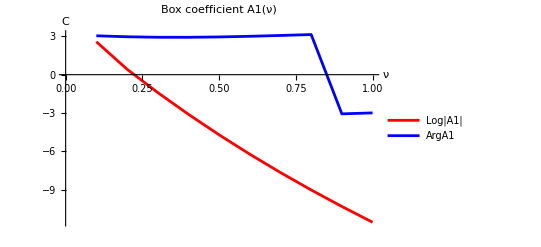

```mathematica
data=Table[{x,Log[N[Abs[A1[x]]]],N[Arg[A1[x]]]},{x,0.1,1,1/10}];
TableForm[data[[1;;10]],TableHeadings->{None,{"x","Log|A1|","ArgA1"}}]
ListPlot[{data[[All,{1,2}]],data[[All,{1,3}]]},PlotLegends->{"Log|A1|","ArgA1"},AxesLabel->{"ν","C"},PlotLabel->"Box coefficient A1(ν)",Joined->True,PlotStyle->{Red,Blue}]
```

x | Log|A2| | ArgA2
0.1 | -0.315859 | 1.20681
0.2 | -1.9125 | 0.894377
0.3 | -3.55358 | 0.670843
0.4 | -5.24727 | 0.557575
0.5 | -6.94594 | 0.566997
0.6 | -8.59943 | 0.706869
0.7 | -10.1512 | 0.972558
0.8 | -11.5448 | 1.3284
0.9 | -12.7553 | 1.70475
1. | -13.8099 | 2.03464

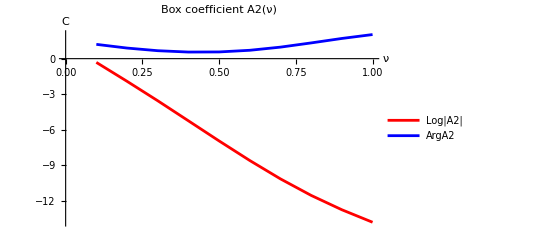

```mathematica
data=Table[{x,Log[N[Abs[A2[x]]]],N[Arg[A2[x]]]},{x,0.1,1,1/10}];
TableForm[data[[1;;10]],TableHeadings->{None,{"x","Log|A2|","ArgA2"}}]
ListPlot[{data[[All,{1,2}]],data[[All,{1,3}]]},PlotLegends->{"Log|A2|","ArgA2"},AxesLabel->{"ν","C"},PlotLabel->"Box coefficient A2(ν)",Joined->True,PlotStyle->{Red,Blue}]
```

x | Log|A3| | ArgA3
0.1 | 0.377288 | -1.93478
0.2 | -1.21935 | -2.24722
0.3 | -2.86043 | -2.47075
0.4 | -4.55412 | -2.58402
0.5 | -6.25279 | -2.5746
0.6 | -7.90628 | -2.43472
0.7 | -9.45803 | -2.16903
0.8 | -10.8516 | -1.81319
0.9 | -12.0622 | -1.43684
1. | -13.1167 | -1.10695

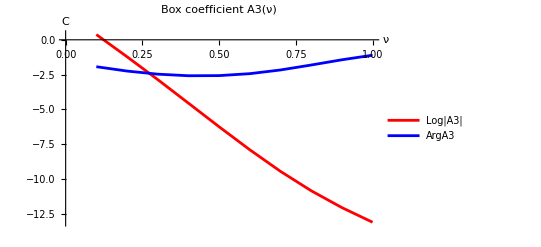

```mathematica
data=Table[{x,Log[N[Abs[A3[x]]]],N[Arg[A3[x]]]},{x,0.1,1,1/10}];
TableForm[data[[1;;10]],TableHeadings->{None,{"x","Log|A3|","ArgA3"}}]
ListPlot[{data[[All,{1,2}]],data[[All,{1,3}]]},PlotLegends->{"Log|A3|","ArgA3"},AxesLabel->{"ν","C"},PlotLabel->"Box coefficient A3(ν)",Joined->True,PlotStyle->{Red,Blue}]
```

x | Log|B1| | ArgB1
0.1 | 1.0558 | 1.10909
0.2 | -0.580805 | 0.711266
0.3 | -2.27794 | 0.42188
0.4 | -4.03411 | 0.26334
0.5 | -5.79465 | 0.245246
0.6 | -7.50539 | 0.371231
0.7 | -9.10809 | 0.632737
0.8 | -10.546 | 0.990942
0.9 | -11.7946 | 1.37387
1. | -12.8817 | 1.71289

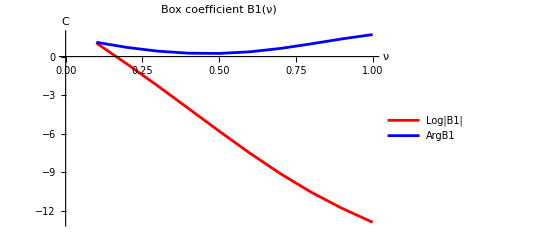

```mathematica
data=Table[{x,Log[N[Abs[B1[x,Pi/4,Pi/4]]]],N[Arg[B1[x,Pi/4,Pi/4]]]},{x,0.1,1,1/10}];
TableForm[data[[1;;10]],TableHeadings->{None,{"x","Log|B1|","ArgB1"}}]
ListPlot[{data[[All,{1,2}]],data[[All,{1,3}]]},PlotLegends->{"Log|B1|","ArgB1"},AxesLabel->{"ν","C"},PlotLabel->"Box coefficient B1(ν)",Joined->True,PlotStyle->{Red,Blue}]
```

x | Log|D1| | ArgD1
0.1 | 3.07292 | 2.74645
0.2 | 0.749762 | 2.41461
0.3 | -1.34204 | 2.19007
0.4 | -3.37115 | 2.09474
0.5 | -5.3365 | 2.13779
0.6 | -7.20804 | 2.32253
0.7 | -8.94058 | 2.64016
0.8 | -10.4854 | 3.0517
0.9 | -11.8232 | -2.7981
1. | -12.9855 | -2.4115

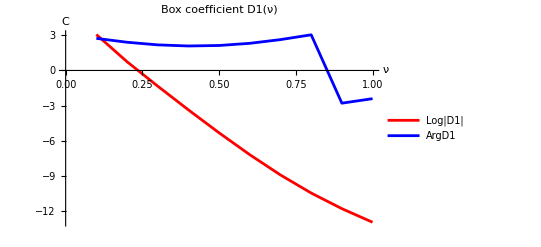

```mathematica
data=Table[{x,Log[N[Abs[D1[x,Pi/2,Pi/2]]]],N[Arg[D1[x,Pi/2,Pi/2]]]},{x,0.1,1,1/10}];
TableForm[data[[1;;10]],TableHeadings->{None,{"x","Log|D1|","ArgD1"}}]
ListPlot[{data[[All,{1,2}]],data[[All,{1,3}]]},PlotLegends->{"Log|D1|","ArgD1"},AxesLabel->{"ν","C"},PlotLabel->"Box coefficient D1(ν)",Joined->True,PlotStyle->{Red,Blue}]
```